```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[];DateObject[];
```

```mathematica
Hyperlink["Go to Hamiltonian sec",{SelectedNotebook[],"Ham"},Appearance->"DialogBox"]
Hyperlink["Go to ASOC sec",{SelectedNotebook[],"Inv"},Appearance->"DialogBox"]
Hyperlink["Go to Superconductor sec",{SelectedNotebook[],"Sup"},Appearance->"DialogBox"]
Hyperlink["Go to Eigen ASOC",{SelectedNotebook[],"EigenValASOC"},Appearance->"DialogBox"]
```

Go to Hamiltonian seca83bd7bc-d343-45a1-ad8d-73c046990475HamButtonDataHyperlinkHyperlinkActive

Go to ASOC seca83bd7bc-d343-45a1-ad8d-73c046990475InvButtonDataHyperlinkHyperlinkActive

Go to Superconductor seca83bd7bc-d343-45a1-ad8d-73c046990475SupButtonDataHyperlinkHyperlinkActive

Go to Eigen ASOCa83bd7bc-d343-45a1-ad8d-73c046990475EigenValASOCButtonDataHyperlinkHyperlinkActive

```mathematica
j1=3/2;mj1=3/2;j2=3/2;mj2=1/2;
a3212=Sum[ClebschGordan[{j1,mj1},{j2,mj2},{J,Mj}]*Subscript[a, J,Mj],{J,0,3,1},{Mj,-J,J,1}];
"------------------------";
j1=3/2;mj1=1/2;j2=3/2;mj2=3/2;
a1232=Sum[ClebschGordan[{j1,mj1},{j2,mj2},{J,Mj}]*Subscript[a, J,Mj],{J,0,3,1},{Mj,-J,J,1}]
Print["|3/2,1/2⟩+|1/2,3/2⟩=",FullSimplify[a1232+a3212]];
"------------------------";
j1=3/2;mj1=-3/2;j2=3/2;mj2=-1/2;
am32m12=Sum[ClebschGordan[{j1,mj1},{j2,mj2},{J,Mj}]*Subscript[a, J,Mj],{J,0,3,1},{Mj,-J,J,1}];
"------------------------";
j1=3/2;mj1=-1/2;j2=3/2;mj2=-3/2;
am12m32=Sum[ClebschGordan[{j1,mj1},{j2,mj2},{J,Mj}]*Subscript[a, J,Mj],{J,0,3,1},{Mj,-J,J,1}]
Print["|-3/2,-1/2⟩+|-1/2,-3/2⟩=",FullSimplify[am12m32+am32m12]];
```

-(a_(2,2))/(√2)+(a_(3,2))/(√2)

|3/2,1/2⟩+|1/2,3/2⟩=√2 a_(3,2)

(a_(2,-2))/(√2)+(a_(3,-2))/(√2)

|-3/2,-1/2⟩+|-1/2,-3/2⟩=√2 a_(3,-2)

```mathematica
"----------For the Low-energy------"
j1=3/2;mj1=3/2;j2=3/2;mj2=3/2;
a3212=Sum[ClebschGordan[{j1,mj1},{j2,mj2},{J,Mj}]*Subscript[a, J,Mj],{J,0,3,1},{Mj,-J,J,1}]
"------------------------";
j1=3/2;mj1=-3/2;j2=3/2;mj2=-3/2;
a1232=Sum[ClebschGordan[{j1,mj1},{j2,mj2},{J,Mj}]*Subscript[a, J,Mj],{J,0,3,1},{Mj,-J,J,1}]
Print["|3/2,3/2⟩+|-3/2,-3/2⟩=",FullSimplify[a1232+a3212]]
"------------------------";
j1=3/2;mj1=1/2;j2=3/2;mj2=1/2;
am32m12=Sum[ClebschGordan[{j1,mj1},{j2,mj2},{J,Mj}]*Subscript[a, J,Mj],{J,0,3,1},{Mj,-J,J,1}]
"------------------------";
j1=3/2;mj1=-1/2;j2=3/2;mj2=-1/2;
am12m32=Sum[ClebschGordan[{j1,mj1},{j2,mj2},{J,Mj}]*Subscript[a, J,Mj],{J,0,3,1},{Mj,-J,J,1}]
Print["|1/2,1/2⟩+|-1/2,-1/2⟩=",FullSimplify[am12m32+am32m12]]
FullSimplify[a1232+a3212+am12m32+am32m12]
```

a_(3,3)

|3/2,3/2⟩+|-3/2,-3/2⟩=a_(3,-3)+a_(3,3)

-√(2/5) a_(1,1)+√(3/5) a_(3,1)

|1/2,1/2⟩+|-1/2,-1/2⟩=-√(2/5) a_(1,-1)-√(2/5) a_(1,1)+√(3/5) (a_(3,-1)+a_(3,1))

-√(2/5) a_(1,-1)-√(2/5) a_(1,1)+a_(3,-3)+√(3/5) a_(3,-1)+√(3/5) a_(3,1)+a_(3,3)

```mathematica
MatrixForm[{{1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}, {0, 1, 0, 0}}.{{p}, {md}, {m}, {pd}}]&&MatrixForm[{{1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}, {0, 1, 0, 0}}.Transpose[{{1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}, {0, 1, 0, 0}}]]
MatrixForm[Inverse[{{1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}, {0, 1, 0, 0}}]]&&MatrixForm[Transpose[{{1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}, {0, 1, 0, 0}}]]
```

(p
pd
m
md)&&(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

(1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0)&&(1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0)

Mon 8 Mar 2021 12:42:39GMT+1.

```mathematica
Clear["Global`*"];
```

```mathematica
DateObject[{2021,3,22,15,53,41.6479069`9.372168057272795},"Instant","Gregorian",1.]
Sum[Subscript[k, mu]**Subscript[k, nu]**Subscript[J, mu]**Subscript[J, nu],{mu,1,3},{nu,1,3}]
```

Mon 22 Mar 2021 15:53:41GMT+1.

k_1**k_1**J_1**J_1+k_1**k_2**J_1**J_2+k_1**k_3**J_1**J_3+k_2**k_1**J_2**J_1+k_2**k_2**J_2**J_2+k_2**k_3**J_2**J_3+k_3**k_1**J_3**J_1+k_3**k_2**J_3**J_2+k_3**k_3**J_3**J_3

```mathematica
Needs["Pauli`"];
```

```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[];DateObject[]
Needs["Pauli`"];
Off[ClebschGordan::phy];
GTnlmcoeff[l_,m_]:=Sqrt[(2*l+1)*(l-m)!/(4*π*(l+m)!)];
SpH[l_,m_]:=Module[{x=kx,y=ky,z=kz},Simplify[PowerExpand[GTnlmcoeff[l,m]*LegendreP[l,m,z/Sqrt[x^2+y^2+z^2]]*Sum[Binomial[Abs[m],k]*(x/Sqrt[x^2+y^2])^k*(y/Sqrt[x^2+y^2])^(Abs[m]-k)*(Cos[π*(Abs[m]-k)/2]+I*Sign[m]*Sin[π*(Abs[m]-k)/2]),{k,0,Abs[m]}]]]];


FF[oo_]:=FullSimplify[oo,Element[{kx,ky,kz,Δ,β,γ,k,μ,α,ϵ},Reals]];

Cjn[Matris_]:=Matris/.{Complex[y_,x_]->Complex[y,-x]};
"--------|S,M_s;L,M_L⟩=∑_(J = |L - S|)^(|L + S|)  ∑_M_j^J ⟨Jm_j|S,M_s;L,M_L⟩ |Jm_j⟩----------";
Jtot[S_,MS_,L_,ML_]:=Sum[Sum[Conjugate[ClebschGordan[{S,MS},{L,ML},{Jj,mjj}]]*Subscript[J, Jj,mjj],{mjj,-Jj,Jj,1}],{Jj,Abs[S-L],Abs[S+L],1}];
"--------|S_1,S_2;M_S_1,M_S_2⟩=∑_(S = |SubscriptBox[S, 1] - SubscriptBox[S, 2]|)^(|SubscriptBox[S, 1] + SubscriptBox[S, 2]|)  ∑_M_s^S ⟨S,M_s|S_1,S_2;M_S_1,M_S_2⟩ |S,M_s⟩=∑_(S = |SubscriptBox[S, 1] - SubscriptBox[S, 2]|)^(|SubscriptBox[S, 1] + SubscriptBox[S, 2]|)  ∑_M_s^S ⟨S,M_s|S_1,S_2;M_S_1,M_S_2⟩(∑_(J = |L - S|)^(|L + S|)  ∑_M_j^J ⟨J,m_j|S,M_s;L,M_L⟩ |J,m_j⟩--------)";
TsT32[ms1_,ms2_,L_,ML_]:=Module[{S1=3/2,S2=3/2},Sum[Sum[Conjugate[ClebschGordan[{S1,ms1},{S1,ms2},{Skol,MsKol}]]*Jtot[Skol,MsKol,L,ML],{MsKol,-Skol,Skol,1}],{Skol,Abs[S1-S2],Abs[S1+S2],1}]];
"----------|S_1,S_2;M_S_1,M_S_2⟩=∑_(S = |SubscriptBox[S, 1] - SubscriptBox[S, 2]|)^(|SubscriptBox[S, 1] + SubscriptBox[S, 2]|)  ∑_M_s^S ⟨S,M_s|S_1,S_2;M_S_1,M_S_2⟩ |S,M_s⟩=∑_(S = |SubscriptBox[S, 1] - SubscriptBox[S, 2]|)^(|SubscriptBox[S, 1] + SubscriptBox[S, 2]|)  ∑_M_s^S ⟨S,M_s|S_1,S_2;M_S_1,M_S_2⟩(∑_(J = |L - S|)^(|L + S|)  ∑_M_j^J ⟨J,m_j|S,M_s;L,M_L⟩ ∑_M_j_1^(3/2)  ∑_M_j_2^(3/2) ⟨3/23/2;M_sM_j_1,M_j_2|J,m_j⟩ a_M_j_1^†a_M_j_1^†-----------------";
Tj1j2T[J_,Mj_]:=Module[{S1=3/2,S2=3/2},Sum[ClebschGordan[{S1,mj1},{S2,mj2},{J,Mj}]*Subscript[a, mj1,mj2],{mj1,S1,-S1,-1},{mj2,S2,-S2,-1}]];


"Returning from J to SL representation:";
JtoSL[J_,MJ_,S_,L_]:=Sum[Sum[ClebschGordan[{S,MS},{L,ML},{J,MJ}]*(Subscript[Π, ML]*Subscript[Σ, MS]),{MS,-S,S,1}],{ML,-L,L,1}];


LStoJz[Ml_,MS_]:=Module[{L=1,S=1/2},Sum[Sum[Conjugate[ClebschGordan[{L,Ml},{S,MS},{Jz,Mj}]]*(Subscript[Π, Jz,Mj]),{Mj,-Jz,Jz,1}],{Jz,Abs[L-S],Abs[L+S],1}]];
```

Fri 2 Sep 2022 12:05:26GMT+2

```mathematica
FullSimplify[JtoSL[3,2,3,1]]
FullSimplify[JtoSL[3,-2,3,1]]
FullSimplify[ⅈ/Sqrt[2](JtoSL[3,-2,3,1]-JtoSL[3,2,3,1])]
```

1/6 (-√15 Π_1 Σ_1+2 √3 Π_0 Σ_2+3 Π_-1 Σ_3)

1/6 (-3 Π_1 Σ_-3-2 √3 Π_0 Σ_-2+√15 Π_-1 Σ_-1)

-(ⅈ (Π_1 (3 Σ_-3-√15 Σ_1)+2 √3 Π_0 (Σ_-2+Σ_2)+Π_-1 (-√15 Σ_-1+3 Σ_3)))/(6 √2)

```mathematica
FullSimplify[(-ⅈ*ⅈ)/Sqrt[2](JtoSL[3,-2,3,1]+JtoSL[3,2,3,1])]
```

(-Π_1 (3 Σ_-3+√15 Σ_1)+2 √3 Π_0 (-Σ_-2+Σ_2)+Π_-1 (√15 Σ_-1+3 Σ_3))/(6 √2)

```mathematica
FullSimplify[JtoSL[2,2,3,1]]
FullSimplify[JtoSL[2,1,3,1]]
FullSimplify[JtoSL[2,0,3,1]]
```

√(5/7) Π_(-1,3)+(-√5 Π_(0,2)+Π_(1,1))/(√21)

(√30 Π_(-1,2)-2 √6 Π_(0,1)+3 Π_(1,0))/(3 √7)

√(2/7) Π_(-1,1)-√(3/7) Π_(0,0)+√(2/7) Π_(1,-1)

```mathematica
FullSimplify[JtoSL[2,2,3,1]]
FullSimplify[JtoSL[2,-2,3,1]]
9*7
FullSimplify[JtoSL[2,2,3,1]+JtoSL[2,-2,3,1]]
```

√(5/7) Π_(-1,3)+(-√5 Π_(0,2)+Π_(1,1))/(√21)

(Π_(-1,-1))/(√21)-√(5/21) Π_(0,-2)+√(5/7) Π_(1,-3)

63

(√3 Π_(-1,-1)+3 √5 Π_(-1,3)-√15 Π_(0,-2)-√15 Π_(0,2)+3 √5 Π_(1,-3)+√3 Π_(1,1))/(3 √7)

```mathematica
70/(14*14)&&105/(14*14)&&21/(14*14)&&6/28&&4/28&&16/28&&15/28
15/36
```

5/14&&15/28&&3/28&&3/14&&1/7&&4/7&&15/28

5/12

```mathematica
FullSimplify[JtoSL[2,0,3,1]+JtoSL[2,0,1,1]]
```

(√(2/7)+1/(√6)) Π_(-1,1)+(-√(3/7)+√(2/3)) Π_(0,0)+(√(2/7)+1/(√6)) Π_(1,-1)

```mathematica
LStoJz[-1,-1/2]
```

Π_(3/2,-3/2)

```mathematica
TsT12[ms1_,ms2_,L_,ML_]
```

```mathematica
JtoSL[0,0,1,1]
JtoSL[0,0,0,0]
```

(Π_(-1,1))/(√3)-(Π_(0,0))/(√3)+(Π_(1,-1))/(√3)

Π_(0,0)

```mathematica
FullSimplify[SpH[1,1]*Cjn[SpH[1,1]]]
```

(3 (kx^2+ky^2))/(8 (kx^2+ky^2+kz^2) π)

```mathematica
FF[JtoSL[2,-2,1,1]+JtoSL[2,2,1,1]]
FF[JtoSL[2,-2,2,0]+JtoSL[2,2,2,0]]
FF[JtoSL[2,-2,3,1]+JtoSL[2,2,3,1]]
```

Π_(-1,-1)+Π_(1,1)

Π_(-2,0)+Π_(2,0)

(3 √5 Π_(-3,1)-√15 Π_(-2,0)+√3 Π_(-1,-1)+√3 Π_(1,1)-√15 Π_(2,0)+3 √5 Π_(3,-1))/(3 √7)

```mathematica
Outp=PauliMatrix[1]*FullSimplify[Table[

TsT[i,j,0,0]
,{i,1/2,-1/2,-1},{j,1/2,-1/2,-1}]
];MatrixForm[Outp]
FullSimplify[Total[Flatten[Outp]]]
```

(0 | (J_(0,0)+J_(1,0))/(√2)
(-J_(0,0)+J_(1,0))/(√2) | 0)

√2 J_(1,0)

```mathematica
L=2;
For[MLL=-L,MLL≤L,MLL++,Print[{{L,MLL},SpH[L,MLL]}]]
```

{{2,-2},((kx-ⅈ ky)^2 √(15/(2 π)))/(4 (kx^2+ky^2+kz^2))}

{{2,-1},((kx-ⅈ ky) kz √(15/(2 π)))/(2 (kx^2+ky^2+kz^2))}

{{2,0},-((kx^2+ky^2-2 kz^2) √(5/π))/(4 (kx^2+ky^2+kz^2))}

{{2,1},-((kx+ⅈ ky) kz √(15/(2 π)))/(2 (kx^2+ky^2+kz^2))}

{{2,2},((kx+ⅈ ky)^2 √(15/(2 π)))/(4 (kx^2+ky^2+kz^2))}

```mathematica
(FullSimplify[SphericalHarmonicY[1,1,tet,phi]/SphericalHarmonicY[1,-1,tet,phi]])(**SphericalHarmonicY[2,0,tet,phi]*)
SpH[1,1]/SpH[1,-1]
```

-ⅇ^(2 ⅈ phi)

-(kx+ⅈ ky)/(kx-ⅈ ky)

```mathematica
DateObject[{2021,3,24,23,6,48.9449816`9.442283027816794},"Instant","Gregorian",1.]

(*"++ Band"*)

vvl=FullSimplify[ValanceBands,Element[{kx,ky,kz,Δ,α,β,γ,k,μ,α,ϵ,δ},Reals]];
(*"-- Band"*)
ConductionBands=Transpose[{rs3,rs4}];
Ccd=FullSimplify[ConductionBands,Element[{kx,ky,kz,Δ,α,β,γ,k,μ,α,ϵ,δ},Reals]];
VVv=SpH[1,1]*Cjn[SpH[1,1]]{{-SpH[1,0]/SpH[1,1], 1/Sqrt[2] Cjn[SpH[1,1]]/SpH[1,1]}, {Sqrt[3/2], 0}, {0, Sqrt[3/2]}, {1/Sqrt[2] SpH[1,1]/Cjn[SpH[1,1]], SpH[1,0]/Cjn[SpH[1,1]]}};
Nn=2SpH[1,0]*SpH[1,0]+SpH[1,1]*Cjn[SpH[1,1]];
WWw=1/Sqrt[Nn]*{{-Sqrt[3]SpH[1,0]*Cjn[SpH[1,1]], -Sqrt[3/2](Cjn[SpH[1,1]])^2}, {-Nn, 0}, {0, Nn}, {Sqrt[3/2]SpH[1,1]*SpH[1,1], -Sqrt[3]SpH[1,0]*SpH[1,1]}};
MF[M_]:=FullSimplify[M,Element[{kx,ky,kz,Δ,α,β,γ,k,μ,α,ϵ,δ},Reals]];
MatrixForm[MF[VVv]]&&MatrixForm[MF[WWw]]

"Ziri Male man ast"
MatrixForm[Ccd]&&MatrixForm[vvl]
```

Wed 24 Mar 2021 23:06:48GMT+1.

((3 (kx-ⅈ ky) kz)/(4 √2 (kx^2+ky^2+kz^2) π) | (3 (kx-ⅈ ky)^2)/(8 √2 (kx^2+ky^2+kz^2) π)
(3 √(3/2) (kx^2+ky^2))/(8 (kx^2+ky^2+kz^2) π) | 0
0 | (3 √(3/2) (kx^2+ky^2))/(8 (kx^2+ky^2+kz^2) π)
(3 (kx+ⅈ ky)^2)/(8 √2 (kx^2+ky^2+kz^2) π) | -(3 (kx+ⅈ ky) kz)/(4 √2 (kx^2+ky^2+kz^2) π))&&((3 (kx-ⅈ ky) kz)/(2 √((kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2)) √π) | -(3 (kx-ⅈ ky)^2)/(4 √((kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2)) √π)
-1/2 √(4-(3 (kx^2+ky^2))/(kx^2+ky^2+kz^2)) √(3/(2 π)) | 0
0 | 1/2 √(4-(3 (kx^2+ky^2))/(kx^2+ky^2+kz^2)) √(3/(2 π))
(3 (kx+ⅈ ky)^2)/(4 √((kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2)) √π) | (3 (kx+ⅈ ky) kz)/(2 √((kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2)) √π))

Ziri Male man ast

(((kx-ⅈ ky) kz)/((kx+ⅈ ky)^2 √(1+kz^2/(kx^2+ky^2))) | (kx-ⅈ ky)/(2 (kx+ⅈ ky) √(1+kz^2/(kx^2+ky^2)))
(√3 (kx-ⅈ ky))/((kx+ⅈ ky) √(4+(4 kz^2)/(kx^2+ky^2))) | 0
0 | (√3)/(2 √(1+kz^2/(kx^2+ky^2)))
1/(√(4+(4 kz^2)/(kx^2+ky^2))) | -kz/((kx-ⅈ ky) √(1+kz^2/(kx^2+ky^2))))&&((√3 (kx-ⅈ ky)^2 kz)/((kx+ⅈ ky) √((kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2))) | -(√3 (kx-ⅈ ky)^2)/(2 √((kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2)))
-((kx^2+ky^2) √(4-(3 (kx^2+ky^2))/(kx^2+ky^2+kz^2)))/(2 (kx+ⅈ ky)^2) | 0
0 | 1/(√(1+(3 (kx^2+ky^2))/(kx^2+ky^2+4 kz^2)))
(√3 (kx^2+ky^2))/(2 √((kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2))) | (√3 (kx+ⅈ ky) kz)/(√((kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2))))

```mathematica
"Column One"
FullSimplify[Solve[((kx-ⅈ ky) kz)/((kx+ⅈ ky)^2 √(1+kz^2/(kx^2+ky^2)))dd==(kz √((kx^2+ky^2)/(kx^2+ky^2+kz^2)))/(kx+ⅈ ky),dd],Element[{kx,ky,kz,Δ,α,β,γ,k,μ,α,ϵ,δ},Reals]]
FullSimplify[Solve[(√3 (kx-ⅈ ky))/((kx+ⅈ ky) √(4+(4 kz^2)/(kx^2+ky^2)))gg==1/2 √3 √((kx^2+ky^2)/(kx^2+ky^2+kz^2)),gg],Element[{kx,ky,kz,Δ,α,β,γ,k,μ,α,ϵ,δ},Reals]]

"------------------------------------------------------------------------"
"------------------------------------------------------------------------"
"------------------------------------------------------------------------"
"Column second"
FullSimplify[Solve[(√3)/(2 √(1+kz^2/(kx^2+ky^2)))aa==1/2 √3 √((kx^2+ky^2)/(kx^2+ky^2+kz^2)),aa],Element[{kx,ky,kz,Δ,α,β,γ,k,μ,α,ϵ,δ},Reals]]
FullSimplify[Solve[(kx-ⅈ ky)/(2 (kx+ⅈ ky) √(1+kz^2/(kx^2+ky^2)))bb==((kx-ⅈ ky) √((kx^2+ky^2)/(kx^2+ky^2+kz^2)))/(2 (kx+ⅈ ky)),bb],Element[{kx,ky,kz,Δ,α,β,γ,k,μ,α,ϵ,δ},Reals]]
```

Column One

{{dd→-1+(2 kx)/(kx-ⅈ ky)}}

{{gg→-1+(2 kx)/(kx-ⅈ ky)}}

------------------------------------------------------------------------

------------------------------------------------------------------------

------------------------------------------------------------------------

Column second

{{aa→1}}

{{bb→1}}

```mathematica
SpH[1,1]/SpH[1,-1]
```

-(kx+ⅈ ky)/(kx-ⅈ ky)

```mathematica
a=Flatten[(Sqrt[(3 (kx-ⅈ ky))/(4 (kx+ⅈ ky) √(2+(2 kz^2)/(kx^2+ky^2)) π)])*{{((kx-ⅈ ky) kz)/((kx+ⅈ ky)^2 √(1+kz^2/(kx^2+ky^2))), (√3 (kx-ⅈ ky))/((kx+ⅈ ky) √(4+(4 kz^2)/(kx^2+ky^2))), 0, 1/(√(4+(4 kz^2)/(kx^2+ky^2)))}}];
b=Flatten[(Sqrt[3/(4 √(2+(2 kz^2)/(kx^2+ky^2)) π)])*{{(kx-ⅈ ky)/(2 (kx+ⅈ ky) √(1+kz^2/(kx^2+ky^2))), (√3)/(2 √(1+kz^2/(kx^2+ky^2))), 0, -kz/((kx-ⅈ ky) √(1+kz^2/(kx^2+ky^2)))}}];

Nh=MF[Transpose[{a,b}]];
MatrixForm[MF[TrCj[Nh].VVv]]
```

((3 √3 (kx+ⅈ ky) √((kx+ⅈ ky)^2) ((kx^2+ky^2)/((kx^2+ky^2+kz^2)^3))^(1/4))/(8 2^(3/4) (kx-ⅈ ky) π^(3/2)) | 0
(9 √3 ((kx^2+ky^2)/(kx^2+ky^2+kz^2))^(7/4))/(32 2^(3/4) π^(3/2)) | (3 √3 (kx^2+ky^2)^(3/4) (kx^2+ky^2+4 kz^2))/(32 2^(3/4) (kx^2+ky^2+kz^2)^(7/4) π^(3/2)))

```mathematica
-Subscript[J, 2,2]/(√2)+Subscript[J, 3,2]/(√2)
```

```mathematica
-Subscript[J, 2,2]/(√2)+Subscript[J, 3,2]/(√2)
```

```mathematica
Needs["Pauli`"];


Ε={{(ω-Em), 0}, {0, (ω+Ep)}};
Δk={{0, Δmp}, {SuperDagger[(Δmp)], 0}};
h12={{0, Δpp}, {SuperDagger[(Δmm)], 0}};
h21={{0, Δmm}, {SuperDagger[(Δpp)], 0}};
oo=Inverse[Ε]+(Inverse[Ε].Δk.Inverse[Ε]);
MatrixForm[oo]
oo1=Inner[NonCommutativeMultiply,oo,h21,Plus];
oo2=Inner[NonCommutativeMultiply,h12,oo1,Plus];
MatrixForm[oo2]
(*
MatrixForm[Inner[NonCommutativeMultiply,Δk,Inverse[Ε],Plus]]*)
```

(1/(-Em+ω) | Δmp/((-Em+ω) (Ep+ω))
Δmp^†/((-Em+ω) (Ep+ω)) | 1/(Ep+ω))

(0**(1/(-Em+ω)**0+Δmp/((-Em+ω) (Ep+ω))**Δpp^†)+Δpp**(1/(Ep+ω)**Δpp^†+Δmp^†/((-Em+ω) (Ep+ω))**0) | 0**(1/(-Em+ω)**Δmm+Δmp/((-Em+ω) (Ep+ω))**0)+Δpp**(1/(Ep+ω)**0+Δmp^†/((-Em+ω) (Ep+ω))**Δmm)
0**(1/(Ep+ω)**Δpp^†+Δmp^†/((-Em+ω) (Ep+ω))**0)+Δmm^†**(1/(-Em+ω)**0+Δmp/((-Em+ω) (Ep+ω))**Δpp^†) | 0**(1/(Ep+ω)**0+Δmp^†/((-Em+ω) (Ep+ω))**Δmm)+Δmm^†**(1/(-Em+ω)**Δmm+Δmp/((-Em+ω) (Ep+ω))**0))

```mathematica
({{Δpp**((1/(Ep+ω))**SuperDagger[Δpp]), Δpp**((SuperDagger[Δmp]/((-Em+ω) (Ep+ω)))**Δmm)}, {SuperDagger[Δmm]**((Δmp/((-Em+ω) (Ep+ω)))**SuperDagger[Δpp]), SuperDagger[Δmm]**((1/(-Em+ω))**Δmm)}})
```

```mathematica
({{0, 0**0+Δmp**(1/(Ep+ω))}, {0**0+SuperDagger[Δmp]**(1/(-Em+ω)), 0}})
```

```mathematica
Series[(a+x)^-1,{x,0,2}]
Series[(*a^-1*)(1+a^-1 x)^-1,{x,0,2}]
```

1/a-x/a^2+x^2/a^3+O[x]^3

1-x/a+x^2/a^2+O[x]^3

```mathematica
Needs["Pauli`"];

"This is for low-energy regime"

h12={{δ1, Δ1}, {Δ2d, δ2}};
h21={{δ3, Δ2}, {Δ1d, δ4}};

oo1=Inner[NonCommutativeMultiply,h12,h21,Plus];

MatrixForm[oo1]
(*
MatrixForm[Inner[NonCommutativeMultiply,Δk,Inverse[Ε],Plus]]*)
```

SetDelayed::write: Tag Tr in Tr[m_] is Protected.

(δ1**δ3+Δ1**Δ1d | δ1**Δ2+Δ1**δ4
δ2**Δ1d+Δ2d**δ3 | δ2**δ4+Δ2d**Δ2)

```mathematica
Needs["Pauli`"];

"This is for Finite-energy regime"

h12={{δ1, Δ1}, {Δ2d, δ2}};
ee={{a^-1, 0}, {0, b^-1}};
h21={{δ3, Δ2}, {Δ1d, δ4}};

oo1=Inner[NonCommutativeMultiply,h12,ee,Plus];
oo2=Inner[NonCommutativeMultiply,oo1,h21,Plus];

MatrixForm[oo2]
(*
MatrixForm[Inner[NonCommutativeMultiply,Δk,Inverse[Ε],Plus]]*)
```

This is for Finite-energy regime

((δ1**1/a+Δ1**0)**δ3+(δ1**0+Δ1**1/b)**Δ1d | (δ1**1/a+Δ1**0)**Δ2+(δ1**0+Δ1**1/b)**δ4
(δ2**1/b+Δ2d**0)**Δ1d+(δ2**0+Δ2d**1/a)**δ3 | (δ2**1/b+Δ2d**0)**δ4+(δ2**0+Δ2d**1/a)**Δ2)

```mathematica
Needs["Pauli`"];

"This is for Finite-energy regime"


h12={{Δ1, Δ2}, {Δ3, Δ4}};
ee={{a^-1, 0}, {0, b^-1}};
h21={{Δ1d, Δ3d}, {Δ2d, Δ4d}};

ee2={{-a^-1-λ, 0}, {0, -b^-1-λ}};
MatrixForm[FullSimplify[Det[ee2-h21.ee.h12]]]


oo1=Inner[NonCommutativeMultiply,h12,ee,Plus];
oo2=Inner[NonCommutativeMultiply,oo1,h21,Plus];

oo3=Inner[NonCommutativeMultiply,h12,h21,Plus];
MatrixForm[oo2]
MatrixForm[oo3]
(*
MatrixForm[Inner[NonCommutativeMultiply,Δk,Inverse[Ε],Plus]]*)
```

This is for Finite-energy regime

(Δ2 Δ2d)/a^2+(Δ3 Δ3d)/b^2+((1+Δ3 Δ3d+Δ4 Δ4d) λ)/b+λ^2+(1+Δ2 Δ2d Δ3 Δ3d-Δ1d Δ2 Δ3 Δ4d+Δ4 Δ4d+b λ+b Δ2 Δ2d λ+Δ1 (Δ1d-Δ2d Δ3d Δ4+Δ1d Δ4 Δ4d+b Δ1d λ))/(a b)

((Δ1**1/a+Δ2**0)**Δ1d+(Δ1**0+Δ2**1/b)**Δ2d | (Δ1**1/a+Δ2**0)**Δ3d+(Δ1**0+Δ2**1/b)**Δ4d
(Δ3**1/a+Δ4**0)**Δ1d+(Δ3**0+Δ4**1/b)**Δ2d | (Δ3**1/a+Δ4**0)**Δ3d+(Δ3**0+Δ4**1/b)**Δ4d)

(Δ1**Δ1d+Δ2**Δ2d | Δ1**Δ3d+Δ2**Δ4d
Δ3**Δ1d+Δ4**Δ2d | Δ3**Δ3d+Δ4**Δ4d)

```mathematica
MatrixForm[FullSimplify[Solve[Δ2^2/a^2+Δ3^2/b^2+((1+Δ3^2+Δ4^2) λ)/b+λ^2+(1+Δ2^2 Δ3^3-Δ1d Δ2 Δ3 Δ4d+Δ4^2+b λ+b Δ2^2 λ+ (Δ1^2-Δ1*Δ2d *Δ3d* Δ4+Δ1^2 Δ4^2+b Δ1^2 λ))/(a b)==0,λ]]]
```

(λ→-(1+Δ1^2+Δ2^2)/(2 a)-(1+Δ3^2+Δ4^2+b √(((1+Δ1^2)^2+2 (-1+Δ1^2) Δ2^2+Δ2^4)/a^2+(Δ3^4+2 Δ3^2 (-1+Δ4^2)+(1+Δ4^2)^2)/b^2+(2 (-1+Δ3^2+2 Δ1 Δ2d Δ3d Δ4-Δ4^2+Δ1^2 (-1+Δ3^2-Δ4^2)+Δ2 (Δ2 (1+Δ3^2-2 Δ3^3+Δ4^2)+2 Δ1d Δ3 Δ4d)))/(a b)))/(2 b)
λ→-(1+Δ1^2+Δ2^2)/(2 a)-(1+Δ3^2+Δ4^2-b √(((1+Δ1^2)^2+2 (-1+Δ1^2) Δ2^2+Δ2^4)/a^2+(Δ3^4+2 Δ3^2 (-1+Δ4^2)+(1+Δ4^2)^2)/b^2+(2 (-1+Δ3^2+2 Δ1 Δ2d Δ3d Δ4-Δ4^2+Δ1^2 (-1+Δ3^2-Δ4^2)+Δ2 (Δ2 (1+Δ3^2-2 Δ3^3+Δ4^2)+2 Δ1d Δ3 Δ4d)))/(a b)))/(2 b))

```mathematica
Hyperlink["Go to Hamiltonian sec",{SelectedNotebook[],"Ham"},Appearance->"DialogBox"]
Hyperlink["Go to ASOC sec",{SelectedNotebook[],"Inv"},Appearance->"DialogBox"]
Hyperlink["Go to Superconductor sec",{SelectedNotebook[],"Sup"},Appearance->"DialogBox"]
Hyperlink["Go to Eigen ASOC",{SelectedNotebook[],"EigenValASOC"},Appearance->"DialogBox"]
```

Go to Hamiltonian sect5btk_shmHamButtonDataHyperlinkHyperlinkActive

Go to ASOC sect5btk_shmInvButtonDataHyperlinkHyperlinkActive

Go to Superconductor sect5btk_shmSupButtonDataHyperlinkHyperlinkActive

Go to Eigen ASOCt5btk_shmEigenValASOCButtonDataHyperlinkHyperlinkActive

```mathematica
H3={{Subscript[Ε, 1], 0, -dx+ⅈ dy+d0, dz}, {0, Subscript[Ε, 1], dz, dx+ⅈ dy+d0}, {-dx-ⅈ dy+d0, dz, Subscript[Ε, 2], 0}, {dz, dx-ⅈ dy+d0, 0, Subscript[Ε, 2]}};MatrixForm[FullSimplify[Eigenvalues[{{Subscript[Ε, 1], Dd}, {DDd, Subscript[Ε, 2]}}]]]
MatrixForm[FullSimplify[Eigenvalues[H3]]]
```

(1/2 (Ε_1-√(4 Dd DDd+(Ε_1-Ε_2)^2)+Ε_2)
1/2 (Ε_1+√(4 Dd DDd+(Ε_1-Ε_2)^2)+Ε_2))

(1/2 (Ε_1-√(4 (d0^2+dx^2+dy^2+dz^2-2 √(d0^2 (dx^2+dz^2)))+(Ε_1-Ε_2)^2)+Ε_2)
1/2 (Ε_1+√(4 (d0^2+dx^2+dy^2+dz^2-2 √(d0^2 (dx^2+dz^2)))+(Ε_1-Ε_2)^2)+Ε_2)
1/2 (Ε_1-√(4 (d0^2+dx^2+dy^2+dz^2+2 √(d0^2 (dx^2+dz^2)))+(Ε_1-Ε_2)^2)+Ε_2)
1/2 (Ε_1+√(4 (d0^2+dx^2+dy^2+dz^2+2 √(d0^2 (dx^2+dz^2)))+(Ε_1-Ε_2)^2)+Ε_2))

```mathematica
Hyperlink["Go to Hamiltonian sec",{SelectedNotebook[],"Ham"},Appearance->"DialogBox"]
Hyperlink["Go to ASOC sec",{SelectedNotebook[],"Inv"},Appearance->"DialogBox"]
Hyperlink["Go to Superconductor sec",{SelectedNotebook[],"Sup"},Appearance->"DialogBox"]
Hyperlink["Go to Eigen ASOC",{SelectedNotebook[],"EigenValASOC"},Appearance->"DialogBox"]

Needs["Pauli`"];

"Spectrum formalism of pairing in the presence of ASOC";
FF[oo_]:=FullSimplify[oo,{Element[{kx,ky,kz,Δ,β,γ,k,μ,α,ϵ},Reals],kx>0,ky>0,kz>0}]

"Note Note Note that in this formalism, the the pairing should be projected again into the eignbasis of the normal-state in the presence of ASOC. Then, the follwoing formalism is consistent."


H1={{Subscript[Ε, 1], 0, 0, -ψ*ⅈ}, {0, Subscript[Ε, 2], ψ*ⅈ, 0}, {0, ψt*ⅈ, -Subscript[Ε, 1], 0}, {-ψt*ⅈ, 0, 0, -Subscript[Ε, 2]}};

Print["Spin-singlet ASOC",MatrixForm[FF[Eigenvalues[H1]]]]
"------------------------------------------------------------"


H3={{Subscript[Ε, 1]+a, 0, -dx+ⅈ dy, dz}, {0, Subscript[Ε, 1]-a, dz, dx+ⅈ dy}, {-SuperStar[dx]-ⅈ SuperStar[dy], SuperStar[dz], -Subscript[Ε, 1]-a, 0}, {SuperStar[dz], SuperStar[dx]-ⅈ SuperStar[dy], 0, -Subscript[Ε, 1]+a}};


(*H2={{Subscript[Ε, 1], 0, -dx+ⅈ dy, dz}, {0, Subscript[Ε, 2], dz, dx+ⅈ dy}, {-dxd-ⅈ dyd, dzd, -Subscript[Ε, 1], 0}, {dzd, dxd-ⅈ dyd, 0, -Subscript[Ε, 2]}};*)
Print["Complex d-vector: Spin-triplet ASOC",MatrixForm[FF[Eigenvalues[H2]]]]
"------------------------------------------------------------"


H3={{Subscript[Ε, 1]+a, 0, -(dx-ⅈ dy) γ, dz γ}, {0, Subscript[Ε, 1]-a, dz γ, (dx+ⅈ dy) γ}, {-(dx+ⅈ dy) SuperStar[γ], dz SuperStar[γ], -Subscript[Ε, 1]-a, 0}, {dz SuperStar[γ], (dx-ⅈ dy) SuperStar[γ], 0, -Subscript[Ε, 1]+a}};


Print["One component complex d-vector :Spin-triplet ASOC",MatrixForm[FF[Eigenvalues[H3]]]]
"------------------------------------------------------------"
H4={{Subscript[Ε, 1]+a, 0, -dx+ⅈ dy, dz}, {0, Subscript[Ε, 1]-a, dz, dx+ⅈ dy}, {-dx-ⅈ dy, dz, -Subscript[Ε, 1]-a, 0}, {dz, dx-ⅈ dy, 0, -Subscript[Ε, 1]+a}};
Print["Real d-vector :Spin-triplet ASOC",MatrixForm[FF[Eigenvalues[H4]]]]
"------------------------------------------------------------"
MatrixForm[ⅈ*SuperStar[γ]*(dx*PauliMatrix[1]+dy*PauliMatrix[2]+dz*PauliMatrix[3]).PauliMatrix[2]]
Vv={{1, 0}, {0, 1}};

MatrixForm[Subscript[Ε, 1]*Vv+(gx*PauliMatrix[1]+gy*PauliMatrix[2]+gz*PauliMatrix[3])]
```

Go to Hamiltonian secqwt6m_shmHamButtonDataHyperlinkHyperlinkActive

Go to ASOC secqwt6m_shmInvButtonDataHyperlinkHyperlinkActive

Go to Superconductor secqwt6m_shmSupButtonDataHyperlinkHyperlinkActive

Go to Eigen ASOCqwt6m_shmEigenValASOCButtonDataHyperlinkHyperlinkActive

Note Note Note that in this formalism, the the pairing should be projected again into the eignbasis of the normal-state in the presence of ASOC. Then, the follwoing formalism is consistent.

Spin-singlet ASOC(1/2 (Ε_1-Ε_2-√(-4 ψ ψt+(Ε_1+Ε_2)^2))
1/2 (-Ε_1+Ε_2-√(-4 ψ ψt+(Ε_1+Ε_2)^2))
1/2 (Ε_1-Ε_2+√(-4 ψ ψt+(Ε_1+Ε_2)^2))
1/2 (-Ε_1+Ε_2+√(-4 ψ ψt+(Ε_1+Ε_2)^2)))

------------------------------------------------------------

Complex d-vector: Spin-triplet ASOCEigenvalues[H2]

------------------------------------------------------------

One component complex d-vector :Spin-triplet ASOC(-√(a^2+Ε_1^2+(dx^2+dy^2+dz^2) γ γ^*-2 √(a^2 (Ε_1^2+dz^2 γ γ^*)))
√(a^2+Ε_1^2+(dx^2+dy^2+dz^2) γ γ^*-2 √(a^2 (Ε_1^2+dz^2 γ γ^*)))
-√(a^2+Ε_1^2+(dx^2+dy^2+dz^2) γ γ^*+2 √(a^2 (Ε_1^2+dz^2 γ γ^*)))
√(a^2+Ε_1^2+(dx^2+dy^2+dz^2) γ γ^*+2 √(a^2 (Ε_1^2+dz^2 γ γ^*))))

------------------------------------------------------------

Real d-vector :Spin-triplet ASOC(-√(a^2+dx^2+dy^2+dz^2+Ε_1^2-2 √(a^2 (dz^2+Ε_1^2)))
√(a^2+dx^2+dy^2+dz^2+Ε_1^2-2 √(a^2 (dz^2+Ε_1^2)))
-√(a^2+dx^2+dy^2+dz^2+Ε_1^2+2 √(a^2 (dz^2+Ε_1^2)))
√(a^2+dx^2+dy^2+dz^2+Ε_1^2+2 √(a^2 (dz^2+Ε_1^2))))

------------------------------------------------------------

(-(dx-ⅈ dy) γ^* | dz γ^*
dz γ^* | (dx+ⅈ dy) γ^*)

(dz+Ε_1 | dx-ⅈ dy
dx+ⅈ dy | -dz+Ε_1)

```mathematica
Hyperlink["Go to Hamiltonian sec",{SelectedNotebook[],"Ham"},Appearance->"DialogBox"]
Hyperlink["Go to ASOC sec",{SelectedNotebook[],"Inv"},Appearance->"DialogBox"]
Hyperlink["Go to Superconductor sec",{SelectedNotebook[],"Sup"},Appearance->"DialogBox"]
Hyperlink["Go to Eigen ASOC",{SelectedNotebook[],"EigenValASOC"},Appearance->"DialogBox"]
Hyperlink["Go to Pairing Strength",{SelectedNotebook[],"PairingStrength"},Appearance->"DialogBox"]
```

Go to Hamiltonian seca83bd7bc-d343-45a1-ad8d-73c046990475HamButtonDataHyperlinkHyperlinkActive

Go to ASOC seca83bd7bc-d343-45a1-ad8d-73c046990475InvButtonDataHyperlinkHyperlinkActive

Go to Superconductor seca83bd7bc-d343-45a1-ad8d-73c046990475SupButtonDataHyperlinkHyperlinkActive

Go to Eigen ASOCa83bd7bc-d343-45a1-ad8d-73c046990475EigenValASOCButtonDataHyperlinkHyperlinkActive

Go to Pairing Strengtha83bd7bc-d343-45a1-ad8d-73c046990475PairingStrengthButtonDataHyperlinkHyperlinkActive

```mathematica
Hyperlink["Go to Hamiltonian sec",{SelectedNotebook[],"Ham"},Appearance->"DialogBox"]
Hyperlink["Go to ASOC sec",{SelectedNotebook[],"Inv"},Appearance->"DialogBox"]
Hyperlink["Go to Superconductor sec",{SelectedNotebook[],"Sup"},Appearance->"DialogBox"]
Hyperlink["Go to Eigen ASOC",{SelectedNotebook[],"EigenValASOC"},Appearance->"DialogBox"]
Hyperlink["Go to Pairing Strength",{SelectedNotebook[],"PairingStrength"},Appearance->"DialogBox"]
	
δ=0;ℏ=1;(*Clear[δ];*)
Needs["Pauli`"];
Needs["ToMatlab`"];
(*kz=0;*)
(*kx=0;
ky=0;
*)
(*kz=0;*)
(*kz=0;*)
(*
ky=0;*)
(*kz=(**kx/Sqrt[2];*)Sqrt[kx^2+ky^2]/Sqrt[2];*)

(*kx=0;
ky=0;*)

Zeros=ConstantArray[0,{4,4}];
Clear[Mx];Clear[My];Clear[Mz];Mx=0;My=0;Mz=0;
"My=Mz;Mx=-Mz;";
Sz=ℏ*{{3/2, 0, 0, 0}, {0, 1/2, 0, 0}, {0, 0, -1/2, 0}, {0, 0, 0, -3/2}};
Sx=ℏ*{{0, Sqrt[3]/2, 0, 0}, {Sqrt[3]/2, 0, 1, 0}, {0, 1, 0, Sqrt[3]/2}, {0, 0, Sqrt[3]/2, 0}};
Sy=ℏ*{{0, Sqrt[3]/(2*ⅈ), 0, 0}, {-Sqrt[3]/(2*ⅈ), 0, 2/(2*ⅈ), 0}, {0, -2/(2*ⅈ), 0, Sqrt[3]/(2*ⅈ)}, {0, 0, -Sqrt[3]/(2*ⅈ), 0}};
I4={{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}};
Zeeman=Mx*Sx+My*Sy +Mz*Sz;


(*{{Subscript[c^t, 3/2]}, {Subscript[c^t, 3/2]}, {Subscript[c^t, 3/2]}, {Subscript[c^t, 3/2]}}*)
(*$Assumptions=β<0 *)
(*$Assumptions=β>0 && α>0*)
(*$Assumptions=β>0 && γ>0*)
(*$Assumptions=γ>0*)

(*α=0;
β=0;*)
γ=β;

(*kz=Sqrt[kx^2+ky^2];*)
(*μ=0;*)

(*γ=0;*)
(*γ=0;Clear[γ];*)
"----------------------------------------------------------------------------------------";
hkk0=FullSimplify[(α*ℏ^2*(kx^2+ky^2+kz^2)*I4-μ*I4+
β*(kx^2*(Sx.Sx)+ ky^2*(Sy.Sy)+kz^2*(Sz.Sz))+
γ*(  0*  kx* kx* (Sx.Sx)+ kx*ky* (Sx.Sy)+kx*kz* (Sx.Sz)+
      ky*kx* (Sy.Sx)+0*ky*ky* (Sy.Sy)+ky*kz* (Sy.Sz)+
      kz*kx* (Sz.Sx)+   kz*ky* (Sz.Sy)+0* kz*kz* (Sz.Sz)
                                                     )+
δ*(kx*(Sy.Sx.Sy-Sz.Sx.Sz) +  ky*(Sz.Sy.Sz-Sx.Sy.Sx)   +     kz*(Sx.Sz.Sx-Sy.Sz.Sy)       )
 )+Zeeman];



rty=FullSimplify[(a*ℏ^2*(kx^2+ky^2+kz^2)*I4-mu*I4+
B*(kx^2*(Sx.Sx)+ ky^2*(Sy.Sy)+kz^2*(Sz.Sz))+
gamma*(  0*  kx* kx* (Sx.Sx)+ kx*ky* (Sx.Sy)+kx*kz* (Sx.Sz)+
      ky*kx* (Sy.Sx)+0*ky*ky* (Sy.Sy)+ky*kz* (Sy.Sz)+
      kz*kx* (Sz.Sx)+   kz*ky* (Sz.Sy)+0* kz*kz* (Sz.Sz)
                                                     )+
δ*(kx*(Sy.Sx.Sy-Sz.Sx.Sz) +  ky*(Sz.Sy.Sz-Sx.Sy.Sx)   +     kz*(Sx.Sz.Sx-Sy.Sz.Sy)       )
 )+Zeeman];

(*ToMatlab[rty]*)

(*Subscript[k, 1]**Subscript[k, 1]**Subscript[J, 1]**Subscript[J, 1]+Subscript[k, 1]**Subscript[k, 2]**Subscript[J, 1]**Subscript[J, 2]+Subscript[k, 1]**Subscript[k, 3]**Subscript[J, 1]**Subscript[J, 3]+Subscript[k, 2]**Subscript[k, 1]**Subscript[J, 2]**Subscript[J, 1]+Subscript[k, 2]**Subscript[k, 2]**Subscript[J, 2]**Subscript[J, 2]+Subscript[k, 2]**Subscript[k, 3]**Subscript[J, 2]**Subscript[J, 3]+Subscript[k, 3]**Subscript[k, 1]**Subscript[J, 3]**Subscript[J, 1]+Subscript[k, 3]**Subscript[k, 2]**Subscript[J, 3]**Subscript[J, 2]+Subscript[k, 3]**Subscript[k, 3]**Subscript[J, 3]**Subscript[J, 3]*)

Print["This is the Hamiltonian=",MatrixForm[hkk0]]
MatrixForm[FullSimplify[Eigenvalues[hkk0](*,β<0*)]]

(*"Checking the fucking PRB Savari which is correct."


a2=β-γ;
a3=γ;
Hst=FullSimplify[α*ℏ^2*(kx^2+ky^2+kz^2)*I4-μ*I4+a2*(kx^2*(Sx.Sx)+ ky^2*(Sy.Sy)+kz^2*(Sz.Sz))+
a3(kx*Sx+ky*Sy+kz*Sz).(kx*Sx+ky*Sy+kz*Sz)];
MatrixForm[FullSimplify[Eigenvalues[Hst]]]
MatrixForm[FullSimplify[Eigenvalues[hkk0]]]

MatrixForm[FullSimplify[Hst-hkk0]]*)



NHole=(-Transpose[hkk0])/.{kx->-kx,ky->-ky,kz->-kz(*,kx^2->kx^2,ky^2->ky^2,kz^2->kz^2*)};
qq1=FullSimplify[Eigenvectors[hkk0],{Element[{kx,ky,kz,Δ,β,γ,k,μ,α,ϵ,Mx,My,Mz},Reals],kx>0,ky>0,kz>0}];

Vp=Transpose[qq1[[1;;2,1;;4]]];
Vm=Transpose[qq1[[3;;4,1;;4]]];
Print["V+=",MatrixForm[Vp]]
Print["V-=",MatrixForm[Vm]]


(*kp=(kx+ⅈ ky);
kn=(kx-ⅈ ky);
zrb=kp*kn;
zrb({{(2 kz)/(kx+ⅈ ky), -(kx^2+ky^2+4 kz^2)/(√3 (kx^2+ky^2)), 0, -1+(2 kx)/(kx-ⅈ ky)}, {-√3, (2 kz)/(kx-ⅈ ky), -1+(2 kx)/(kx-ⅈ ky), 0}, {(2 kz)/(kx+ⅈ ky), √3, 0, -1+(2 kx)/(kx-ⅈ ky)}, {(1+(4 kz^2)/(kx^2+ky^2))/(√3), (2 kz)/(kx-ⅈ ky), -1+(2 kx)/(kx-ⅈ ky), 0}})*)
Print["Not normalized Eigenvectors=",MatrixForm[qq1]]


(*MatrixForm[FullSimplify[Transpose[TrCj[qq1]].hkk0.Transpose[qq1],Element[{kx,ky,kz,Δ,α,β,γ,k,μ,α,ϵ,δ},Reals]]]*)

(*bb=Transpose[qq1];
bbt=qq1/.{Complex[y_,x_]->Complex[y,-x]};
MatrixForm[FullSimplify[bbt]]&&MatrixForm[FullSimplify[qq1]]
MatrixForm[FullSimplify[bbt.bb]]*)
(*MatrixForm[FullSimplify[Conjugate[qq1].hkk0.Transpose[qq1],Element[{kx,ky,kz},Reals]]]*)

(*"-----------------------------------------------------------------------------------------"

"-------------------Diagonalization and projection into valance-conduction bands-------------------"
ValanceBands=Simplify[ComplexExpand[Orthogonalize[{     qq1[[1]],qq1[[2]]   }]]        ,{Element[{kx,ky,kz,β,γ,k,α,δ,μ},Reals](*,γ>0 *)}];
ConductionBands=Simplify[ComplexExpand[Orthogonalize[{     qq1[[3]],qq1[[4]]   }]]      ,{Element[{kx,ky,kz,β,γ,k,α,δ,μ},Reals](*,γ>0 *)}];

EvH={ValanceBands[[1]],ValanceBands[[2]],ConductionBands[[1]],ConductionBands[[2]]};
MatrixForm[EvH]
"----------------------------------------"
"Valacne Bands"
MatrixForm[ValanceBands]
"-----------------------------------------"
"Conduction Bands"
MatrixForm[ConductionBands]

*)

Print["<--------Gram shmit orthogonalization-------->"]
Print["<--------Gram shmit orthogonalization-------->"]
Print["<--------Gram shmit orthogonalization-------->"]
FF[oo_]:=FullSimplify[oo,{Element[{kx,ky,kz,Δ,β,γ,k,μ,α,ϵ,Mx,My,Mz},Reals],kx>=0,ky>=0,kz>=0}];
(*GSO[qq1_]:=(*)
"Note that the TrCj fucntion does not work for square roots like this expressionRoot-0.702-0.880 ⅈRoot[1+2 #1+#1^5&,2]-0.7018735688558619. We hvae not yet found any solution.";

Bg[ix_,iy_,iz_,g_]:=Style[{g},Background->RGBColor[ix/256,iy/256,iz/256]];

TrCj[Matris_]:=Transpose[Matris]/.{Complex[y_,x_]->Complex[y,-x]};(*"This function gives us transposeConjugate of a vector"*)

(*TrCj[Matris_]:=FullSimplify[ConjugateTranspose[Matris],Element[{kx,ky,kz,Δ,α,β,γ,k,μ,α,ϵ,δ},Reals]    ];*)(*"This function gives us transposeConjugate of a vector"*)
UniVc[vect1_,vect2_]:=FullSimplify[(TrCj[vect1].vect2)[[1,1]],{Element[{kx,ky,kz,Δ,β,γ,k,μ,α,ϵ,Mx,My,Mz},Reals],kx>=0,ky>=0,kz>=0}];(*"This function gives us the length of a vecotr <v_1,v_2>"*)
"---------------------------------------------------";
(*NrL[vvv_]:=Module[{tcv,nrm},tcv=Transpose[vvv]/.{Complex[y_,x_]->Complex[y,-x]};nrm=FullSimplify[(tcv.vvv)[[1,1]]];FullSimplify[(1/Sqrt[nrm])*vvv]];*)

(*"This function gives us the re-normalized vector; The input is a column, the output is a row"*)
"---------------------------------------------------";
OrthTst[vect3_,vect4_]:=MatrixForm[FullSimplify[TrCj[vect3].vect4,{Element[{kx,ky,kz,Δ,β,γ,k,μ,α,ϵ,Mx,My,Mz},Reals],kx>=0,ky>=0,kz>=0}]];(*"This function gives us the length of a vecotr <v_1,v_2>"*)
"---------------------------------------------------";

x1=Transpose[{qq1[[1]]}];(*One column vecotr*)
x1d=TrCj[x1];(*One row vecotr*)
C11=UniVc[x1,x1];(*Normalization of v1*)


"------------------------------------------------------";

x2=Transpose[{qq1[[2]]}];(*One column vecotr*)
x2d=TrCj[x2];(*One row vecotr*)
C22=UniVc[x2,x2];(*<x2,x2>=x2d.x2,Normalization of v1*)
"------------------------------------------------------";
x3=Transpose[{qq1[[3]]}];(*One column vecotr*)
x3d=TrCj[x3];(*One row vecotr*)
C33=UniVc[x3,x3];
"------------------------------------------------------";
x4=Transpose[{qq1[[4]]}];(*One column vecotr*)
x4d=TrCj[x4];(*One row vecotr*)
C44=UniVc[x4,x4];
																	
(*C11&&C22&&C33&&C44*)

"------------------------------------------------------";
u1=x1;"u_1=x_1";"<u_1,u_1>=C11";

"----";
u2=FullSimplify[x2-(UniVc[u1,x2]/UniVc[u1,u1])*u1];"u_2=x_2-proj_u_1(x_2)=(<u_1,x_2>=P_12)/(<u_1,u_1>)u_1";
"----";
u3=FullSimplify[x3-(UniVc[u1,x3]/UniVc[u1,u1])*u1-(UniVc[u2,x3]/UniVc[u2,u2])*u2];"u_3=x_3-proj_u_1(x_3)-proj_u_2(x_3)----->u_3=x_3-(<u_1,x_3> )/(<u_1,u_1>)u_1-(<u_2,x_3> )/(<u_2,u_2>)u_2";
"----";
u4=FullSimplify[x4-(UniVc[u1,x4]/UniVc[u1,u1])*u1-(UniVc[u2,x4]/UniVc[u2,u2])*u2-(UniVc[u3,x4]/UniVc[u3,u3])*u3];"u_4=x_4-proj_u_1(x_4)-proj_u_2(x_4)-proj_u_3(x_4)----->u_4=x_4-(<u_1,x_4> )/(<u_1,u_1>)u_1-(<u_2,x_4> )/(<u_2,u_2>)u_2-(<u_3,x_4> )/(<u_3,u_3>)u_3";
"----";
rs1=Flatten[(1/Sqrt[UniVc[x1,x1]])*x1];
rs2=Flatten[(1/Sqrt[UniVc[u2,u2]])*u2];
rs3=Flatten[(1/Sqrt[UniVc[u3,u3]])*u3];
rs4=Flatten[(1/Sqrt[UniVc[u4,u4]])*u4];
"------------------------------------------------------";
(*u1=(1/Sqrt[UniVc[x1,x1]])*x1;"u_1=x_1";"<u_1,u_1>=C11";

"----";
u2=x2/Sqrt[UniVc[x2,x2]]-(UniVc[u1,x2/Sqrt[UniVc[x2,x2]]])*u1;"u_2=x_2-proj_u_1(x_2)=(<u_1,x_2>=P_12)/(<u_1,u_1>)u_1";
"----";
u3=(1/Sqrt[UniVc[x3,x3]])*x3;"u_3=x_3-proj_u_1(x_3)-proj_u_2(x_3)----->u_3=x_3-(<u_1,x_3> )/(<u_1,u_1>)u_1-(<u_2,x_3> )/(<u_2,u_2>)u_2";
"----";
u4=x4/Sqrt[UniVc[x4,x4]]-(UniVc[u3,x4/Sqrt[UniVc[x4,x4]]])*u3;"u_4=x_4-proj_u_1(x_4)-proj_u_2(x_4)-proj_u_3(x_4)----->u_4=x_4-(<u_1,x_4> )/(<u_1,u_1>)u_1-(<u_2,x_4> )/(<u_2,u_2>)u_2-(<u_3,x_4> )/(<u_3,u_3>)u_3";
"----";
rs1=Flatten[u1];
rs2=Flatten[(1/Sqrt[UniVc[u2,u2]])*u2];
rs3=Flatten[u3];
rs4=Flatten[(1/Sqrt[UniVc[u4,u4]])*u4];*)


ResFin=Transpose[{rs1,rs2,rs3,rs4}];

OrthTst[ResFin,ResFin]
Print["<--------Gram–schmidt orthogonalization-------->"]
Print["<--------Gram–schmidt orthogonalization-------->"]
Print["<--------Gram–schmidt orthogonalization-------->"]
MatrixForm[FullSimplify[ResFin,Element[{kx,ky,kz,Δ,α,β,γ,k,μ,α,ϵ,δ,Mx,My,Mz},Reals]]]

Print["<--------Gram–schmidt orthogonalization-------->"]
Print["<--------Gram–schmidt orthogonalization-------->"]
Print["<--------Gram–schmidt orthogonalization-------->"]





"++ Band"
ValanceBands=Transpose[{rs1,rs2}];
(*MatrixForm[FullSimplify[ValanceBands,Element[{kx,ky,kz,Δ,α,β,γ,k,μ,α,ϵ,δ},Reals]]]*)
"-- Band"
ConductionBands=Transpose[{ rs3,rs4}];
(*MatrixForm[FullSimplify[ConductionBands,Element[{kx,ky,kz,Δ,α,β,γ,k,μ,α,ϵ,δ},Reals]]]*)

CnjEvH=TrCj[ResFin];
CnjVl=TrCj[ValanceBands];
CnjCo=TrCj[ConductionBands];

(*
"-------Finite------"
MatrixForm[FullSimplify[(ValanceBands.Transpose[ConductionBands]),Element[{kx,ky,kz,Δ,α,β,γ,k,μ,α,ϵ,δ},Reals]]]
"------VV------"
MatrixForm[FullSimplify[(ValanceBands.Transpose[ValanceBands]),Element[{kx,ky,kz,Δ,α,β,γ,k,μ,α,ϵ,δ},Reals]]]
"-------CC------"
MatrixForm[FullSimplify[(ConductionBands.Transpose[ConductionBands]),Element[{kx,ky,kz,Δ,α,β,γ,k,μ,α,ϵ,δ},Reals]]]*)



(*"------------------------Spin 3/2 operators in the band basis formalism-----------------------------------"
VV[ss_]:=MatrixForm[FullSimplify[CnjVl.ss.ValanceBands,Element[{kx,ky,kz,Δ,α,β,γ,k,μ,α,ϵ,δ},Reals]]];
CV[ss_]:=MatrixForm[FullSimplify[CnjCo.ss.ValanceBands,Element[{kx,ky,kz,Δ,α,β,γ,k,μ,α,ϵ,δ},Reals]]];
VC[ss_]:=MatrixForm[FullSimplify[CnjVl.ss.ConductionBands,Element[{kx,ky,kz,Δ,α,β,γ,k,μ,α,ϵ,δ},Reals]]];
CC[ss_]:=MatrixForm[FullSimplify[CnjCo.ss.ConductionBands,Element[{kx,ky,kz,Δ,α,β,γ,k,μ,α,ϵ,δ},Reals]]];

ExpV[ss_]:=MatrixForm[Diagonal[FullSimplify[TrCj[ResFin].ss.ResFin,Element[{kx,ky,kz,Δ,α,β,γ,k,μ,α,ϵ,δ},Reals]]]];

ExpV[Sz]&&ExpV[Sy]&&ExpV[Sx]*)

(*Print["Sz:--",{kx,ky,kz},"......|++>=",VV[Sz],"......|-->=",CC[Sz],"......|-+>=",CV[Sz],"......|-+>=",VC[Sz]]
Print["Sy:--",{kx,ky,kz},"......|++>=",VV[Sy],"......|-->=",CC[Sy],"......|-+>=",CV[Sy],"......|-+>=",VC[Sy]]
Print["Sz:--",{kx,ky,kz},"......|++>=",VV[Sx],"......|-->=",CC[Sx],"......|-+>=",CV[Sx],"......|-+>=",VC[Sx]]
Print["I:--",{kx,ky,kz},"......|++>=",VV[I4],"......|-->=",CC[I4],"......|-+>=",CV[I4],"......|-+>=",VC[I4]]*)


"------------------------Spin 3/2 operators in the band basis formalism-----------------------------------";

"-------------------The whole Hamiltonian-------------------"
DiagH=FullSimplify[CnjEvH.hkk0.ResFin,Element[{kx,ky,kz,Δ,α,β,γ,k,μ,α,ϵ,δ,Mx,My,Mz},Reals]];
"ops"
MatrixForm[DiagH]
MatrixForm[Diagonal[DiagH]](*&&MatrixForm[FullSimplify[Eigenvalues[hkk0]]]*)
M(*atrixForm[FullSimplify[CnjEvH.ResFin,Element[{kx,ky,kz,Δ,α,β,γ,k,μ,α,ϵ,δ,Mx,My,Mz},Reals]]]*)
"-------------------Projection to Valance bands  E^-(k)   ---------------------"
VBEn=FullSimplify[CnjVl.hkk0.ValanceBands,Element[{kx,ky,kz,Δ,α,β,γ,k,μ,α,ϵ,δ,Mx,My,Mz},Reals]];
Print[MatrixForm[VBEn],"The Eigen Vectors of E^-(k)",MatrixForm[ValanceBands]]
"-------------------Projection to conduction bands   E^+(k) -------------------"
CBEn=FullSimplify[CnjCo.hkk0.ConductionBands,Element[{kx,ky,kz,Δ,α,β,γ,k,μ,α,ϵ,δ,Mx,My,Mz},Reals]];
Print[MatrixForm[CBEn],"The Eigen Vectors of E^+(k)",MatrixForm[ConductionBands]]

"-----------------------------------------------------------------------------------------"
		
(*


"-------------------The off-diagonal elements of the projection (Check your report numbered 40)-------------------"
VCN=FullSimplify[CnjCo.hkk0.ValanceBands];
CVN=FullSimplify[CnjVl.hkk0.ConductionBands];
Print["(V^†)_kH_(0 k)W_k","========>",MatrixForm[CVN]]
Print["(W^†)_kH_(0 k)V_k","========>",MatrixForm[VCN]]

"-----------------------------------------------------------------------------------------"
(*Hole Part ----Hole part*)

CnjVB=TrCj[ValanceBands];



CnjCB=TrCj[ConductionBands];

Hvb=FullSimplify[Transpose[ValanceBands].NHole.Transpose[CnjVB]];
Hcb=FullSimplify[Transpose[ConductionBands].NHole.Transpose[CnjCB]];
Print["(V^T)_-k(-(H^T)_0(-k))(v^(†T))_-k","========>",MatrixForm[Hvb]]
Print["(W^T)_-k(-(H^T)_0(-k))(W^(†T))_-k","========>",MatrixForm[Hcb]]

*)

"-----------------------------------------------------------------------------------------"
(*

Vv=ValanceBands;
VvT=TrCj[ValanceBands];

Ww=ConductionBands;
WwT=TrCj[ConductionBands];

(*γ=0;*)


Uv=Vv.VvT;
Uw=Ww.WwT;
Print["++ Projection operator----->"MatrixForm[FullSimplify[Uv]],Element[{kx,ky,kz,Δ,α,β,γ,k,μ,α,ϵ,δ},Reals]]
Print["-- Projection operator----->"MatrixForm[FullSimplify[Uw]],Element[{kx,ky,kz,Δ,α,β,γ,k,μ,α,ϵ,δ},Reals]]


TEstt=FullSimplify[VBEn[[1,1]]*Uv+CBEn[[1,1]]*Uw,Element[{kx,ky,kz,Δ,α,β,γ,k,μ,α,ϵ,δ},Reals]];
MatrixForm[FullSimplify[TEstt-hkk0]]
*)
"Time-reversal symmetry on the band basis"
TR=ⅈ*KroneckerProduct[PauliMatrix[1],PauliMatrix[2]];
(*MatrixForm[TR]
MatrixForm[Inverse[TR]]

BandTr=Inverse[TR].Transpose[CnjCo];
FF[MatrixForm[FF[BandTr.{{Subscript[F, "-k,↑"]}, {Subscript[F, "-k,↓"]}}]]]&&MatrixForm[FF[ConductionBands.{{Subscript[F, "k,↑"]}, {Subscript[F, "k,↓"]}}]]*)

(*ooo=TR.Transpose[CnjCo].(ⅈ*PauliMatrix[2]);
FF[MatrixForm[ooo]]&&MatrixForm[FF[ConductionBands]]

ooo1=TR.Transpose[CnjVl].(ⅈ*PauliMatrix[2]);
MatrixForm[FF[ooo1]]&&MatrixForm[FF[ValanceBands]]
MatrixForm[FF[ooo1-ValanceBands]]
		


MatrixForm[ⅈ*PauliMatrix[2]]&&MatrixForm[Inverse[ⅈ*PauliMatrix[2]]]

	


MatrixForm[Inverse[TR].{{"C_(3/2)"}, {"C_(1/2)"}, {"C_(-FractionBox[1, 2])"}, {"C_(-FractionBox[3, 2])"}}]&& MatrixForm[Inverse[ⅈ*PauliMatrix[2]].{{Subscript[F, "-k,↑"]}, {Subscript[F, "-k,↓"]}}]
MatrixForm[TR]&&MatrixForm[ⅈ*PauliMatrix[2]]
MatrixForm[Inverse[TR]]&&MatrixForm[Inverse[ⅈ*PauliMatrix[2]]]*)
```

Go to Hamiltonian seca83bd7bc-d343-45a1-ad8d-73c046990475HamButtonDataHyperlinkHyperlinkActive

Go to ASOC seca83bd7bc-d343-45a1-ad8d-73c046990475InvButtonDataHyperlinkHyperlinkActive

Go to Superconductor seca83bd7bc-d343-45a1-ad8d-73c046990475SupButtonDataHyperlinkHyperlinkActive

Go to Eigen ASOCa83bd7bc-d343-45a1-ad8d-73c046990475EigenValASOCButtonDataHyperlinkHyperlinkActive

Go to Pairing Strengtha83bd7bc-d343-45a1-ad8d-73c046990475PairingStrengthButtonDataHyperlinkHyperlinkActive

This is the Hamiltonian=((kx^2+ky^2+kz^2) α+3/4 (kx^2+ky^2+3 kz^2) β-μ | √3 (kx-ⅈ ky) kz β | 1/2 √3 (kx-ⅈ ky)^2 β | 0
√3 (kx+ⅈ ky) kz β | (kx^2+ky^2+kz^2) α+1/4 (7 (kx^2+ky^2)+kz^2) β-μ | 0 | 1/2 √3 (kx-ⅈ ky)^2 β
1/2 √3 (kx+ⅈ ky)^2 β | 0 | (kx^2+ky^2+kz^2) α+1/4 (7 (kx^2+ky^2)+kz^2) β-μ | -√3 (kx-ⅈ ky) kz β
0 | 1/2 √3 (kx+ⅈ ky)^2 β | -√3 (kx+ⅈ ky) kz β | (kx^2+ky^2+kz^2) α+3/4 (kx^2+ky^2+3 kz^2) β-μ)

(1/4 (kx^2+ky^2+kz^2) (4 α+β)-μ
1/4 (kx^2+ky^2+kz^2) (4 α+β)-μ
1/4 (kx^2+ky^2+kz^2) (4 α+9 β)-μ
1/4 (kx^2+ky^2+kz^2) (4 α+9 β)-μ)

V+=((2 (kx-ⅈ ky) kz)/(kx+ⅈ ky)^2 | -(√3 (kx-ⅈ ky))/(kx+ⅈ ky)
-(kx^2+ky^2+4 kz^2)/(√3 (kx+ⅈ ky)^2) | (2 kz)/(kx+ⅈ ky)
0 | 1
1 | 0)

V-=((2 (kx-ⅈ ky) kz)/(kx+ⅈ ky)^2 | (kx^2+ky^2+4 kz^2)/(√3 (kx+ⅈ ky)^2)
(√3 (kx-ⅈ ky))/(kx+ⅈ ky) | (2 kz)/(kx+ⅈ ky)
0 | 1
1 | 0)

Not normalized Eigenvectors=((2 (kx-ⅈ ky) kz)/(kx+ⅈ ky)^2 | -(kx^2+ky^2+4 kz^2)/(√3 (kx+ⅈ ky)^2) | 0 | 1
-(√3 (kx-ⅈ ky))/(kx+ⅈ ky) | (2 kz)/(kx+ⅈ ky) | 1 | 0
(2 (kx-ⅈ ky) kz)/(kx+ⅈ ky)^2 | (√3 (kx-ⅈ ky))/(kx+ⅈ ky) | 0 | 1
(kx^2+ky^2+4 kz^2)/(√3 (kx+ⅈ ky)^2) | (2 kz)/(kx+ⅈ ky) | 1 | 0)

<--------Gram shmit orthogonalization-------->

<--------Gram shmit orthogonalization-------->

<--------Gram shmit orthogonalization-------->

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

<--------Gram–schmidt orthogonalization-------->

<--------Gram–schmidt orthogonalization-------->

<--------Gram–schmidt orthogonalization-------->

((√3 (kx-ⅈ ky)^2 kz)/((kx+ⅈ ky) √((kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2))) | -(√3 (kx-ⅈ ky)^2)/(2 √((kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2))) | ((kx-ⅈ ky) kz)/((kx+ⅈ ky)^2 √(1+kz^2/(kx^2+ky^2))) | (kx-ⅈ ky)/(2 (kx+ⅈ ky) √(1+kz^2/(kx^2+ky^2)))
-((kx^2+ky^2) √(4-(3 (kx^2+ky^2))/(kx^2+ky^2+kz^2)))/(2 (kx+ⅈ ky)^2) | 0 | (√3 (kx-ⅈ ky))/((kx+ⅈ ky) √(4+(4 kz^2)/(kx^2+ky^2))) | 0
0 | 1/(√(1+(3 (kx^2+ky^2))/(kx^2+ky^2+4 kz^2))) | 0 | (√3)/(2 √(1+kz^2/(kx^2+ky^2)))
(√3 (kx^2+ky^2))/(2 √((kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2))) | (√3 (kx+ⅈ ky) kz)/(√((kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2))) | 1/(√(4+(4 kz^2)/(kx^2+ky^2))) | -kz/((kx-ⅈ ky) √(1+kz^2/(kx^2+ky^2))))

<--------Gram–schmidt orthogonalization-------->

<--------Gram–schmidt orthogonalization-------->

<--------Gram–schmidt orthogonalization-------->

++ Band

-- Band

-------------------The whole Hamiltonian-------------------

ops

(1/4 (kx^2+ky^2+kz^2) (4 α+β)-μ | 0 | 0 | 0
0 | 1/4 (kx^2+ky^2+kz^2) (4 α+β)-μ | 0 | 0
0 | 0 | 1/4 (kx^2+ky^2+kz^2) (4 α+9 β)-μ | 0
0 | 0 | 0 | 1/4 (kx^2+ky^2+kz^2) (4 α+9 β)-μ)

(1/4 (kx^2+ky^2+kz^2) (4 α+β)-μ
1/4 (kx^2+ky^2+kz^2) (4 α+β)-μ
1/4 (kx^2+ky^2+kz^2) (4 α+9 β)-μ
1/4 (kx^2+ky^2+kz^2) (4 α+9 β)-μ)

M

-------------------Projection to Valance bands  E^-(k)   ---------------------

(1/4 (kx^2+ky^2+kz^2) (4 α+β)-μ | 0
0 | 1/4 (kx^2+ky^2+kz^2) (4 α+β)-μ)The Eigen Vectors of E^-(k)((√3 (kx-ⅈ ky) kz)/((kx+ⅈ ky)^2 √(((kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2))/((kx^2+ky^2)^2))) | -(√3 (kx-ⅈ ky)^2)/((kx^2+ky^2+4 kz^2) √(1+(3 (kx^2+ky^2))/(kx^2+ky^2+4 kz^2)))
-(kx^2+ky^2+4 kz^2)/(2 (kx+ⅈ ky)^2 √(((kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2))/((kx^2+ky^2)^2))) | 0
0 | 1/(√(1+(3 (kx^2+ky^2))/(kx^2+ky^2+4 kz^2)))
(√3)/(2 √(((kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2))/((kx^2+ky^2)^2))) | (2 √3 (kx+ⅈ ky) kz)/((kx^2+ky^2+4 kz^2) √(1+(3 (kx^2+ky^2))/(kx^2+ky^2+4 kz^2))))

-------------------Projection to conduction bands   E^+(k) -------------------

(1/4 (kx^2+ky^2+kz^2) (4 α+9 β)-μ | 0
0 | 1/4 (kx^2+ky^2+kz^2) (4 α+9 β)-μ)The Eigen Vectors of E^+(k)((2 (kx-ⅈ ky) kz)/((kx+ⅈ ky)^2 √(4+(4 kz^2)/(kx^2+ky^2))) | (kx-ⅈ ky)/(2 (kx+ⅈ ky) √(1+kz^2/(kx^2+ky^2)))
(√3 (kx-ⅈ ky))/((kx+ⅈ ky) √(4+(4 kz^2)/(kx^2+ky^2))) | 0
0 | (√3)/(2 √(1+kz^2/(kx^2+ky^2)))
1/(√(4+(4 kz^2)/(kx^2+ky^2))) | -kz/((kx-ⅈ ky) √(1+kz^2/(kx^2+ky^2))))

-----------------------------------------------------------------------------------------

-----------------------------------------------------------------------------------------

Time-reversal symmetry on the band basis

Needs::nocont: Context ToMatlab` was not created when Needs was evaluated.

This is the Hamiltonian=(0 | -1/4 √3 (kx+ⅈ ky) δ | 1/2 √3 kz δ | -3/4 (kx-ⅈ ky) δ
-1/4 √3 (kx-ⅈ ky) δ | 0 | 3/4 (kx+ⅈ ky) δ | -1/2 √3 kz δ
1/2 √3 kz δ | 3/4 (kx-ⅈ ky) δ | 0 | -1/4 √3 (kx+ⅈ ky) δ
-3/4 (kx+ⅈ ky) δ | -1/2 √3 kz δ | -1/4 √3 (kx-ⅈ ky) δ | 0)

(-1/2 √3 √(kx^2+ky^2+kz^2-√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2)) δ
1/2 √3 √(kx^2+ky^2+kz^2-√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2)) δ
-1/2 √3 √(kx^2+ky^2+kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2)) δ
1/2 √3 √(kx^2+ky^2+kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2)) δ)

V+=((-kx^2 kz+ky^2 kz+2 √((kx^2 ky^2+(kx^2+ky^2) kz^2) (kx^2+ky^2+kz^2-√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))))/(-ⅈ kx^2 ky+ⅈ ky (-2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))+kx (-ky^2-2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))) | (-kx^2 kz+ky^2 kz-2 √((kx^2 ky^2+(kx^2+ky^2) kz^2) (kx^2+ky^2+kz^2-√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))))/(-ⅈ kx^2 ky+ⅈ ky (-2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))+kx (-ky^2-2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2)))
(ⅈ √3 kx^2 ky+kx (-√3 ky^2+√(kx^2 ky^2+(kx^2+ky^2) kz^2)-2 kz √(kx^2+ky^2+kz^2-√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2)))-ⅈ ky (√(kx^2 ky^2+(kx^2+ky^2) kz^2)+2 kz √(kx^2+ky^2+kz^2-√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))))/(-ⅈ kx^2 ky+ⅈ ky (-2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))+kx (-ky^2-2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))) | (ⅈ √3 kx^2 ky-ⅈ ky (√(kx^2 ky^2+(kx^2+ky^2) kz^2)-2 kz √(kx^2+ky^2+kz^2-√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2)))+kx (-√3 ky^2+√(kx^2 ky^2+(kx^2+ky^2) kz^2)+2 kz √(kx^2+ky^2+kz^2-√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))))/(-ⅈ kx^2 ky+ⅈ ky (-2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))+kx (-ky^2-2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2)))
(√3 kx^2 kz+√3 ky^2 kz-2 kz √(kx^2 ky^2+(kx^2+ky^2) kz^2)-2 ⅈ kx ky √(kx^2+ky^2+kz^2-√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2)))/(-ⅈ kx^2 ky+ⅈ ky (-2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))+kx (-ky^2-2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))) | (√3 kx^2 kz+√3 ky^2 kz-2 kz √(kx^2 ky^2+(kx^2+ky^2) kz^2)+2 ⅈ kx ky √(kx^2+ky^2+kz^2-√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2)))/(-ⅈ kx^2 ky+ⅈ ky (-2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))+kx (-ky^2-2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2)))
1 | 1)

V-=(((kx-ky) (kx+ky) kz+2 √((ky^2 kz^2+kx^2 (ky^2+kz^2)) (kx^2+ky^2+kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))))/(ⅈ kx^2 ky+ⅈ ky (2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))+kx (ky^2+2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))) | ((kx-ky) (kx+ky) kz-2 √((ky^2 kz^2+kx^2 (ky^2+kz^2)) (kx^2+ky^2+kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))))/(ⅈ kx^2 ky+ⅈ ky (2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))+kx (ky^2+2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2)))
(-ⅈ √3 kx^2 ky-ⅈ ky (√(kx^2 ky^2+(kx^2+ky^2) kz^2)-2 kz √(kx^2+ky^2+kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2)))+kx (√3 ky^2+√(kx^2 ky^2+(kx^2+ky^2) kz^2)+2 kz √(kx^2+ky^2+kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))))/(ⅈ kx^2 ky+ⅈ ky (2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))+kx (ky^2+2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))) | (-ⅈ √3 kx^2 ky+kx (√3 ky^2+√(kx^2 ky^2+(kx^2+ky^2) kz^2)-2 kz √(kx^2+ky^2+kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2)))-ⅈ ky (√(kx^2 ky^2+(kx^2+ky^2) kz^2)+2 kz √(kx^2+ky^2+kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))))/(ⅈ kx^2 ky+ⅈ ky (2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))+kx (ky^2+2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2)))
(ⅈ √3 kx^2 kz+ⅈ kz (√3 ky^2+2 √(kx^2 ky^2+(kx^2+ky^2) kz^2))+2 kx ky √(kx^2+ky^2+kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2)))/(kx^2 ky+ky (2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))-ⅈ kx (ky^2+2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))) | (ⅈ (√3 kx^2 kz+√3 ky^2 kz+2 kz √(ky^2 kz^2+kx^2 (ky^2+kz^2))+2 ⅈ kx ky √(kx^2+ky^2+kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))))/(kx^2 ky+ky (2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))-ⅈ kx (ky^2+2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2)))
1 | 1)

Not normalized Eigenvectors=((-kx^2 kz+ky^2 kz+2 √((kx^2 ky^2+(kx^2+ky^2) kz^2) (kx^2+ky^2+kz^2-√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))))/(-ⅈ kx^2 ky+ⅈ ky (-2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))+kx (-ky^2-2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))) | (ⅈ √3 kx^2 ky+kx (-√3 ky^2+√(kx^2 ky^2+(kx^2+ky^2) kz^2)-2 kz √(kx^2+ky^2+kz^2-√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2)))-ⅈ ky (√(kx^2 ky^2+(kx^2+ky^2) kz^2)+2 kz √(kx^2+ky^2+kz^2-√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))))/(-ⅈ kx^2 ky+ⅈ ky (-2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))+kx (-ky^2-2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))) | (√3 kx^2 kz+√3 ky^2 kz-2 kz √(kx^2 ky^2+(kx^2+ky^2) kz^2)-2 ⅈ kx ky √(kx^2+ky^2+kz^2-√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2)))/(-ⅈ kx^2 ky+ⅈ ky (-2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))+kx (-ky^2-2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))) | 1
(-kx^2 kz+ky^2 kz-2 √((kx^2 ky^2+(kx^2+ky^2) kz^2) (kx^2+ky^2+kz^2-√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))))/(-ⅈ kx^2 ky+ⅈ ky (-2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))+kx (-ky^2-2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))) | (ⅈ √3 kx^2 ky-ⅈ ky (√(kx^2 ky^2+(kx^2+ky^2) kz^2)-2 kz √(kx^2+ky^2+kz^2-√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2)))+kx (-√3 ky^2+√(kx^2 ky^2+(kx^2+ky^2) kz^2)+2 kz √(kx^2+ky^2+kz^2-√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))))/(-ⅈ kx^2 ky+ⅈ ky (-2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))+kx (-ky^2-2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))) | (√3 kx^2 kz+√3 ky^2 kz-2 kz √(kx^2 ky^2+(kx^2+ky^2) kz^2)+2 ⅈ kx ky √(kx^2+ky^2+kz^2-√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2)))/(-ⅈ kx^2 ky+ⅈ ky (-2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))+kx (-ky^2-2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))) | 1
((kx-ky) (kx+ky) kz+2 √((ky^2 kz^2+kx^2 (ky^2+kz^2)) (kx^2+ky^2+kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))))/(ⅈ kx^2 ky+ⅈ ky (2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))+kx (ky^2+2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))) | (-ⅈ √3 kx^2 ky-ⅈ ky (√(kx^2 ky^2+(kx^2+ky^2) kz^2)-2 kz √(kx^2+ky^2+kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2)))+kx (√3 ky^2+√(kx^2 ky^2+(kx^2+ky^2) kz^2)+2 kz √(kx^2+ky^2+kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))))/(ⅈ kx^2 ky+ⅈ ky (2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))+kx (ky^2+2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))) | (ⅈ √3 kx^2 kz+ⅈ kz (√3 ky^2+2 √(kx^2 ky^2+(kx^2+ky^2) kz^2))+2 kx ky √(kx^2+ky^2+kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2)))/(kx^2 ky+ky (2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))-ⅈ kx (ky^2+2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))) | 1
((kx-ky) (kx+ky) kz-2 √((ky^2 kz^2+kx^2 (ky^2+kz^2)) (kx^2+ky^2+kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))))/(ⅈ kx^2 ky+ⅈ ky (2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))+kx (ky^2+2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))) | (-ⅈ √3 kx^2 ky+kx (√3 ky^2+√(kx^2 ky^2+(kx^2+ky^2) kz^2)-2 kz √(kx^2+ky^2+kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2)))-ⅈ ky (√(kx^2 ky^2+(kx^2+ky^2) kz^2)+2 kz √(kx^2+ky^2+kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))))/(ⅈ kx^2 ky+ⅈ ky (2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))+kx (ky^2+2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))) | (ⅈ (√3 kx^2 kz+√3 ky^2 kz+2 kz √(ky^2 kz^2+kx^2 (ky^2+kz^2))+2 ⅈ kx ky √(kx^2+ky^2+kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))))/(kx^2 ky+ky (2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))-ⅈ kx (ky^2+2 kz^2+√(3 kx^2 ky^2+3 (kx^2+ky^2) kz^2))) | 1)

<--------Gram shmit orthogonalization-------->

<--------Gram shmit orthogonalization-------->

<--------Gram shmit orthogonalization-------->

$Aborted

<--------Gram–schmidt orthogonalization-------->

<--------Gram–schmidt orthogonalization-------->

<--------Gram–schmidt orthogonalization-------->

$Aborted

<--------Gram–schmidt orthogonalization-------->

<--------Gram–schmidt orthogonalization-------->

<--------Gram–schmidt orthogonalization-------->

++ Band

-- Band

-------------------The whole Hamiltonian-------------------

$Aborted

ops

DiagH

Diagonal::list: List expected at position 1 in Diagonal[DiagH].

Diagonal[DiagH]

M

-------------------Projection to Valance bands  E^-(k)   ---------------------

```mathematica
x1
(1/Sqrt[UniVc[x1,x1]])*x1
```

{{(2 (kx-ⅈ ky) kz)/(kx+ⅈ ky)^2},{-(kx^2+ky^2+4 kz^2)/(√3 (kx+ⅈ ky)^2)},{0},{1}}

{{(√3 (kx-ⅈ ky) kz)/((kx+ⅈ ky)^2 √(((kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2))/((kx^2+ky^2)^2)))},{-(kx^2+ky^2+4 kz^2)/(2 (kx+ⅈ ky)^2 √(((kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2))/((kx^2+ky^2)^2)))},{0},{(√3)/(2 √(((kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2))/((kx^2+ky^2)^2)))}}

```mathematica
({{(√3 (kx-ⅈ ky)^2 kz)/((kx+ⅈ ky) √((kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2))), -(√3 (kx-ⅈ ky)^2)/(2 √((kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2))), ((kx-ⅈ ky) kz)/((kx+ⅈ ky)^2 √(1+kz^2/(kx^2+ky^2))), (kx-ⅈ ky)/(2 (kx+ⅈ ky) √(1+kz^2/(kx^2+ky^2)))}, {-((kx^2+ky^2) √(4-(3 (kx^2+ky^2))/(kx^2+ky^2+kz^2)))/(2 (kx+ⅈ ky)^2), 0, (√3 (kx-ⅈ ky))/((kx+ⅈ ky) √(4+(4 kz^2)/(kx^2+ky^2))), 0}, {0, 1/(√(1+(3 (kx^2+ky^2))/(kx^2+ky^2+4 kz^2))), 0, (√3)/(2 √(1+kz^2/(kx^2+ky^2)))}, {(√3 (kx^2+ky^2))/(2 √((kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2))), (√3 (kx+ⅈ ky) kz)/(√((kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2))), 1/(√(4+(4 kz^2)/(kx^2+ky^2))), -kz/((kx-ⅈ ky) √(1+kz^2/(kx^2+ky^2)))}})
```

<--------Gram–schmidt orthogonalization-------->

<--------Gram–schmidt orthogonalization-------->

<--------Gram–schmidt orthogonalization-------->

++ Band

-- Band

-------------------The whole Hamiltonian-------------------

(1/4 (kx^2+ky^2+kz^2) (4 α+β)-μ | 0 | 0 | 0
0 | 1/4 (kx^2+ky^2+kz^2) (4 α+β)-μ | 0 | 0
0 | 0 | 1/4 (kx^2+ky^2+kz^2) (4 α+9 β)-μ | 0
0 | 0 | 0 | 1/4 (kx^2+ky^2+kz^2) (4 α+9 β)-μ)

(1/4 (kx^2+ky^2+kz^2) (4 α+β)-μ
1/4 (kx^2+ky^2+kz^2) (4 α+β)-μ
1/4 (kx^2+ky^2+kz^2) (4 α+9 β)-μ
1/4 (kx^2+ky^2+kz^2) (4 α+9 β)-μ)

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

-------------------Projection to Valance bands  E^-(k)   ---------------------

(1/4 (kx^2+ky^2+kz^2) (4 α+β)-μ | 0
0 | 1/4 (kx^2+ky^2+kz^2) (4 α+β)-μ)The Eigen Vectors of E^-(k)((√3 (kx-ⅈ ky) kz)/((kx+ⅈ ky)^2 √(((kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2))/((kx^2+ky^2)^2))) | -(√3 (kx-ⅈ ky)^2)/((kx^2+ky^2+4 kz^2) √(1+(3 (kx^2+ky^2))/(kx^2+ky^2+4 kz^2)))
-(kx^2+ky^2+4 kz^2)/(2 (kx+ⅈ ky)^2 √(((kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2))/((kx^2+ky^2)^2))) | 0
0 | 1/(√(1+(3 (kx^2+ky^2))/(kx^2+ky^2+4 kz^2)))
(√3)/(2 √(((kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2))/((kx^2+ky^2)^2))) | (2 √3 (kx+ⅈ ky) kz)/((kx^2+ky^2+4 kz^2) √(1+(3 (kx^2+ky^2))/(kx^2+ky^2+4 kz^2))))

-------------------Projection to conduction bands   E^+(k) -------------------

(1/4 (kx^2+ky^2+kz^2) (4 α+9 β)-μ | 0
0 | 1/4 (kx^2+ky^2+kz^2) (4 α+9 β)-μ)The Eigen Vectors of E^+(k)((2 (kx-ⅈ ky) kz)/((kx+ⅈ ky)^2 √(4+(4 kz^2)/(kx^2+ky^2))) | (kx-ⅈ ky)/(2 (kx+ⅈ ky) √(1+kz^2/(kx^2+ky^2)))
(√3 (kx-ⅈ ky))/((kx+ⅈ ky) √(4+(4 kz^2)/(kx^2+ky^2))) | 0
0 | (√3)/(2 √(1+kz^2/(kx^2+ky^2)))
1/(√(4+(4 kz^2)/(kx^2+ky^2))) | -kz/((kx-ⅈ ky) √(1+kz^2/(kx^2+ky^2))))

-----------------------------------------------------------------------------------------

-----------------------------------------------------------------------------------------

```mathematica
FullSimplify[√(((kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2))/((kx^2+ky^2)^2))]
```

√(1+(5 (kx^2+ky^2) kz^2+4 kz^4)/((kx^2+ky^2)^2))

```mathematica
(*{{"C_(3/2)"}, {"C_(1/2)"}, {"C_(-FractionBox[1, 2])"}, {"C_(-FractionBox[3, 2])"}}*)

UU=({{0, 0, 0, 1}, {0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 1, 0}});

EigBasis={{"(C^†)_(3/2)", "(C^†)_(1/2)", "(C^†)_(-FractionBox[1, 2])", "(C^†)_(-FractionBox[3, 2])"}}.({{0, 0, 0, 1}, {0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 1, 0}});
({{1/4 (-2 Mz+kz^2 (4 α+β)-4 μ), 0, 0, 0}, {0, 1/4 (2 Mz+kz^2 (4 α+β)-4 μ), 0, 0}, {0, 0, -(3 Mz)/2+kz^2 (α+(9 β)/4)-μ, 0}, {0, 0, 0, (3 Mz)/2+kz^2 (α+(9 β)/4)-μ}})

kx=0;
ky=0;
(*kz=0;*)
HD=({{(3(kx-ⅈ*ky))/4, (√3 kz)/2, (√3 (kx+ⅈ*ky))/4, 0}, {(√3 kz)/2, (3 (kx+ⅈ*ky))/4, 0, -1/4 √3 (kx-ⅈ*ky)}, {(√3(kx+ⅈ*ky))/4, 0, -(3 (kx-ⅈ*ky))/4, (√3 kz)/2}, {0, -1/4 √3(kx-ⅈ*ky), (√3 kz)/2, -(3(kx+ⅈ*ky))/4}});

MatrixForm[EigBasis]

{{"(C^†)_(-FractionBox[1, 2])", "(C^†)_(1/2)", "(C^†)_(-FractionBox[3, 2])", "(C^†)_(3/2)"}}.{{"D_(-FractionBox[1, 2])"}, {"D_(1/2)"}, {"D_(-FractionBox[3, 2])"}, {"D_(3/2)"}}

Ud=ConjugateTranspose[UU];
Ut=Transpose[Ud];
PairingProjToBandBasis=Ud.HD.Ut;
MatrixForm[Ud.HD.Ut]


"--------Band-Basis formalism-----";
FullSimplify[{{"(C^†)_(-FractionBox[1, 2])", "(C^†)_(1/2)", "(C^†)_(-FractionBox[3, 2])", "(C^†)_(3/2)"}}.PairingProjToBandBasis.{{"(D^†)_(-FractionBox[1, 2])"}, {"(D^†)_(1/2)"}, {"(D^†)_(-FractionBox[3, 2])"}, {"(D^†)_(3/2)"}}]
```

{{1/4 (-2 Mz+kz^2 (4 α+β)-4 μ),0,0,0},{0,1/4 (2 Mz+kz^2 (4 α+β)-4 μ),0,0},{0,0,-(3 Mz)/2+kz^2 (α+(9 β)/4)-μ,0},{0,0,0,(3 Mz)/2+kz^2 (α+(9 β)/4)-μ}}

((C^†)_(-FractionBox[1, 2]) | (C^†)_(1/2) | (C^†)_(-FractionBox[3, 2]) | (C^†)_(3/2))

{{D_(-FractionBox[1, 2]) (C^†)_(-FractionBox[1, 2])+D_(1/2) (C^†)_(1/2)+D_(-FractionBox[3, 2]) (C^†)_(-FractionBox[3, 2])+D_(3/2) (C^†)_(3/2)}}

(0 | 0 | (√3 kz)/2 | 0
0 | 0 | 0 | (√3 kz)/2
(√3 kz)/2 | 0 | 0 | 0
0 | (√3 kz)/2 | 0 | 0)

{{1/2 √3 ((C^†)_(-FractionBox[3, 2]) (D^†)_(-FractionBox[1, 2])+(C^†)_(3/2) (D^†)_(1/2)+(C^†)_(-FractionBox[1, 2]) (D^†)_(-FractionBox[3, 2])+(C^†)_(1/2) (D^†)_(3/2)) kz}}

```mathematica
Module[{δ=0.1},N[4 √2 δ]]
Module[{α=20,β=-15, γ=-10,μ=-5,δ=0.1},MatrixForm[{{3/4 k (k (4 α+5 β+4 γ)-2 √2 δ)-μ}, {3/4 k (k (4 α+5 β+4 γ)+2 √2 δ)-μ}}]]
```

0.565685

(5+3/4 (-0.282843-35 k) k
5+3/4 (0.282843-35 k) k)

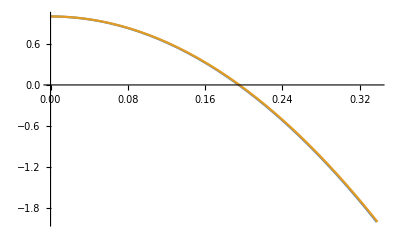

```mathematica
Module[{α=20,β=-15, γ=-10,μ=-1,δ=0.01},
Plot[{3/4 k (k (4 α+5 β+4 γ)-2 √2 δ)-μ,3/4 k (k (4 α+5 β+4 γ)+2 √2 δ)-μ},{k,0,0.5},PlotRange->{6,-2}]]
```

```mathematica
Hyperlink["Go to Hamiltonian sec",{SelectedNotebook[],"Ham"},Appearance->"DialogBox"]
Hyperlink["Go to ASOC sec",{SelectedNotebook[],"Inv"},Appearance->"DialogBox"]
Hyperlink["Go to Superconductor sec",{SelectedNotebook[],"Sup"},Appearance->"DialogBox"]
Hyperlink["Go to Eigen ASOC",{SelectedNotebook[],"EigenValASOC"},Appearance->"DialogBox"]
```

Go to Hamiltonian seca83bd7bc-d343-45a1-ad8d-73c046990475HamButtonDataHyperlinkHyperlinkActive

Go to ASOC seca83bd7bc-d343-45a1-ad8d-73c046990475InvButtonDataHyperlinkHyperlinkActive

Go to Superconductor seca83bd7bc-d343-45a1-ad8d-73c046990475SupButtonDataHyperlinkHyperlinkActive

Go to Eigen ASOCa83bd7bc-d343-45a1-ad8d-73c046990475EigenValASOCButtonDataHyperlinkHyperlinkActive

```mathematica
Hyperlink["Go to Hamiltonian sec",{SelectedNotebook[],"Ham"},Appearance->"DialogBox"]
Hyperlink["Go to ASOC sec",{SelectedNotebook[],"Inv"},Appearance->"DialogBox"]
Hyperlink["Go to Superconductor sec",{SelectedNotebook[],"Sup"},Appearance->"DialogBox"]
Hyperlink["Go to Eigen ASOC",{SelectedNotebook[],"EigenValASOC"},Appearance->"DialogBox"]

"Noe that please the whole code is 'DEPLOYED'.
The following code corresponds the usual Conjugate formalism where we have used it in the FullSimplify form with variables being defined as real constants. The above is much better and more efficient."
(*

"-------------------The whole Hamiltonian-------------------"
DiagH=FullSimplify[Conjugate[EvH].hkk0.Transpose[EvH],Element[{kx,ky,kz,β,γ,k,α,δ,μ},Reals]];

MatrixForm[DiagH]
MatrixForm[FullSimplify[Conjugate[EvH].Transpose[EvH],Element[{kx,ky,kz,β,γ,k,α,δ,μ},Reals]]]
"-------------------Projection to Valance bands-------------------"
VBEn=FullSimplify[Conjugate[ValanceBands].hkk0.Transpose[ValanceBands],Element[{kx,ky,kz,β,γ,k,α,δ,μ},Reals]];
MatrixForm[VBEn]
"-------------------Projection to conduction bands-------------------"
CBEn=FullSimplify[Conjugate[ConductionBands].hkk0.Transpose[ConductionBands],Element[{kx,ky,kz,β,γ,k,α,δ,μ},Reals]];
MatrixForm[CBEn]

"-----------------------------------------------------------------------------------------"




"-------------------The off-diagonal elements of the projection (Check your report numbered 40)-------------------"
VCN=FullSimplify[Conjugate[ConductionBands].hkk0.Transpose[ValanceBands],Element[{kx,ky,kz,β,γ,k,α,δ,μ},Reals]];
CVN=FullSimplify[Conjugate[ValanceBands].hkk0.Transpose[ConductionBands],Element[{kx,ky,kz,β,γ,k,α,δ,μ},Reals]];
Print["(V^†)_kH_(0 k)W_k","========>",MatrixForm[CVN]]
Print["(W^†)_kH_(0 k)V_k","========>",MatrixForm[VCN]]

"-----------------------------------------------------------------------------------------"
(*Hole Part ----Hole part*)
VB=Transpose[ValanceBands];
CB=Transpose[ConductionBands];
Hvb=FullSimplify[Transpose[VB].NHole.Conjugate[VB],Element[{kx,ky,kz,β,γ,k,α,δ,μ},Reals]];
Hcb=FullSimplify[Transpose[CB].NHole.Conjugate[CB],Element[{kx,ky,kz,β,γ,k,α,δ,μ},Reals]];
Print["(V^T)_-k(-(H^T)_0(-k))(v^(†T))_-k","========>",MatrixForm[Hvb]]
Print["(W^T)_-k(-(H^T)_0(-k))(W^(†T))_-k","========>",MatrixForm[Hcb]]


*)



FF[oo_]:=FullSimplify[oo,{Element[{kx,ky,kz,β,γ,k,α,δ,μ,δ0},Reals],kx>0,ky>0,kz>0,δ0>0}];
"-------------------The ASOC part-------------------"
(*Note that the below codes are not compatible with our new codes. Just look at the the  Conjugate[ValanceBands];
Below Below is correct.*)

(*kz=0;*)
(*kx=0;
ky=0;*)

HASO=δ0*(kx*(Sy.Sx.Sy-Sz.Sx.Sz) +  ky*(Sz.Sy.Sz-Sx.Sy.Sx)   +     kz*(Sx.Sz.Sx-Sy.Sz.Sy)       );
MatrixForm[FullSimplify[HASO]]

Rt=({{0, 0, 0, 1}, {0, 0, -1, 0}, {0, 1, 0, 0}, {-1, 0, 0, 0}});
Print["The odd-parity inversion pairing---->",MatrixForm[FullSimplify[HASO.Rt]]]

(*dV=FullSimplify[Transpose[Conjugate[ValanceBands]].HASO.ValanceBands,Element[{kx,ky,kz,β,γ,k,α,δ,μ,δ0},Reals]];
dC=FullSimplify[Transpose[Conjugate[ConductionBands]].HASO.ConductionBands,Element[{kx,ky,kz,β,γ,k,α,δ,μ,δ0},Reals]];

dVc=FullSimplify[Transpose[Conjugate[ValanceBands]].HASO.ConductionBands,Element[{kx,ky,kz,β,γ,k,α,δ,μ,δ0},Reals]];
dCv=FullSimplify[Transpose[Conjugate[ConductionBands]].HASO.ValanceBands,Element[{kx,ky,kz,β,γ,k,α,δ,μ,δ0},Reals]];*)



dV=FullSimplify[TrCj[ValanceBands].HASO.ValanceBands,{Element[{kx,ky,kz,β,γ,k,α,δ,μ,δ0},Reals],kx>0,ky>0,kz>0,δ0>0}];
dC=FullSimplify[TrCj[ConductionBands].HASO.ConductionBands,{Element[{kx,ky,kz,β,γ,k,α,δ,μ,δ0},Reals],kx>0,ky>0,kz>0,δ0>0}];

dVc=FullSimplify[TrCj[ValanceBands].HASO.ConductionBands,{Element[{kx,ky,kz,β,γ,k,α,δ,μ,δ0},Reals],kx>0,ky>0,kz>0,δ0>0}];
dCv=FullSimplify[TrCj[ConductionBands].HASO.ValanceBands,{Element[{kx,ky,kz,β,γ,k,α,δ,μ,δ0},Reals],kx>0,ky>0,kz>0,δ0>0}];



Print["(V^†)_kδ_(0  k)V_k","========>",MatrixForm[dV]]
Print["(V^†)_kδ_(0  k)V_k","========>",MatrixForm[FF[σDecomposition[dV  ]]]]

Print["(W^†)_kδ_(0  k)W_k","========>",MatrixForm[dC]]
Print["(V^†)_kδ_(0  k)V_k","========>",MatrixForm[FF[σDecomposition[dC  ]]]]


gapV=dV.(ⅈ*PauliMatrix[2]);

Print["GVV","========>",MatrixForm[FF[gapV.TrCj[gapV]]]]
Print["GVV","========>",MatrixForm[FF[σDecomposition[gapV.TrCj[gapV]]]]]
(*Print["wv(wv)dag","========>",MatrixForm[FF[dCv.dVc]]]*)

(*
Print["(V^†)_kδ_(0 k)W_k","========>",MatrixForm[dVc]]
Print["(W^†)_kδ_(0 k)V_k","========>",MatrixForm[dCv]]
Print["vw(vw)dag","========>",MatrixForm[FF[dVc.dCv]]]
Print["wv(wv)dag","========>",MatrixForm[FF[dCv.dVc]]]
*)








(*"--Δ^(++)--";
ΔLeM


"--Δ^(--)--";
ΔLe=


"--Δ^(-+)--";
ΔFe=*)


(*Print["InterBand pairing with corrections==",MatrixForm[FF[ΔFe+ΔLe.(-Transpose[dCv])+dVc.ΔLeM]]]

Print[Bg[192,192,192,{ii,txt[ii],"--Δ^(--)--",FinGapL,"--Δ^(++)--",FinGapLM,"--Δ^(+-)--",FinGapWV}]]*)

(*δ^vw(δ^vw)^d
δ^Wv(δ^Wv)^d*)
H11Perturb=VBEn+dV(*-(1/CBEn[[1,1]])*(dVc.dCv)*);
MatrixForm[FullSimplify[H11Perturb,{Element[{kx,ky,kz,β,γ,k,α,δ,μ,δ0},Reals],kx>0,ky>0,kz>0,δ0>0}]]
MatrixForm[FullSimplify[Eigenvalues[H11Perturb],{Element[{kx,ky,kz,β,γ,k,α,δ,μ,δ0},Reals],kx>0,ky>0,kz>0,δ0>0}]]


gg=Transpose[FF[Eigenvectors[H11Perturb]]];
MatrixForm[gg]
MatrixForm[FF[Inverse[gg].H11Perturb.gg]]

pai=({{0, (√3 (kx+ⅈ ky) √((kx^2+ky^2) (kx^2+ky^2+4 kz^2)) Δ)/(2 (kx-ⅈ ky) (kx^2+ky^2+kz^2))}, {(√3 (kx^2+ky^2)^(3/2) √(kx^2+ky^2+4 kz^2) Δ)/(2 (kx-ⅈ ky)^2 (kx^2+ky^2+kz^2)), 0}});
MatrixForm[FF[Inverse[gg].H11Perturb.gg]]

(*uio=({{(ⅈ (-kx^6 kz δ0-kx^4 ky^2 kz δ0+kx^2 ky^4 kz δ0+ky^6 kz δ0+8 kx^4 kz^3 δ0-8 ky^4 kz^3 δ0+(kx^2+ky^2) (kx^2+ky^2+4 kz^2) √(kx^4 (ky^2+kz^2)+ky^2 kz^2 (ky^2+kz^2)+kx^2 (ky^4-6 ky^2 kz^2+kz^4)) δ0))/((-kx+ⅈ ky)^2 (kx (-kx-ⅈ ky)^2 (-kx+ⅈ ky) ky+(-kx-ⅈ ky) (5 ⅈ kx^2+2 kx ky-5 ⅈ ky^2) kz^2-4 ⅈ (-kx+ⅈ ky) kz^4) δ0), (ⅈ (-kx^6 kz δ0-kx^4 ky^2 kz δ0+kx^2 ky^4 kz δ0+ky^6 kz δ0+8 kx^4 kz^3 δ0-8 ky^4 kz^3 δ0-(kx^2+ky^2) (kx^2+ky^2+4 kz^2) √(kx^4 (ky^2+kz^2)+ky^2 kz^2 (ky^2+kz^2)+kx^2 (ky^4-6 ky^2 kz^2+kz^4)) δ0))/((-kx+ⅈ ky)^2 (kx (-kx-ⅈ ky)^2 (-kx+ⅈ ky) ky+(-kx-ⅈ ky) (5 ⅈ kx^2+2 kx ky-5 ⅈ ky^2) kz^2-4 ⅈ (-kx+ⅈ ky) kz^4) δ0)}, {1, 1}});
MatrixForm[FF[Inverse[gg].pai.Transpose[Inverse[uio]]]]*)


(*Module[{kx=-kx,ky=-ky,kz=-kz},MatrixForm[({{(ⅈ (kx^6 kz δ0+kx^4 ky^2 kz δ0-kx^2 ky^4 kz δ0-ky^6 kz δ0-8 kx^4 kz^3 δ0+8 ky^4 kz^3 δ0+(kx^2+ky^2) (kx^2+ky^2+4 kz^2) √(kx^4 (ky^2+kz^2)+ky^2 kz^2 (ky^2+kz^2)+kx^2 (ky^4-6 ky^2 kz^2+kz^4)) δ0))/((kx-ⅈ ky)^2 (kx (kx-ⅈ ky) (kx+ⅈ ky)^2 ky+(kx+ⅈ ky) (5 ⅈ kx^2+2 kx ky-5 ⅈ ky^2) kz^2-4 ⅈ (kx-ⅈ ky) kz^4) δ0), (ⅈ (kx^6 kz δ0+kx^4 ky^2 kz δ0-kx^2 ky^4 kz δ0-ky^6 kz δ0-8 kx^4 kz^3 δ0+8 ky^4 kz^3 δ0-(kx^2+ky^2) (kx^2+ky^2+4 kz^2) √(kx^4 (ky^2+kz^2)+ky^2 kz^2 (ky^2+kz^2)+kx^2 (ky^4-6 ky^2 kz^2+kz^4)) δ0))/((kx-ⅈ ky)^2 (kx (kx-ⅈ ky) (kx+ⅈ ky)^2 ky+(kx+ⅈ ky) (5 ⅈ kx^2+2 kx ky-5 ⅈ ky^2) kz^2-4 ⅈ (kx-ⅈ ky) kz^4) δ0)}, {1, 1}})]]*)
(*kx=0;ky=0;*)


(*MatrixForm[FullSimplify[Eigenvectors[H11Perturb]]]




H11Perturb=VBEn+dV-(1/CBEn[[1,1]])*(dVc.dCv);
MatrixForm[FullSimplify[H11Perturb]]




hkk1=(α*ℏ^2*(kx^2+ky^2+kz^2)*I4-μ*I4+
β*(kx^2*(Sx.Sx)+ ky^2*(Sy.Sy)+kz^2*(Sz.Sz))+
γ*(  0*  kx* kx* (Sx.Sx)+ kx*ky* (Sx.Sy)+kx*kz* (Sx.Sz)+
      ky*kx* (Sy.Sx)+0*ky*ky* (Sy.Sy)+ky*kz* (Sy.Sz)+
      kz*kx* (Sz.Sx)+   kz*ky* (Sz.Sy)+0* kz*kz* (Sz.Sz)
                                                     )+
δ0*(kx*(Sy.Sx.Sy-Sz.Sx.Sz) +  ky*(Sz.Sy.Sz-Sx.Sy.Sx)   +     kz*(Sx.Sz.Sx-Sy.Sz.Sy)       )
 );
MatrixForm[FullSimplify[Eigenvalues[hkk1]]]

*)
```

Go to Hamiltonian secks37g_shmHamButtonDataHyperlinkHyperlinkActive

Go to ASOC secks37g_shmInvButtonDataHyperlinkHyperlinkActive

Go to Superconductor secks37g_shmSupButtonDataHyperlinkHyperlinkActive

Noe that please the whole code is 'DEPLOYED'.
The following code corresponds the usual Conjugate formalism where we have used it in the FullSimplify form with variables being defined as real constants. The above is much better and more efficient.

-------------------The ASOC part-------------------

(0 | 0 | 1/2 √3 kz δ0 | 0
0 | 0 | 0 | -1/2 √3 kz δ0
1/2 √3 kz δ0 | 0 | 0 | 0
0 | -1/2 √3 kz δ0 | 0 | 0)

The odd-parity inversion pairing---->(0 | 1/2 √3 kz δ0 | 0 | 0
1/2 √3 kz δ0 | 0 | 0 | 0
0 | 0 | 0 | 1/2 √3 kz δ0
0 | 0 | 1/2 √3 kz δ0 | 0)

FullSimplify::fas: Warning: one or more assumptions evaluated to False.

(V^†)_kδ_(0  k)V_k========>(0 | 0
0 | 0)

FullSimplify::fas: Warning: one or more assumptions evaluated to False.

(V^†)_kδ_(0  k)V_k========>(0
0
0
0)

(W^†)_kδ_(0  k)W_k========>(0 | 0
0 | 0)

FullSimplify::fas: Warning: one or more assumptions evaluated to False.

(V^†)_kδ_(0  k)V_k========>(0
0
0
0)

FullSimplify::fas: Warning: one or more assumptions evaluated to False.

GVV========>(0 | 0
0 | 0)

FullSimplify::fas: Warning: one or more assumptions evaluated to False.

GVV========>(0
0
0
0)

FullSimplify::fas: Warning: one or more assumptions evaluated to False.

(kz^2 (α+β/4)-μ | 0
0 | kz^2 (α+β/4)-μ)

FullSimplify::fas: Warning: one or more assumptions evaluated to False.

(kz^2 (α+β/4)-μ
kz^2 (α+β/4)-μ)

FullSimplify::fas: Warning: one or more assumptions evaluated to False.

(0 | 1
1 | 0)

FullSimplify::fas: Warning: one or more assumptions evaluated to False.

(kz^2 (α+β/4)-μ | 0
0 | kz^2 (α+β/4)-μ)

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 √3 Δ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 2 √3 √(kz^2) Δ ComplexInfinity encountered.

FullSimplify::fas: Warning: one or more assumptions evaluated to False.

(kz^2 (α+β/4)-μ | 0
0 | kz^2 (α+β/4)-μ)

```mathematica
Expand[kx^4 (ky^2+kz^2)+ky^2 kz^2 (ky^2+kz^2)+kx^2 (ky^4-6 ky^2 kz^2+kz^4)]
```

```mathematica
kx^4 ky^2+ky^4 kz^2+kz^4 kx^2 +

kx^4 kz^2+ ky^4 kx^2+ kz^4 ky^2

-6 kx^2 ky^2 kz^2+
```

```mathematica
invPa={{e, 0}, {0, e}}+x*PauliMatrix[1]+y*PauliMatrix[2]+z*PauliMatrix[3];
MatrixForm[invPa]
MatrixForm[FullSimplify[Eigenvalues[invPa]]]
MatrixForm[FullSimplify[Det[invPa]]]
MatrixForm[FullSimplify[Inverse[invPa]]]
```

(e+z | x-ⅈ y
x+ⅈ y | e-z)

(e-√(x^2+y^2+z^2)
e+√(x^2+y^2+z^2))

e^2-x^2-y^2-z^2

((-e+z)/(-e^2+x^2+y^2+z^2) | (x-ⅈ y)/(-e^2+x^2+y^2+z^2)
(x+ⅈ y)/(-e^2+x^2+y^2+z^2) | -(e+z)/(-e^2+x^2+y^2+z^2))

```mathematica
Module[{x=0,y=0,Ξ=0,Ψ=0,z=0,Ζ=0},(*{},*)MatrixForm[FullSimplify[Eigenvalues[{{e+z, x-ⅈ y, Δ1, Δ2}, {x+ⅈ y, e-z, Δ3, Δ4}, {Δ1d, Δ3d, -e+z, x+ⅈ y}, {Δ2d, Δ4d, x-ⅈ y, -e-z}}]]]]
```

(-(√(2 e^2+Δ1 Δ1d+Δ2 Δ2d+Δ3 Δ3d+Δ4 Δ4d-√(Δ1^2 Δ1d^2+Δ2^2 Δ2d^2+4 Δ1 Δ2d Δ3d Δ4+2 Δ1 Δ1d (Δ2 Δ2d+Δ3 Δ3d-Δ4 Δ4d)+(Δ3 Δ3d+Δ4 Δ4d)^2+Δ2 (-2 Δ2d Δ3 Δ3d+4 Δ1d Δ3 Δ4d+2 Δ2d Δ4 Δ4d))))/(√2)
(√(2 e^2+Δ1 Δ1d+Δ2 Δ2d+Δ3 Δ3d+Δ4 Δ4d-√(Δ1^2 Δ1d^2+Δ2^2 Δ2d^2+4 Δ1 Δ2d Δ3d Δ4+2 Δ1 Δ1d (Δ2 Δ2d+Δ3 Δ3d-Δ4 Δ4d)+(Δ3 Δ3d+Δ4 Δ4d)^2+Δ2 (-2 Δ2d Δ3 Δ3d+4 Δ1d Δ3 Δ4d+2 Δ2d Δ4 Δ4d))))/(√2)
-(√(2 e^2+Δ1 Δ1d+Δ2 Δ2d+Δ3 Δ3d+Δ4 Δ4d+√(Δ1^2 Δ1d^2+Δ2^2 Δ2d^2+4 Δ1 Δ2d Δ3d Δ4+2 Δ1 Δ1d (Δ2 Δ2d+Δ3 Δ3d-Δ4 Δ4d)+(Δ3 Δ3d+Δ4 Δ4d)^2+Δ2 (-2 Δ2d Δ3 Δ3d+4 Δ1d Δ3 Δ4d+2 Δ2d Δ4 Δ4d))))/(√2)
(√(2 e^2+Δ1 Δ1d+Δ2 Δ2d+Δ3 Δ3d+Δ4 Δ4d+√(Δ1^2 Δ1d^2+Δ2^2 Δ2d^2+4 Δ1 Δ2d Δ3d Δ4+2 Δ1 Δ1d (Δ2 Δ2d+Δ3 Δ3d-Δ4 Δ4d)+(Δ3 Δ3d+Δ4 Δ4d)^2+Δ2 (-2 Δ2d Δ3 Δ3d+4 Δ1d Δ3 Δ4d+2 Δ2d Δ4 Δ4d))))/(√2))

```mathematica
MatrixForm[Transpose[ValanceBands]]
```

(0 | -1/2 | 0 | (√3)/2
-(√3)/2 | 0 | 1/2 | 0)

```mathematica
F[oo_]:=FullSimplify[oo,Element[{kx,ky,kz,Δ,α,β,γ,k,μ,α,ϵ,δ,Mx,My,Mz},Reals]];

"Magnetic field into the band basis"

Clear[Mx,My,Mz];
My=0;
Mz=0;
Zeeman=Mx*Sx+My*Sy +Mz*Sz;
MatrixForm[F[Zeeman]]
(*
CnjVl   ValanceBands
CnjCo   ConductionBands*)



dV=F[CnjVl.Zeeman.ValanceBands];

dC=F[CnjCo.Zeeman.ConductionBands];

dVc=F[CnjVl.Zeeman.ConductionBands];
dCv=F[CnjCo.Zeeman.ValanceBands];



Print["vv","========>",MatrixForm[dV]]

Print["ww"<>,"========>",MatrixForm[dC]]
Print["vw","========>",MatrixForm[dVc]]
Print["wv","========>",MatrixForm[dCv]]
Print[(*"(V^†)_k Z Subscript[W, k](W^†)_k Subscript[ZV, k]",*)"========>",MatrixForm[F[dVc.dCv]]]


MatrixForm[VBEn]
H11Perturb=VBEn+dV-0*(1/CBEn[[1,1]])*(dVc.dCv);
(*kx=0;ky=0;*)

MatrixForm[FullSimplify[H11Perturb]]
```

(0 | (√3 Mx)/2 | 0 | 0
(√3 Mx)/2 | 0 | Mx | 0
0 | Mx | 0 | (√3 Mx)/2
0 | 0 | (√3 Mx)/2 | 0)

vv========>(0 | Mx
Mx | 0)

ww========>(0 | 0
0 | 0)

vw========>((√3 Mx)/2 | 0
0 | (√3 Mx)/2)

wv========>((√3 Mx)/2 | 0
0 | (√3 Mx)/2)

========>((3 Mx^2)/4 | 0
0 | (3 Mx^2)/4)

(kz^2 (α+β/4)-μ | 0
0 | kz^2 (α+β/4)-μ)

(kz^2 (α+β/4)-μ | Mx
Mx | kz^2 (α+β/4)-μ)

```mathematica
dV
```

{{-(3 kx kz Mx)/(2 (kx^2+ky^2+kz^2)),((kx+ⅈ ky) (kx^2-3 ⅈ kx ky-2 (ky^2+kz^2)) Mx)/(2 (kx-ⅈ ky) (kx^2+ky^2+kz^2))},{((kx-ⅈ ky) (kx^2+3 ⅈ kx ky-2 (ky^2+kz^2)) Mx)/(2 (kx+ⅈ ky) (kx^2+ky^2+kz^2)),(3 kx kz Mx)/(2 (kx^2+ky^2+kz^2))}}

```mathematica
F[oo_]:=FullSimplify[oo,Element[{kx,ky,kz,Δ,α,β,γ,k,μ,α,ϵ,δ},Reals]];

HSSOC=γγ*(  0*  kx* kx* (Sx.Sx)+ kx*ky* (Sx.Sy)+kx*kz* (Sx.Sz)+
      ky*kx* (Sy.Sx)+0*ky*ky* (Sy.Sy)+ky*kz* (Sy.Sz)+
      kz*kx* (Sz.Sx)+   kz*ky* (Sz.Sy)+0* kz*kz* (Sz.Sz)
                                                     );
MatrixForm[F[HSSOC]]
(*
CnjVl   ValanceBands
CnjCo   ConductionBands*)



dV=F[CnjVl.HSSOC.ValanceBands];
dC=F[CnjCo.HSSOC.ConductionBands];

dVc=F[CnjVl.HSSOC.ConductionBands];
dCv=F[CnjCo.HSSOC.ValanceBands];



Print["(V^†)_kγγV_k","========>",MatrixForm[dV]]
Print["(W^†)_kγγW_k","========>",MatrixForm[dC]]
Print["(V^†)_kγγW_k","========>",MatrixForm[dVc]]
Print["(W^†)_kγγV_k","========>",MatrixForm[dCv]]
Print["(V^†)_kγγW_k(W^†)_kγγV_k","========>",MatrixForm[F[dVc.dCv]]]


MatrixForm[VBEn]
(*H11Perturb=VBEn+dV-(1/CBEn[[1,1]])*(dVc.dCv);
MatrixForm[FullSimplify[H11Perturb]]




hkk1=(α*ℏ^2*(kx^2+ky^2+kz^2)*I4-μ*I4+
β*(kx^2*(Sx.Sx)+ ky^2*(Sy.Sy)+kz^2*(Sz.Sz))+
γ*(  0*  kx* kx* (Sx.Sx)+ kx*ky* (Sx.Sy)+kx*kz* (Sx.Sz)+
      ky*kx* (Sy.Sx)+0*ky*ky* (Sy.Sy)+ky*kz* (Sy.Sz)+
      kz*kx* (Sz.Sx)+   kz*ky* (Sz.Sy)+0* kz*kz* (Sz.Sz)
                                                     )+
δ0*(kx*(Sy.Sx.Sy-Sz.Sx.Sz) +  ky*(Sz.Sy.Sz-Sx.Sy.Sx)   +     kz*(Sx.Sz.Sx-Sy.Sz.Sy)       )
 );
MatrixForm[FullSimplify[Eigenvalues[hkk1]]]*)
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(V^†)_kγγV_k========>(0 | 0
0 | 0)

(W^†)_kγγW_k========>(0 | 0
0 | 0)

(V^†)_kγγW_k========>(0 | 0
0 | 0)

(W^†)_kγγV_k========>(0 | 0
0 | 0)

(V^†)_kγγW_k(W^†)_kγγV_k========>(0 | 0
0 | 0)

(kx^2 (α+β/4)-μ | 0
0 | kx^2 (α+β/4)-μ)

```mathematica
(kx^2+ky^2+kz^2) α+5/4 (kx^2+ky^2+kz^2) β-√(kx^4+ky^4-ky^2 kz^2+kz^4-kx^2 (ky^2+kz^2)) β-μ-(1/Em)*3 (ky^2 kz^2+kx^2 (ky^2+kz^2)) γγ^2
```

```mathematica
FullSimplify[(kx^2 (α+β/4)-μ)(kx^2 (α+(9 β)/4)-μ)]
```

(kx^2 (α+β/4)-μ) (kx^2 (α+(9 β)/4)-μ)

```mathematica
Expand[(kx^2 α1-μ)(kx^2 α2-μ)]
```

kx^4 α1 α2-kx^2 α1 μ-kx^2 α2 μ+μ^2

```mathematica
.
```

```mathematica
({{(kx^4 β^2+ky^4 β^2-2 kz^2 β (kz^2 β+√((kx^4-kx^2 ky^2+ky^4-(kx^2+ky^2) kz^2+kz^4) β^2+3 (kx^2 ky^2+(kx^2+ky^2) kz^2) γ^2))+ky^2 (2 kz^2 (β^2-6 γ^2)+β √((kx^4-kx^2 ky^2+ky^4-(kx^2+ky^2) kz^2+kz^4) β^2+3 (kx^2 ky^2+(kx^2+ky^2) kz^2) γ^2))+kx^2 (2 kz^2 (β^2-6 γ^2)+ky^2 (-4 β^2+6 γ^2)+β √((kx^4-kx^2 ky^2+ky^4-(kx^2+ky^2) kz^2+kz^4) β^2+3 (kx^2 ky^2+(kx^2+ky^2) kz^2) γ^2)))/(2 (-2 kx^4 β^2-2 ky^4 β^2-2 kz^2 β (kz^2 β+√((kx^4-kx^2 ky^2+ky^4-(kx^2+ky^2) kz^2+kz^4) β^2+3 (kx^2 ky^2+(kx^2+ky^2) kz^2) γ^2))+ky^2 (2 kz^2 (β^2-3 γ^2)+β √((kx^4-kx^2 ky^2+ky^4-(kx^2+ky^2) kz^2+kz^4) β^2+3 (kx^2 ky^2+(kx^2+ky^2) kz^2) γ^2))+kx^2 (2 (ky^2+kz^2) (β^2-3 γ^2)+β √((kx^4+ky^4-ky^2 kz^2+kz^4-kx^2 (ky^2+kz^2)) β^2+3 (ky^2 kz^2+kx^2 (ky^2+kz^2)) γ^2))))}, {(kx^4 β^2+ky^4 β^2-2 kz^2 β (kz^2 β+√((kx^4-kx^2 ky^2+ky^4-(kx^2+ky^2) kz^2+kz^4) β^2+3 (kx^2 ky^2+(kx^2+ky^2) kz^2) γ^2))+ky^2 (2 kz^2 (β^2-6 γ^2)+β √((kx^4-kx^2 ky^2+ky^4-(kx^2+ky^2) kz^2+kz^4) β^2+3 (kx^2 ky^2+(kx^2+ky^2) kz^2) γ^2))+kx^2 (2 kz^2 (β^2-6 γ^2)+ky^2 (-4 β^2+6 γ^2)+β √((kx^4-kx^2 ky^2+ky^4-(kx^2+ky^2) kz^2+kz^4) β^2+3 (kx^2 ky^2+(kx^2+ky^2) kz^2) γ^2)))/(4 (kx^4+ky^4-ky^2 kz^2+kz^4-kx^2 (ky^2+kz^2)) β^2+12 (ky^2 kz^2+kx^2 (ky^2+kz^2)) γ^2-2 (kx^2+ky^2-2 kz^2) β √((kx^4+ky^4-ky^2 kz^2+kz^4-kx^2 (ky^2+kz^2)) β^2+3 (ky^2 kz^2+kx^2 (ky^2+kz^2)) γ^2))}, {(-kx^4 β^2-ky^4 β^2+2 kz^2 β (kz^2 β-√((kx^4-kx^2 ky^2+ky^4-(kx^2+ky^2) kz^2+kz^4) β^2+3 (kx^2 ky^2+(kx^2+ky^2) kz^2) γ^2))+ky^2 (-2 kz^2 (β^2-6 γ^2)+β √((kx^4-kx^2 ky^2+ky^4-(kx^2+ky^2) kz^2+kz^4) β^2+3 (kx^2 ky^2+(kx^2+ky^2) kz^2) γ^2))+kx^2 (-2 kz^2 (β^2-6 γ^2)+ky^2 (4 β^2-6 γ^2)+β √((kx^4-kx^2 ky^2+ky^4-(kx^2+ky^2) kz^2+kz^4) β^2+3 (kx^2 ky^2+(kx^2+ky^2) kz^2) γ^2)))/(2 (2 kx^4 β^2+2 (ky^4-ky^2 kz^2+kz^4) β^2+6 ky^2 kz^2 γ^2-2 kx^2 (ky^2+kz^2) (β^2-3 γ^2)+kx^2 β √((kx^4+ky^4-ky^2 kz^2+kz^4-kx^2 (ky^2+kz^2)) β^2+3 (ky^2 kz^2+kx^2 (ky^2+kz^2)) γ^2)+ky^2 β √((kx^4+ky^4-ky^2 kz^2+kz^4-kx^2 (ky^2+kz^2)) β^2+3 (ky^2 kz^2+kx^2 (ky^2+kz^2)) γ^2)-2 kz^2 β √((kx^4+ky^4-ky^2 kz^2+kz^4-kx^2 (ky^2+kz^2)) β^2+3 (ky^2 kz^2+kx^2 (ky^2+kz^2)) γ^2)))}, {(kx^4 β^2+ky^4 β^2+2 kz^2 β (-kz^2 β+√((kx^4-kx^2 ky^2+ky^4-(kx^2+ky^2) kz^2+kz^4) β^2+3 (kx^2 ky^2+(kx^2+ky^2) kz^2) γ^2))+ky^2 (2 kz^2 (β^2-6 γ^2)-β √((kx^4-kx^2 ky^2+ky^4-(kx^2+ky^2) kz^2+kz^4) β^2+3 (kx^2 ky^2+(kx^2+ky^2) kz^2) γ^2))-kx^2 (-2 kz^2 (β^2-6 γ^2)+ky^2 (4 β^2-6 γ^2)+β √((kx^4-kx^2 ky^2+ky^4-(kx^2+ky^2) kz^2+kz^4) β^2+3 (kx^2 ky^2+(kx^2+ky^2) kz^2) γ^2)))/(4 (kx^4+ky^4-ky^2 kz^2+kz^4-kx^2 (ky^2+kz^2)) β^2+12 (ky^2 kz^2+kx^2 (ky^2+kz^2)) γ^2+2 (kx^2+ky^2-2 kz^2) β √((kx^4+ky^4-ky^2 kz^2+kz^4-kx^2 (ky^2+kz^2)) β^2+3 (ky^2 kz^2+kx^2 (ky^2+kz^2)) γ^2))}})&&({{-(3 ky kz γ)/(2 √((kx^4+ky^4-ky^2 kz^2+kz^4-kx^2 (ky^2+kz^2)) β^2+3 (ky^2 kz^2+kx^2 (ky^2+kz^2)) γ^2))}, {(3 ky kz γ)/(2 √((kx^4+ky^4-ky^2 kz^2+kz^4-kx^2 (ky^2+kz^2)) β^2+3 (ky^2 kz^2+kx^2 (ky^2+kz^2)) γ^2))}, {(3 ky kz γ)/(2 √((kx^4+ky^4-ky^2 kz^2+kz^4-kx^2 (ky^2+kz^2)) β^2+3 (ky^2 kz^2+kx^2 (ky^2+kz^2)) γ^2))}, {-(3 ky kz γ)/(2 √((kx^4+ky^4-ky^2 kz^2+kz^4-kx^2 (ky^2+kz^2)) β^2+3 (ky^2 kz^2+kx^2 (ky^2+kz^2)) γ^2))}})&&({{-(3 kx kz γ)/(2 √((kx^4+ky^4-ky^2 kz^2+kz^4-kx^2 (ky^2+kz^2)) β^2+3 (ky^2 kz^2+kx^2 (ky^2+kz^2)) γ^2))}, {(3 kx kz γ)/(2 √((kx^4+ky^4-ky^2 kz^2+kz^4-kx^2 (ky^2+kz^2)) β^2+3 (ky^2 kz^2+kx^2 (ky^2+kz^2)) γ^2))}, {(3 kx kz γ)/(2 √((kx^4+ky^4-ky^2 kz^2+kz^4-kx^2 (ky^2+kz^2)) β^2+3 (ky^2 kz^2+kx^2 (ky^2+kz^2)) γ^2))}, {-(3 kx kz γ)/(2 √((kx^4+ky^4-ky^2 kz^2+kz^4-kx^2 (ky^2+kz^2)) β^2+3 (ky^2 kz^2+kx^2 (ky^2+kz^2)) γ^2))}})
```

```mathematica
"This is the condition where the finite energy crossing happens E_+=-E_-"
({{1/4 ((kx^2+ky^2+kz^2) (4 α+5 β)-4 (√((kx^4+ky^4-ky^2 kz^2+kz^4-kx^2 (ky^2+kz^2)) β^2+3 (ky^2 kz^2+kx^2 (ky^2+kz^2)) γ^2)+μ))}, {1/4 ((kx^2+ky^2+kz^2) (4 α+5 β)-4 (√((kx^4+ky^4-ky^2 kz^2+kz^4-kx^2 (ky^2+kz^2)) β^2+3 (ky^2 kz^2+kx^2 (ky^2+kz^2)) γ^2)+μ))}, {1/4 (kx^2+ky^2+kz^2) (4 α+5 β)+√((kx^4+ky^4-ky^2 kz^2+kz^4-kx^2 (ky^2+kz^2)) β^2+3 (ky^2 kz^2+kx^2 (ky^2+kz^2)) γ^2)-μ}, {1/4 (kx^2+ky^2+kz^2) (4 α+5 β)+√((kx^4+ky^4-ky^2 kz^2+kz^4-kx^2 (ky^2+kz^2)) β^2+3 (ky^2 kz^2+kx^2 (ky^2+kz^2)) γ^2)-μ}})
FullSimplify[1/4 (kx^2+ky^2+kz^2) (4 α+5 β)+√((kx^4+ky^4-ky^2 kz^2+kz^4-kx^2 (ky^2+kz^2)) β^2+3 (ky^2 kz^2+kx^2 (ky^2+kz^2)) γ^2)-μ==-1/4 ((kx^2+ky^2+kz^2) (4 α+5 β)-4 (√((kx^4+ky^4-ky^2 kz^2+kz^4-kx^2 (ky^2+kz^2)) β^2+3 (ky^2 kz^2+kx^2 (ky^2+kz^2)) γ^2)+μ))]

FullSimplify[1/4 (kx^2+ky^2+kz^2) (4 α+5 β)+√((kx^4+ky^4-ky^2 kz^2+kz^4-kx^2 (ky^2+kz^2)) β^2+3 (ky^2 kz^2+kx^2 (ky^2+kz^2)) γ^2)-μ+1/4 (kx^2+ky^2+kz^2) (4 α+5 β)-(√((kx^4+ky^4-ky^2 kz^2+kz^4-kx^2 (ky^2+kz^2)) β^2+3 (ky^2 kz^2+kx^2 (ky^2+kz^2)) γ^2)+μ)==0]

FullSimplify[1/2 (kx^2+ky^2+kz^2) (4 α+5 β)-μ==0]

"This is the finite energy crossing point"
"E_++E_-=1/2 (kx^2+ky^2+kz^2) (4 α+5 β)-2μ"
(kx^2+ky^2+kz^2)=(4μ)/(4 α+5 β)
1/(EE+Abs[(4βμ)/(4 α+5 β)])^2
```

```mathematica
α=2;β=2;μ=2;
EE=Abs[(4β*μ)/(4 α+5 β)];
N[1/(EE+Abs[(4β*μ)/(4 α+5 β)])^2]
```

0.316406

```mathematica
"Finite energy regime where pairing happens";
(*(kx^2+ky^2+kz^2)->(4μ)/(4 α+5 β)*)
(*1/4 (kx^2+ky^2+kz^2) (4 α+5 β)+√((kx^4+ky^4-ky^2 kz^2+kz^4-kx^2 (ky^2+kz^2)) β^2+3 (ky^2 kz^2+kx^2 (ky^2+kz^2)) γ^2)-μ*)
Efin=√((kx^4+ky^4-ky^2 kz^2+kz^4-kx^2 (ky^2+kz^2)) β^2+3 (ky^2 kz^2+kx^2 (ky^2+kz^2)) γ^2);
"Two-fold rotation axis"
Module[{kx=k,ky=0,kz=0},{(kx^2+ky^2+kz^2)==(4μ)/(4 α+5 β),FullSimplify[√((kx^4+ky^4-ky^2 kz^2+kz^4-kx^2 (ky^2+kz^2)) β^2+3 (ky^2 kz^2+kx^2 (ky^2+kz^2)) γ^2)]}]
"σ_d plane or on C_2' axis"
Module[{kx=k,ky=k,kz=0},{FullSimplify[(kx^2+ky^2+kz^2)==(4μ)/(4 α+5 β)],FullSimplify[√((kx^4+ky^4-ky^2 kz^2+kz^4-kx^2 (ky^2+kz^2)) β^2+3 (ky^2 kz^2+kx^2 (ky^2+kz^2)) γ^2)]}]
"on C_3 axis"
Module[{kx=k,ky=k,kz=k},{FullSimplify[(kx^2+ky^2+kz^2)==(4μ)/(4 α+5 β)],FullSimplify[√((kx^4+ky^4-ky^2 kz^2+kz^4-kx^2 (ky^2+kz^2)) β^2+3 (ky^2 kz^2+kx^2 (ky^2+kz^2)) γ^2)]}]
```

Two-fold rotation axis

{k^2==(4 μ)/(4 α+5 β),√(k^4 β^2)}

σ_d plane or on C_2' axis

{k^2==(2 μ)/(4 α+5 β),√(k^4 (β^2+3 γ^2))}

on C_3 axis

{3 k^2==(4 μ)/(4 α+5 β),3 √(k^4 γ^2)}

```mathematica
Hyperlink["Go to Hamiltonian sec",{SelectedNotebook[],"Ham"},Appearance->"DialogBox"]
Hyperlink["Go to ASOC sec",{SelectedNotebook[],"Inv"},Appearance->"DialogBox"]
Hyperlink["Go to Superconductor sec",{SelectedNotebook[],"Sup"},Appearance->"DialogBox"]
Hyperlink["Go to Eigen ASOC",{SelectedNotebook[],"EigenValASOC"},Appearance->"DialogBox"]
```

Go to Hamiltonian seca83bd7bc-d343-45a1-ad8d-73c046990475HamButtonDataHyperlinkHyperlinkActive

Go to ASOC seca83bd7bc-d343-45a1-ad8d-73c046990475InvButtonDataHyperlinkHyperlinkActive

Go to Superconductor seca83bd7bc-d343-45a1-ad8d-73c046990475SupButtonDataHyperlinkHyperlinkActive

Go to Eigen ASOCa83bd7bc-d343-45a1-ad8d-73c046990475EigenValASOCButtonDataHyperlinkHyperlinkActive

```mathematica
Hyperlink["Go to Hamiltonian sec",{SelectedNotebook[],"Ham"},Appearance->"DialogBox"]
Hyperlink["Go to ASOC sec",{SelectedNotebook[],"Inv"},Appearance->"DialogBox"]
Hyperlink["Go to Superconductor sec",{SelectedNotebook[],"Sup"},Appearance->"DialogBox"]
Hyperlink["Go to Eigen ASOC",{SelectedNotebook[],"EigenValASOC"},Appearance->"DialogBox"]

		

Array[Supr,50];
Array[txt,50];

(*kx=0;
ky=0;*)
"--------------------Singlet-------------------------------------------";
txt[1]="|A_1>_11";
Supr[1]=Δ({{0, 0, -1/2 √3 (kx-ⅈ ky), (3 kz)/2}, {0, (kx-ⅈ ky), -kz/2, (√3 (kx+ⅈ ky))/2}, {-1/2 √3 (kx-ⅈ ky), -kz/2, -(kx+ⅈ ky), 0}, {(3 kz)/2, (√3 (kx+ⅈ ky))/2, 0, 0}});

"--------------------Triplet-------------------------------------------";
txt[2]="|x>";

Supr[2]=Δ({{0, 0, √3 kz, 3 ⅈ*ky}, {0, -2 kz, -ⅈ* ky, √3 kz}, {√3 kz, -ⅈ *ky, -2 kz, 0}, {3 ⅈ*ky, √3 kz, 0, 0}});
txt[3]="|y>";
Supr[3]=Δ({{0, 0, -√3 kz, -3 kx}, {0, 2 kz, kx, √3 kz}, {-√3 kz, kx, -2 kz, 0}, {-3 kx, √3 kz, 0, 0}});
txt[4]="|z>";
Supr[4]=Δ({{0, 0, kx-ⅈ*ky, 0}, {0, -2/(√3)(kx-ⅈ*ky), 0, kx+ⅈ*ky}, {kx-ⅈ*ky, 0, -2/(√3)(kx+ⅈ*ky), 0}, {0, kx+ⅈ*ky, 0, 0}});
"--------------------Quintet (L=1,S=3)-------------------------------------------";


txt[5]="|3z^2-r^2>_3";
Supr[5]=Δ({{0, 0, (kx-ⅈ*ky)/(√3), -kz/2}, {0, kx-ⅈ ky, -(3  kz)/2, -(kx+ⅈ ky)/(√3)}, {(kx-ⅈ ky)/(√3), -(3  kz)/2, -kx-ⅈ ky, 0}, {-kz/2, -(kx+ⅈ ky)/(√3), 0, 0}});

txt[6]="|3z^2-r^2>_1";
Supr[6]=Δ({{0, 0, 1/2 √3 (kx-ⅈ ky), 3 kz}, {0, -kx+ⅈ ky, -kz, -1/2 √3 (kx+ⅈ ky)}, {1/2 √3 (kx-ⅈ ky), -kz, kx+ⅈ ky, 0}, {3 kz, -1/2 √3 (kx+ⅈ ky), 0, 0}});





txt[7]="|x^2-y^2>_3";
Supr[7]=Δ({{5 √3 (kx-ⅈ ky), -5 kz, -kx-ⅈ ky, 0}, {-5 kz, -√3 (kx+ⅈ ky), 0, kx-ⅈ ky}, {-kx-ⅈ ky, 0, √3 (kx-ⅈ ky), -5 kz}, {0, kx-ⅈ ky, -5 kz, -5 √3 (kx+ⅈ ky)}});

txt[8]="|x^2-y^2>_1";
Supr[8]=Δ({{0, 0, -kx-ⅈ ky, 0}, {0, (2 (kx+ⅈ ky))/(√3), 0, kx-ⅈ ky}, {-kx-ⅈ ky, 0, -(2 (kx-ⅈ ky))/(√3), 0}, {0, kx-ⅈ ky, 0, 0}});





txt[9]="|xy>_3";
Supr[9]=Δ({{-5 √3 (kx-ⅈ ky), 5 kz, kx+ⅈ ky, 0}, {5 kz, √3 (kx+ⅈ ky), 0, kx-ⅈ ky}, {kx+ⅈ ky, 0, √3 (kx-ⅈ ky), -5 kz}, {0, kx-ⅈ ky, -5 kz, -5 √3 (kx+ⅈ ky)}});
txt[10]="|xy>_1";
Supr[10]=Δ({{0, 0, -√3 (kx+ⅈ ky), 0}, {0, 2 (kx+ⅈ ky), 0, -√3 (kx-ⅈ ky)}, {-√3 (kx+ⅈ ky), 0, 2 (kx-ⅈ ky), 0}, {0, -√3 (kx-ⅈ ky), 0, 0}});




txt[11]="|zx>_3";
Supr[11]=Δ({{0, -5 kx+5 ⅈ ky, 4 kz, √3 kx}, {-5 kx+5 ⅈ ky, 4 √3 kz, 3 √3 kx, -4 kz}, {4 kz, 3 √3 kx, -4 √3 kz, -5 (kx+ⅈ ky)}, {√3 kx, -4 kz, -5 (kx+ⅈ ky), 0}});
txt[12]="|zx>_1";
Supr[12]=Δ({{0, 0, -√3 kz, 3 kx}, {0, 2 kz, -kx, √3 kz}, {-√3 kz, -kx, -2 kz, 0}, {3 kx, √3 kz, 0, 0}});



txt[13]="|yz>_3";
Supr[13]=Δ({{0, 5 (kx-ⅈ ky), -4 kz, -ⅈ √3 ky}, {5 (kx-ⅈ ky), -4 √3 kz, -3 ⅈ √3 ky, -4 kz}, {-4 kz, -3 ⅈ √3 ky, -4 √3 kz, -5 (kx+ⅈ ky)}, {-ⅈ √3 ky, -4 kz, -5 (kx+ⅈ ky), 0}});

txt[14]="|yz>_1";
Supr[14]=Δ({{0, 0, √3 kz, -3 ⅈ ky}, {0, -2 kz, ⅈ ky, √3 kz}, {√3 kz, ⅈ ky, -2 kz, 0}, {-3 ⅈ ky, √3 kz, 0, 0}});





"--------------------Septet-------------------------------------------";
txt[15]="|xyz>_13";
Supr[15]=Δ({{(3(kx-ⅈ*ky))/4, (√3 kz)/2, (√3 (kx+ⅈ*ky))/4, 0}, {(√3 kz)/2, (3 (kx+ⅈ*ky))/4, 0, -1/4 √3 (kx-ⅈ*ky)}, {(√3(kx+ⅈ*ky))/4, 0, -(3 (kx-ⅈ*ky))/4, (√3 kz)/2}, {0, -1/4 √3(kx-ⅈ*ky), (√3 kz)/2, -(3(kx+ⅈ*ky))/4}});


"The odd-parity inversion pairing---->"({{3/4 (kx-ⅈ ky) δ0, 1/2 √3 kz δ0, 1/4 √3 (kx+ⅈ ky) δ0, 0}, {1/2 √3 kz δ0, 3/4 (kx+ⅈ ky) δ0, 0, -1/4 √3 (kx-ⅈ ky) δ0}, {1/4 √3 (kx+ⅈ ky) δ0, 0, -3/4 (kx-ⅈ ky) δ0, 1/2 √3 kz δ0}, {0, -1/4 √3 (kx-ⅈ ky) δ0, 1/2 √3 kz δ0, -3/4 (kx+ⅈ ky) δ0}});





txt[16]="|x^3>_13";
Supr[16]=Δ({{5 √3 kz, 5 ⅈ* ky, -kz, -ⅈ* √3 ky}, {5 ⅈ* ky, -√3 kz, -3 ⅈ *√3 ky, -kz}, {-kz, -3 ⅈ *√3 ky, -√3 kz, 5 ⅈ* ky}, {-ⅈ* √3 ky, -kz, 5 ⅈ* ky, 5 √3 kz}});

txt[17]="|y^3>_13";
Supr[17]=Δ({{5 √3 kz, 5 kx, kz, √3 kx}, {5 kx, √3 kz, 3 √3 kx, -kz}, {kz, 3 √3 kx, -√3 kz, 5 kx}, {√3 kx, -kz, 5 kx, -5 √3 kz}});

txt[18]="|z^3>_13";
Supr[18]=Δ({{0, 0, -kx+ⅈ ky, 0}, {0, -√3 (kx-ⅈ ky), 0, -kx-ⅈ ky}, {-kx+ⅈ ky, 0, -√3 (kx+ⅈ ky), 0}, {0, -kx-ⅈ ky, 0, 0}});

txt[19]="|z(x^2-y^2)>_13";
Supr[19]=Δ({{3/4 (kx-ⅈ ky), (√3 kz)/2, 1/4 √3 (kx+ⅈ ky), 0}, {(√3 kz)/2, 3/4 (kx+ⅈ ky), 0, 1/4 √3 (kx-ⅈ ky)}, {1/4 √3 (kx+ⅈ ky), 0, 3/4 (kx-ⅈ ky), -(√3 kz)/2}, {0, 1/4 √3 (kx-ⅈ ky), -(√3 kz)/2, 3/4 (kx+ⅈ ky)}});

txt[20]="|x(y^2-z^2)>_13";
Supr[20]=Δ({{3 kz, (4 kx-ⅈ ky)/(√3), kz/(√3), ⅈ ky}, {(4 kx-ⅈ ky)/(√3), kz, 3 ⅈ ky, kz/(√3)}, {kz/(√3), 3 ⅈ ky, kz, -(4 kx+ⅈ ky)/(√3)}, {ⅈ ky, kz/(√3), -(4 kx+ⅈ ky)/(√3), 3 kz}});

txt[21]="|y(z^2-x^2)>_13";
Supr[21]=Δ({{3 kz, -(kx-4 ⅈ ky)/(√3), -kz/(√3), -kx}, {-(kx-4 ⅈ ky)/(√3), -kz, -3 kx, kz/(√3)}, {-kz/(√3), -3 kx, kz, -(kx+4 ⅈ ky)/(√3)}, {-kx, kz/(√3), -(kx+4 ⅈ ky)/(√3), -3 kz}});
"--------------------S-wave-------------------------------------------";
"--------------------S-wave-------------------------------------------";
"--------------------S-wave-------------------------------------------";
"--------------------S-wave-------------------------------------------";
"--------------------S-wave-------------------------------------------";
"--------------------S-wave-------------------------------------------";
"--------------------S-wave-------------------------------------------";

txt[22]="|A_0>_00";
Supr[22]=Δ({{0, 0, 0, 1}, {0, 0, -1, 0}, {0, 1, 0, 0}, {-1, 0, 0, 0}});
"--------------------S-wave Quintet (0,2)-------------------------------------------";

txt[23]="|3z^2-r^2>_02";
Supr[23]=Δ({{0, 0, 0, 1}, {0, 0, 1, 0}, {0, -1, 0, 0}, {-1, 0, 0, 0}});

txt[24]="|x^2-y^2>_02";
Supr[24]=Δ({{0, 1, 0, 0}, {-1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, -1, 0}});


txt[25]="|xy>_02";
Supr[25]=Δ({{0, 1, 0, 0}, {-1, 0, 0, 0}, {0, 0, 0, -1}, {0, 0, 1, 0}});




txt[26]="|zx>_02";
Supr[26]=Δ({{0, 0, -1, 0}, {0, 0, 0, 1}, {1, 0, 0, 0}, {0, -1, 0, 0}});





txt[27]="|yz>_02";
Supr[27]=Δ({{0, 0, -1, 0}, {0, 0, 0, -1}, {1, 0, 0, 0}, {0, 1, 0, 0}});

"---------------------------------";
"The combinations of time-reversal symmetry breaking";
txt[28]="|x>+ⅈ|y>";

Supr[28]=Subscript[Δ, x]({{0, 0, √3 kz, 3 ⅈ*ky}, {0, -2 kz, -ⅈ* ky, √3 kz}, {√3 kz, -ⅈ *ky, -2 kz, 0}, {3 ⅈ*ky, √3 kz, 0, 0}})+ⅈ*Subscript[Δ, y]({{0, 0, -√3 kz, -3 kx}, {0, 2 kz, kx, √3 kz}, {-√3 kz, kx, -2 kz, 0}, {-3 kx, √3 kz, 0, 0}});


txt[29]="|xy>+ⅈ|x^2-y^2>";

Supr[29]=Subscript[Δ, xy]({{0, 1, 0, 0}, {-1, 0, 0, 0}, {0, 0, 0, -1}, {0, 0, 1, 0}})+ⅈ*Subscript[Δ, x2y2]({{0, 1, 0, 0}, {-1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, -1, 0}});

txt[30]="|3z^2-r^2>=|J,m_j;2,0,,,S=0,L=2>";
Supr[30]=({{0, 0, 0, -kx^2-ky^2+2 kz^2}, {0, 0, kx^2+ky^2-2 kz^2, 0}, {0, -kx^2-ky^2+2 kz^2, 0, 0}, {kx^2+ky^2-2 kz^2, 0, 0, 0}});
txt[31]="|x^2-yr^2>=|J,m_j;2,0,,,S=0,L=2>";
Supr[31]=({{0, 0, 0, (kx-ky) (kx+ky)}, {0, 0, -kx^2+ky^2, 0}, {0, (kx-ky) (kx+ky), 0, 0}, {-kx^2+ky^2, 0, 0, 0}});


txt[32]="|xyz>=|J,m_j;3,±2,,,S=0,L=2>";
Supr[32]=({{0, kx^2+ky^2-2 kz^2, 0, √3 (kx-ky) (kx+ky)}, {-kx^2-ky^2+2 kz^2, 0, √3 (kx-ky) (kx+ky), 0}, {0, √3 (-kx^2+ky^2), 0, kx^2+ky^2-2 kz^2}, {√3 (-kx^2+ky^2), 0, -kx^2-ky^2+2 kz^2, 0}});

txt[33]="|xyz>=|f-wave,S=L=3>";
Supr[33]=({{√3 (kx-ⅈ ky) (kx^2+ky^2-4 kz^2), -3 (kx^2+ky^2) kz+2 kz^3, (kx-ⅈ ky)^3, √3 (-kx^2+ky^2) kz}, {-3 (kx^2+ky^2) kz+2 kz^3, √3 (kx-ⅈ ky)^3, 3 √3 (-kx^2+ky^2) kz, -(kx+ⅈ ky)^3}, {(kx-ⅈ ky)^3, 3 √3 (-kx^2+ky^2) kz, -√3 (kx+ⅈ ky)^3, -3 (kx^2+ky^2) kz+2 kz^3}, {√3 (-kx^2+ky^2) kz, -(kx+ⅈ ky)^3, -3 (kx^2+ky^2) kz+2 kz^3, -√3 (kx+ⅈ ky) (kx^2+ky^2-4 kz^2)}});

(*Clear[kx,ky,kz];*)

Vv=ValanceBands;
VvT=TrCj[ValanceBands];

Ww=ConductionBands;
WwT=TrCj[ConductionBands];

(*Vv=Vp;
VvT=TrCj[Vp];

Ww=Vm;
WwT=TrCj[Vm];*)


FF[oo_]:=FullSimplify[oo,Element[{kx,ky,kz,Δ,β,γ,k,μ,α,ϵ},Reals]];
(*γ=0;*)


Uv=Vv.VvT;
Uw=Ww.WwT;

(*MatrixForm[Vv]&&MatrixForm[VvT]
MatrixForm[Ww]&&MatrixForm[WwT]*)
Print["V^†V=1---->",FF[VvT.Vv],"----","W^†W=1---->",FF[WwT.Ww]]


Print["****************************************************"]
(*Print["****************************************************"]
Print["****************************************************"]
Print["****************************************************"]*)

Zeros=ConstantArray[0,{2,2}];
Zz=ConstantArray[0,{4,4}];

(*Print["*******************   Superconducting state in terms of J   ***********************"]
kkx[i_,j_]:=√((2 π)/3)*(TsT[i,j,1,-1]-TsT[i,j,1,1]);
kky[i_,j_]:=-ⅈ √((2 π)/3) *(TsT[i,j,1,-1]+TsT[i,j,1,1]);
kkz[i_,j_]:=2 √(π/3)*(TsT[i,j,1,0]);
Swave[i_,j_]:=(TsT[i,j,0,0]);

Ct={{0, 0, 0, 1}};

ESS[Sup_]:={Clear[Outp];Outp=Sup*FullSimplify[Table[

Ct[[1,1]]*kkx[i,j]+Ct[[1,2]]*kky[i,j]+Ct[[1,3]]*kkz[i,j]+Ct[[1,4]]*Swave[i,j]

,{i,3/2,-3/2,-1},{j,3/2,-3/2,-1}]
];

FullSimplify[Total[Flatten[Outp]]]};

Print["****************************************************"];*)
(*kz=0;*)
(*Clear[kz]*)
For[ii=15,ii<16,ii++,
(*
Jvw=FullSimplify[Uv.Supr[ii].Transpose[Uw],Element[{kx,ky,kz,Δ,β,γ,k,μ,α,ϵ},Reals]];
Jvv=FullSimplify[Uv.Supr[ii].Transpose[Uv],Element[{kx,ky,kz,Δ,β,γ,k,μ,α,ϵ},Reals]];
Jww=FullSimplify[Uw.Supr[ii].Transpose[Uw],Element[{kx,ky,kz,Δ,β,γ,k,μ,α,ϵ},Reals]];
Print[MatrixForm[FullSimplify[Jvv.TrCj[Jvv],Element[{kx,ky,kz,Δ,β,γ,k,μ,α,ϵ},Reals]]]]

Print[MatrixForm[Uv]&&MatrixForm[Uw]];
Print[ii,"---Δ^(+-)---",txt[ii],"----->",{kx,ky,kz},"----->","|+-⟩="MatrixForm[Jvw],"------,","|++⟩="MatrixForm[Jvv],"------------&&&***|--⟩="MatrixForm[Jww] ];


Print[ii,"---Δ^(+-)---",txt[ii],"----->",{kx,ky,kz},"----->","|+-⟩=",ESS[Jvw],"------,","|++⟩=",ESS[Jvv],"------------&&&***|--⟩=",ESS[Jww] ];*)




"%%%%%%%%%%%%%%%%%%%%%%   This is based on my Calculations  %%%%%%%%%%%%%%%%%%%%";
FullEgV=Join[WwT,VvT];

Δvv=FF[VvT.Supr[ii].Transpose[VvT]];
Δww=FF[WwT.Supr[ii].Transpose[WwT]];
Δvw=FF[VvT.Supr[ii].Transpose[WwT]] ;
Δwv=FF[WwT.Supr[ii].Transpose[VvT]] ;
DDt=FF[FullEgV.Supr[ii].Transpose[FullEgV]];

Print["*******************************************************"];
Print["ggggggggggggggggggggggggggggggggggggggggggggggggggggggggggg"];
Print["OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo"];
Print[Bg[204,252,241,{ii,"---U^†ΔU^T---",txt[ii],"----->",{kx,ky,kz},"----->","U^†ΔU^T=",MatrixForm[FullSimplify[DDt]] }]];

Print["*******************************************************"];
Print["ggggggggggggggggggggggggggggggggggggggggggggggggggggggggggg"];
Print["OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo"];
"--Δ^(+-)--";
ΔFeWV=FF[Δwv];
ΔFetWV=TrCj[ΔFeWV];
DecΔWV=MatrixForm[FF[σDecomposition[ΔFeWV  ]]];
FinGapWV=MatrixForm[FF[σDecomposition[ΔFeWV.ΔFetWV ]]];

Print[Bg[204,252,241,{ii,"---Δ^(+-)---",txt[ii],"----->",{kx,ky,kz},"----->","Δ^(+-)=",MatrixForm[ΔFeWV],"----->",Style[DecΔWV,FontColor->Red],MatrixForm[({{Subscript[σ, 0]}, {Subscript[σ, x]}, {Subscript[σ, y]}, {Subscript[σ, z]}})],"---ConjugateTranspose---",MatrixForm[ΔFetWV],"<---Finite Gap--->",FinGapWV}]];
Print["OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo"];

"--Δ^(-+)--";
ΔFe=FullSimplify[Δvw(*+0*(1/(ϵ+ϵv))(1/(ϵ-ϵc))*Δvv.Δwvd.Δww*)];
ΔFet=TrCj[ΔFe];
DecΔ=MatrixForm[FF[σDecomposition[ΔFe  ] ]];

FinGap=MatrixForm[FF[σDecomposition[ΔFe.ΔFet ]]];
DvecPM=MatrixForm[FF[σDecomposition[   ΔFe.Inverse[ⅈ*PauliMatrix[2]]  ] ]];

Print[Bg[158,255,233,{ii,"---Δ^(-+)---",txt[ii],"----->",{kx,ky,kz},"----->","(Δ^(-+))_eff=",MatrixForm[ΔFe],"----->",Style[DecΔ,FontColor->Red],MatrixForm[({{Subscript[σ, 0]}, {Subscript[σ, x]}, {Subscript[σ, y]}, {Subscript[σ, z]}})],"---ConjugateTranspose---",MatrixForm[ΔFet],"<---Finite Gap--->",FinGap,"--------Dvector-----------Δ^(-+)--->",MatrixForm[Style[DvecPM,FontColor->Red]],MatrixForm[({{ψ}, {dx}, {dy}, {dz}})],"--------Total J--->",MatrixForm[Jvw],MatrixForm[Supr[ii]]}]];



Print["OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo"];
"--Δ^(++)--";
ΔLeM=FullSimplify[Δww(*+0*(1/(ϵ^2-ϵc^2))*Δwv.Δvvd.Δvw*)];
ΔLetM=TrCj[ΔLeM];
DecΔLM=MatrixForm[FF[σDecomposition[ΔLeM  ]]];
FinGapLM=MatrixForm[FF[σDecomposition[ΔLeM.ΔLetM  ]]];
GapPPRev=MatrixForm[FF[σDecomposition[ΔLetM.ΔLeM ]]];
DvecMM=MatrixForm[FF[σDecomposition[   ΔLeM.Inverse[ⅈ*PauliMatrix[2]]  ]  ]];

Print[Bg[245,247,217,{ii,"---Δ^(++)---",txt[ii],"----->",{kx,ky,kz},"----->","(Δ^(++))_eff-->",MatrixForm[ΔLeM],"----->",Style[DecΔLM,FontColor->Red],MatrixForm[({{Subscript[σ, 0]}, {Subscript[σ, x]}, {Subscript[σ, y]}, {Subscript[σ, z]}})],"---ConjugateTranspose---",MatrixForm[TrCj[ΔLeM]],"<---Δ^(++)Δ^(++†)Low Gap --->",FinGapLM,"<---Δ^(++†)Δ^(++)Low Gap --->",GapPPRev,"--------Dvector--------(Δ^(++))_eff--->",MatrixForm[Style[DvecMM,FontColor->Red]],MatrixForm[({{ψ}, {dx}, {dy}, {dz}})]}]];

(*Print[MatrixForm[FullSimplify[VvT,Element[{kx,ky,kz,Δ,α,β,γ,k,μ,α,ϵ,δ},Reals]]]]*)
Print["OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo"];

"--Δ^(--)--";
ΔLe=FullSimplify[Δvv(*+0*(1/(ϵ^2-ϵc^2))*Δvw.Δwwd.Δwv*)];
ΔLet=TrCj[ΔLe];
DecΔL=MatrixForm[FF[σDecomposition[ΔLe  ]]];
FinGapL=MatrixForm[FF[σDecomposition[ΔLe.ΔLet  ]]];
DvecPP=MatrixForm[FF[σDecomposition[   ΔLe.Inverse[ⅈ*PauliMatrix[2]]  ]  ]];

Print[Bg[251,255,179,{ii,"---Δ^(--)---",txt[ii],"----->",{kx,ky,kz},"----->","(Δ^(--))_eff=",MatrixForm[ΔLe],"----->",Style[DecΔL,FontColor->Red],MatrixForm[({{Subscript[σ, 0]}, {Subscript[σ, x]}, {Subscript[σ, y]}, {Subscript[σ, z]}})],"---ConjugateTranspose---",MatrixForm[TrCj[ΔLe]],"<---Low Gap--->",FinGapL,"--------Dvector--------(Δ^(--))_eff-->",MatrixForm[Style[DvecPP,FontColor->Red]],MatrixForm[({{ψ}, {dx}, {dy}, {dz}})]}]];

(*Print[MatrixForm[FullSimplify[VvT.({{1/2, 0, 0, 0}, {0, -1/2, 0, 0}, {0, 0, -1/2, 0}, {0, 0, 0, 1/2}}).Transpose[VvT]],Element[{kx,ky,kz,Δ,β,γ,k,μ,α,ϵ},Reals]]]
Print[SpH[2,0]]*)

Print["OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo"];
(*"
Checkng \sigma VV^\dagger E_(+) + WW^\dagger E_(-)=H0
Print[MatrixForm[FullSimplify[Vv.VBEn.VvT+Ww.CBEn.WwT-hkk0],Element[{kx,ky,kz,Δ,β,γ,k,μ,α,ϵ},Reals]]]

"*)

Print["OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo"];
(*Uv=Vv.VvT;
Uw=Ww.WwT;
*)

(*Print["Sag Pedar",MatrixForm[FullSimplify[TrCj[Uv].Supr[ii].Transpose[Uv]]]]
Print["Sag Pedar2",MatrixForm[FullSimplify[WwT.(TrCj[Uv].Supr[ii].Transpose[Uv]).Transpose[WwT]]]]*)


Print[Bg[192,192,192,{ii,txt[ii],"--Δ^(--)--",FinGapL,"--Δ^(++)--",FinGapLM,"--Δ^(+-)--",FinGapWV}]

]


]
Sup
```

Go to Hamiltonian seca83bd7bc-d343-45a1-ad8d-73c046990475HamButtonDataHyperlinkHyperlinkActive

Go to ASOC seca83bd7bc-d343-45a1-ad8d-73c046990475InvButtonDataHyperlinkHyperlinkActive

Go to Superconductor seca83bd7bc-d343-45a1-ad8d-73c046990475SupButtonDataHyperlinkHyperlinkActive

Go to Eigen ASOCa83bd7bc-d343-45a1-ad8d-73c046990475EigenValASOCButtonDataHyperlinkHyperlinkActive

V^†V=1---->{{1,0},{0,1}}----W^†W=1---->{{1,0},{0,1}}

****************************************************

*******************************************************

ggggggggggggggggggggggggggggggggggggggggggggggggggggggggggg

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

{{15,---U^†ΔU^T---,|xyz>_13,----->,{kx,ky,kz},----->,U^†ΔU^T=,((9 (kx+ⅈ ky)^2 (kx ky (ⅈ kx+ky)+(kx+ⅈ ky) kz^2) Δ)/(4 (kx-ⅈ ky)^2 (kx^2+ky^2+kz^2)) | (9 (kx-ky) (kx+ⅈ ky) (kx+ky) kz Δ)/(4 (kx-ⅈ ky) (kx^2+ky^2+kz^2)) | -(√3 (kx+ⅈ ky) √((kx^2+ky^2)/(kx^2+ky^2+4 kz^2)) ((kx-ⅈ ky)^2 (kx+ⅈ ky) (2 kx^2-ⅈ kx ky-2 ky^2)-(kx-ⅈ ky) (3 kx^2+2 ⅈ kx ky-3 ky^2) kz^2+4 (kx+ⅈ ky) kz^4) Δ)/(4 (kx-ⅈ ky)^3 (kx^2+ky^2+kz^2)) | -(√3 (kx-ky) (kx+ⅈ ky) (kx+ky) kz (5 (kx^2+ky^2)-4 kz^2) Δ)/(4 (kx-ⅈ ky) (kx^2+ky^2+kz^2) √((kx^2+ky^2) (kx^2+ky^2+4 kz^2)))
(9 (kx-ky) (kx+ⅈ ky) (kx+ky) kz Δ)/(4 (kx-ⅈ ky) (kx^2+ky^2+kz^2)) | (9 ⅈ (kx (kx+ⅈ ky) ky+(ⅈ kx+ky) kz^2) Δ)/(4 (kx^2+ky^2+kz^2)) | (√3 (kx-ky) (kx+ky) kz (5 (kx^2+ky^2)-4 kz^2) √((kx^2+ky^2)/(kx^2+ky^2+4 kz^2)) Δ)/(4 (kx-ⅈ ky)^2 (kx^2+ky^2+kz^2)) | (√3 (-((kx-ⅈ ky) (kx+ⅈ ky)^2 (2 kx^2+ⅈ kx ky-2 ky^2))+(kx+ⅈ ky) (3 kx^2-2 ⅈ kx ky-3 ky^2) kz^2-4 (kx-ⅈ ky) kz^4) Δ)/(4 (kx^2+ky^2+kz^2) √((kx^2+ky^2) (kx^2+ky^2+4 kz^2)))
-(√3 (kx+ⅈ ky) √((kx^2+ky^2)/(kx^2+ky^2+4 kz^2)) ((kx-ⅈ ky)^2 (kx+ⅈ ky) (2 kx^2-ⅈ kx ky-2 ky^2)-(kx-ⅈ ky) (3 kx^2+2 ⅈ kx ky-3 ky^2) kz^2+4 (kx+ⅈ ky) kz^4) Δ)/(4 (kx-ⅈ ky)^3 (kx^2+ky^2+kz^2)) | (√3 (kx-ky) (kx+ky) kz (5 (kx^2+ky^2)-4 kz^2) √((kx^2+ky^2)/(kx^2+ky^2+4 kz^2)) Δ)/(4 (kx-ⅈ ky)^2 (kx^2+ky^2+kz^2)) | (3 (kx+ⅈ ky)^2 (ⅈ kx (kx-ⅈ ky)^2 (kx+ⅈ ky) ky+(kx-ⅈ ky) (5 kx^2+2 ⅈ kx ky-5 ky^2) kz^2-4 (kx+ⅈ ky) kz^4) Δ)/(4 (kx-ⅈ ky)^2 (kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2)) | -(3 (kx-ky) (kx+ⅈ ky) (kx+ky) kz (kx^2+ky^2-8 kz^2) Δ)/(4 (kx-ⅈ ky) (kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2))
-(√3 (kx-ky) (kx+ⅈ ky) (kx+ky) kz (5 (kx^2+ky^2)-4 kz^2) Δ)/(4 (kx-ⅈ ky) (kx^2+ky^2+kz^2) √((kx^2+ky^2) (kx^2+ky^2+4 kz^2))) | (√3 (-((kx-ⅈ ky) (kx+ⅈ ky)^2 (2 kx^2+ⅈ kx ky-2 ky^2))+(kx+ⅈ ky) (3 kx^2-2 ⅈ kx ky-3 ky^2) kz^2-4 (kx-ⅈ ky) kz^4) Δ)/(4 (kx^2+ky^2+kz^2) √((kx^2+ky^2) (kx^2+ky^2+4 kz^2))) | -(3 (kx-ky) (kx+ⅈ ky) (kx+ky) kz (kx^2+ky^2-8 kz^2) Δ)/(4 (kx-ⅈ ky) (kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2)) | (3 ⅈ (kx (kx-ⅈ ky) (kx+ⅈ ky)^2 ky+(kx+ⅈ ky) (5 ⅈ kx^2+2 kx ky-5 ⅈ ky^2) kz^2-4 ⅈ (kx-ⅈ ky) kz^4) Δ)/(4 (kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2)))}}

*******************************************************

ggggggggggggggggggggggggggggggggggggggggggggggggggggggggggg

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

{{15,---Δ^(+-)---,|xyz>_13,----->,{kx,ky,kz},----->,Δ^(+-)=,(-(√3 (kx+ⅈ ky) √((kx^2+ky^2)/(kx^2+ky^2+4 kz^2)) ((kx-ⅈ ky)^2 (kx+ⅈ ky) (2 kx^2-ⅈ kx ky-2 ky^2)-(kx-ⅈ ky) (3 kx^2+2 ⅈ kx ky-3 ky^2) kz^2+4 (kx+ⅈ ky) kz^4) Δ)/(4 (kx-ⅈ ky)^3 (kx^2+ky^2+kz^2)) | -(√3 (kx-ky) (kx+ⅈ ky) (kx+ky) kz (5 (kx^2+ky^2)-4 kz^2) Δ)/(4 (kx-ⅈ ky) (kx^2+ky^2+kz^2) √((kx^2+ky^2) (kx^2+ky^2+4 kz^2)))
(√3 (kx-ky) (kx+ky) kz (5 (kx^2+ky^2)-4 kz^2) √((kx^2+ky^2)/(kx^2+ky^2+4 kz^2)) Δ)/(4 (kx-ⅈ ky)^2 (kx^2+ky^2+kz^2)) | (√3 (-((kx-ⅈ ky) (kx+ⅈ ky)^2 (2 kx^2+ⅈ kx ky-2 ky^2))+(kx+ⅈ ky) (3 kx^2-2 ⅈ kx ky-3 ky^2) kz^2-4 (kx-ⅈ ky) kz^4) Δ)/(4 (kx^2+ky^2+kz^2) √((kx^2+ky^2) (kx^2+ky^2+4 kz^2)))),----->,((√3 kx (-2 kx^6+ky^6-5 ky^4 kz^2+12 ky^2 kz^4+3 kx^4 (-ky^2+kz^2)-2 kx^2 kz^2 (ky^2+2 kz^2)) Δ)/(4 (kx-ⅈ ky)^2 (kx^2+ky^2+kz^2) √((kx^2+ky^2) (kx^2+ky^2+4 kz^2)))
0
(√3 (kx-ky) (-ⅈ kx+ky) (kx+ky) kz (5 (kx^2+ky^2)-4 kz^2) Δ)/(4 (kx-ⅈ ky) (kx^2+ky^2+kz^2) √((kx^2+ky^2) (kx^2+ky^2+4 kz^2)))
(ⅈ √3 ky (-kx^6+3 kx^2 ky^4+2 ky^6+(5 kx^2-3 ky^2) (kx^2+ky^2) kz^2+4 (-3 kx^2+ky^2) kz^4) Δ)/(4 (kx-ⅈ ky)^2 (kx^2+ky^2+kz^2) √((kx^2+ky^2) (kx^2+ky^2+4 kz^2)))),(σ_0
σ_x
σ_y
σ_z),---ConjugateTranspose---,(-(√3 (kx-ⅈ ky) √((kx^2+ky^2)/(kx^2+ky^2+4 kz^2)) ((kx-ⅈ ky) (kx+ⅈ ky)^2 (2 kx^2+ⅈ kx ky-2 ky^2)-(kx+ⅈ ky) (3 kx^2-2 ⅈ kx ky-3 ky^2) kz^2+4 (kx-ⅈ ky) kz^4) Δ)/(4 (kx+ⅈ ky)^3 (kx^2+ky^2+kz^2)) | (√3 (kx-ky) (kx+ky) kz (5 (kx^2+ky^2)-4 kz^2) √((kx^2+ky^2)/(kx^2+ky^2+4 kz^2)) Δ)/(4 (kx+ⅈ ky)^2 (kx^2+ky^2+kz^2))
-(√3 (kx-ky) (kx-ⅈ ky) (kx+ky) kz (5 (kx^2+ky^2)-4 kz^2) Δ)/(4 (kx+ⅈ ky) (kx^2+ky^2+kz^2) √((kx^2+ky^2) (kx^2+ky^2+4 kz^2))) | (√3 (-(kx-ⅈ ky)^2 (kx+ⅈ ky) (2 kx^2-ⅈ kx ky-2 ky^2)+(kx-ⅈ ky) (3 kx^2+2 ⅈ kx ky-3 ky^2) kz^2-4 (kx+ⅈ ky) kz^4) Δ)/(4 (kx^2+ky^2+kz^2) √((kx^2+ky^2) (kx^2+ky^2+4 kz^2)))),<---Finite Gap--->,((3 (4 kx^6-3 kx^2 (ky^2-kz^2)^2-3 kx^4 (ky^2+kz^2)+(ky^2+kz^2) (4 ky^4-7 ky^2 kz^2+4 kz^4)) Δ^2)/(16 (kx^2+ky^2+kz^2)^2)
0
0
0)}}

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

{{15,---Δ^(-+)---,|xyz>_13,----->,{kx,ky,kz},----->,(Δ^(-+))_eff=,(-(√3 (kx+ⅈ ky) √((kx^2+ky^2)/(kx^2+ky^2+4 kz^2)) ((kx-ⅈ ky)^2 (kx+ⅈ ky) (2 kx^2-ⅈ kx ky-2 ky^2)-(kx-ⅈ ky) (3 kx^2+2 ⅈ kx ky-3 ky^2) kz^2+4 (kx+ⅈ ky) kz^4) Δ)/(4 (kx-ⅈ ky)^3 (kx^2+ky^2+kz^2)) | (√3 (kx-ky) (kx+ky) kz (5 (kx^2+ky^2)-4 kz^2) √((kx^2+ky^2)/(kx^2+ky^2+4 kz^2)) Δ)/(4 (kx-ⅈ ky)^2 (kx^2+ky^2+kz^2))
-(√3 (kx-ky) (kx+ⅈ ky) (kx+ky) kz (5 (kx^2+ky^2)-4 kz^2) Δ)/(4 (kx-ⅈ ky) (kx^2+ky^2+kz^2) √((kx^2+ky^2) (kx^2+ky^2+4 kz^2))) | (√3 (-((kx-ⅈ ky) (kx+ⅈ ky)^2 (2 kx^2+ⅈ kx ky-2 ky^2))+(kx+ⅈ ky) (3 kx^2-2 ⅈ kx ky-3 ky^2) kz^2-4 (kx-ⅈ ky) kz^4) Δ)/(4 (kx^2+ky^2+kz^2) √((kx^2+ky^2) (kx^2+ky^2+4 kz^2)))),----->,((√3 kx (-2 kx^6+ky^6-5 ky^4 kz^2+12 ky^2 kz^4+3 kx^4 (-ky^2+kz^2)-2 kx^2 kz^2 (ky^2+2 kz^2)) Δ)/(4 (kx-ⅈ ky)^2 (kx^2+ky^2+kz^2) √((kx^2+ky^2) (kx^2+ky^2+4 kz^2)))
0
(ⅈ √3 (kx-ky) (kx+ⅈ ky) (kx+ky) kz (5 (kx^2+ky^2)-4 kz^2) Δ)/(4 (kx-ⅈ ky) (kx^2+ky^2+kz^2) √((kx^2+ky^2) (kx^2+ky^2+4 kz^2)))
(ⅈ √3 ky (-kx^6+3 kx^2 ky^4+2 ky^6+(5 kx^2-3 ky^2) (kx^2+ky^2) kz^2+4 (-3 kx^2+ky^2) kz^4) Δ)/(4 (kx-ⅈ ky)^2 (kx^2+ky^2+kz^2) √((kx^2+ky^2) (kx^2+ky^2+4 kz^2)))),(σ_0
σ_x
σ_y
σ_z),---ConjugateTranspose---,(-(√3 (kx-ⅈ ky) √((kx^2+ky^2)/(kx^2+ky^2+4 kz^2)) ((kx-ⅈ ky) (kx+ⅈ ky)^2 (2 kx^2+ⅈ kx ky-2 ky^2)-(kx+ⅈ ky) (3 kx^2-2 ⅈ kx ky-3 ky^2) kz^2+4 (kx-ⅈ ky) kz^4) Δ)/(4 (kx+ⅈ ky)^3 (kx^2+ky^2+kz^2)) | -(√3 (kx-ky) (kx-ⅈ ky) (kx+ky) kz (5 (kx^2+ky^2)-4 kz^2) Δ)/(4 (kx+ⅈ ky) (kx^2+ky^2+kz^2) √((kx^2+ky^2) (kx^2+ky^2+4 kz^2)))
(√3 (kx-ky) (kx+ky) kz (5 (kx^2+ky^2)-4 kz^2) √((kx^2+ky^2)/(kx^2+ky^2+4 kz^2)) Δ)/(4 (kx+ⅈ ky)^2 (kx^2+ky^2+kz^2)) | (√3 (-(kx-ⅈ ky)^2 (kx+ⅈ ky) (2 kx^2-ⅈ kx ky-2 ky^2)+(kx-ⅈ ky) (3 kx^2+2 ⅈ kx ky-3 ky^2) kz^2-4 (kx+ⅈ ky) kz^4) Δ)/(4 (kx^2+ky^2+kz^2) √((kx^2+ky^2) (kx^2+ky^2+4 kz^2)))),<---Finite Gap--->,((3 (4 kx^6-3 kx^2 (ky^2-kz^2)^2-3 kx^4 (ky^2+kz^2)+(ky^2+kz^2) (4 ky^4-7 ky^2 kz^2+4 kz^4)) Δ^2)/(16 (kx^2+ky^2+kz^2)^2)
0
0
0),--------Dvector-----------Δ^(-+)--->,((√3 (kx-ky) (kx+ⅈ ky) (kx+ky) kz (5 (kx^2+ky^2)-4 kz^2) Δ)/(4 (kx-ⅈ ky) (kx^2+ky^2+kz^2) √((kx^2+ky^2) (kx^2+ky^2+4 kz^2)))
(ⅈ √3 ky (kx^6-3 kx^2 ky^4-2 ky^6-(5 kx^2-3 ky^2) (kx^2+ky^2) kz^2+4 (3 kx^2-ky^2) kz^4) Δ)/(4 (kx-ⅈ ky)^2 (kx^2+ky^2+kz^2) √((kx^2+ky^2) (kx^2+ky^2+4 kz^2)))
(ⅈ √3 kx (2 kx^6+3 kx^4 ky^2-ky^6+(-3 kx^4+2 kx^2 ky^2+5 ky^4) kz^2+4 (kx^2-3 ky^2) kz^4) Δ)/(4 (kx-ⅈ ky)^2 (kx^2+ky^2+kz^2) √((kx^2+ky^2) (kx^2+ky^2+4 kz^2)))
0),(ψ
dx
dy
dz),--------Total J--->,Jvw,(3/4 (kx-ⅈ ky) Δ | 1/2 √3 kz Δ | 1/4 √3 (kx+ⅈ ky) Δ | 0
1/2 √3 kz Δ | 3/4 (kx+ⅈ ky) Δ | 0 | -1/4 √3 (kx-ⅈ ky) Δ
1/4 √3 (kx+ⅈ ky) Δ | 0 | -3/4 (kx-ⅈ ky) Δ | 1/2 √3 kz Δ
0 | -1/4 √3 (kx-ⅈ ky) Δ | 1/2 √3 kz Δ | -3/4 (kx+ⅈ ky) Δ)}}

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

{{15,---Δ^(++)---,|xyz>_13,----->,{kx,ky,kz},----->,(Δ^(++))_eff-->,((9 (kx+ⅈ ky)^2 (kx ky (ⅈ kx+ky)+(kx+ⅈ ky) kz^2) Δ)/(4 (kx-ⅈ ky)^2 (kx^2+ky^2+kz^2)) | (9 (kx-ky) (kx+ⅈ ky) (kx+ky) kz Δ)/(4 (kx-ⅈ ky) (kx^2+ky^2+kz^2))
(9 (kx-ky) (kx+ⅈ ky) (kx+ky) kz Δ)/(4 (kx-ⅈ ky) (kx^2+ky^2+kz^2)) | (9 ⅈ (kx (kx+ⅈ ky) ky+(ⅈ kx+ky) kz^2) Δ)/(4 (kx^2+ky^2+kz^2))),----->,((9 ⅈ ky (kx^4-ky^2 kz^2+kx^2 (ky^2+3 kz^2)) Δ)/(4 (kx-ⅈ ky)^2 (kx^2+ky^2+kz^2))
(9 (kx-ky) (kx+ⅈ ky) (kx+ky) kz Δ)/(4 (kx-ⅈ ky) (kx^2+ky^2+kz^2))
0
-(9 kx (ky^4+3 ky^2 kz^2+kx^2 (ky-kz) (ky+kz)) Δ)/(4 (kx-ⅈ ky)^2 (kx^2+ky^2+kz^2))),(σ_0
σ_x
σ_y
σ_z),---ConjugateTranspose---,((9 (kx-ⅈ ky)^2 (kx ky (-ⅈ kx+ky)+(kx-ⅈ ky) kz^2) Δ)/(4 (kx+ⅈ ky)^2 (kx^2+ky^2+kz^2)) | (9 (kx-ky) (kx-ⅈ ky) (kx+ky) kz Δ)/(4 (kx+ⅈ ky) (kx^2+ky^2+kz^2))
(9 (kx-ky) (kx-ⅈ ky) (kx+ky) kz Δ)/(4 (kx+ⅈ ky) (kx^2+ky^2+kz^2)) | -(9 ⅈ (kx (kx-ⅈ ky) ky+(-ⅈ kx+ky) kz^2) Δ)/(4 (kx^2+ky^2+kz^2))),<---Δ^(++)Δ^(++†)Low Gap --->,((81 (kx^2+ky^2) (kx^2+kz^2) (ky^2+kz^2) Δ^2)/(16 (kx^2+ky^2+kz^2)^2)
0
0
0),<---Δ^(++†)Δ^(++)Low Gap --->,((81 (kx^2+ky^2) (kx^2+kz^2) (ky^2+kz^2) Δ^2)/(16 (kx^2+ky^2+kz^2)^2)
0
0
0),--------Dvector--------(Δ^(++))_eff--->,(0
(9 kx (ky^4+3 ky^2 kz^2+kx^2 (ky-kz) (ky+kz)) Δ)/(4 (kx-ⅈ ky)^2 (kx^2+ky^2+kz^2))
(9 ky (kx^4-ky^2 kz^2+kx^2 (ky^2+3 kz^2)) Δ)/(4 (kx-ⅈ ky)^2 (kx^2+ky^2+kz^2))
(9 (kx-ky) (kx+ⅈ ky) (kx+ky) kz Δ)/(4 (kx-ⅈ ky) (kx^2+ky^2+kz^2))),(ψ
dx
dy
dz)}}

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

{{15,---Δ^(--)---,|xyz>_13,----->,{kx,ky,kz},----->,(Δ^(--))_eff=,((3 (kx+ⅈ ky)^2 (ⅈ kx (kx-ⅈ ky)^2 (kx+ⅈ ky) ky+(kx-ⅈ ky) (5 kx^2+2 ⅈ kx ky-5 ky^2) kz^2-4 (kx+ⅈ ky) kz^4) Δ)/(4 (kx-ⅈ ky)^2 (kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2)) | -(3 (kx-ky) (kx+ⅈ ky) (kx+ky) kz (kx^2+ky^2-8 kz^2) Δ)/(4 (kx-ⅈ ky) (kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2))
-(3 (kx-ky) (kx+ⅈ ky) (kx+ky) kz (kx^2+ky^2-8 kz^2) Δ)/(4 (kx-ⅈ ky) (kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2)) | (3 ⅈ (kx (kx-ⅈ ky) (kx+ⅈ ky)^2 ky+(kx+ⅈ ky) (5 ⅈ kx^2+2 kx ky-5 ⅈ ky^2) kz^2-4 ⅈ (kx-ⅈ ky) kz^4) Δ)/(4 (kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2))),----->,((3 ⅈ ky (kx^2 (kx^2+ky^2)^2+(7 kx^2-5 ky^2) (kx^2+ky^2) kz^2+4 (-3 kx^2+ky^2) kz^4) Δ)/(4 (kx-ⅈ ky)^2 (kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2))
-(3 (kx-ky) (kx+ⅈ ky) (kx+ky) kz (kx^2+ky^2-8 kz^2) Δ)/(4 (kx-ⅈ ky) (kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2))
0
-(3 kx (ky^2 (kx^2+ky^2)^2+(kx^2+ky^2) (-5 kx^2+7 ky^2) kz^2+4 (kx^2-3 ky^2) kz^4) Δ)/(4 (kx-ⅈ ky)^2 (kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2))),(σ_0
σ_x
σ_y
σ_z),---ConjugateTranspose---,((3 (kx-ⅈ ky)^2 (-ⅈ kx (kx-ⅈ ky) (kx+ⅈ ky)^2 ky+(kx+ⅈ ky) (5 kx^2-2 ⅈ kx ky-5 ky^2) kz^2-4 (kx-ⅈ ky) kz^4) Δ)/(4 (kx+ⅈ ky)^2 (kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2)) | -(3 (kx-ky) (kx-ⅈ ky) (kx+ky) kz (kx^2+ky^2-8 kz^2) Δ)/(4 (kx+ⅈ ky) (kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2))
-(3 (kx-ky) (kx-ⅈ ky) (kx+ky) kz (kx^2+ky^2-8 kz^2) Δ)/(4 (kx+ⅈ ky) (kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2)) | -(3 ⅈ (kx (kx-ⅈ ky)^2 (kx+ⅈ ky) ky+(kx-ⅈ ky) (-5 ⅈ kx^2+2 kx ky+5 ⅈ ky^2) kz^2+4 ⅈ (kx+ⅈ ky) kz^4) Δ)/(4 (kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2))),<---Low Gap--->,((9 (kx^4 (ky^2+kz^2)+ky^2 kz^2 (ky^2+kz^2)+kx^2 (ky^4-6 ky^2 kz^2+kz^4)) Δ^2)/(16 (kx^2+ky^2+kz^2)^2)
0
0
0),--------Dvector--------(Δ^(--))_eff-->,(0
(3 kx (ky^2 (kx^2+ky^2)^2+(kx^2+ky^2) (-5 kx^2+7 ky^2) kz^2+4 (kx^2-3 ky^2) kz^4) Δ)/(4 (kx-ⅈ ky)^2 (kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2))
(3 ky (kx^2 (kx^2+ky^2)^2+(7 kx^2-5 ky^2) (kx^2+ky^2) kz^2+4 (-3 kx^2+ky^2) kz^4) Δ)/(4 (kx-ⅈ ky)^2 (kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2))
-(3 (kx-ky) (kx+ⅈ ky) (kx+ky) kz (kx^2+ky^2-8 kz^2) Δ)/(4 (kx-ⅈ ky) (kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2))),(ψ
dx
dy
dz)}}

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

{{15,|xyz>_13,--Δ^(--)--,((9 (kx^4 (ky^2+kz^2)+ky^2 kz^2 (ky^2+kz^2)+kx^2 (ky^4-6 ky^2 kz^2+kz^4)) Δ^2)/(16 (kx^2+ky^2+kz^2)^2)
0
0
0),--Δ^(++)--,((81 (kx^2+ky^2) (kx^2+kz^2) (ky^2+kz^2) Δ^2)/(16 (kx^2+ky^2+kz^2)^2)
0
0
0),--Δ^(+-)--,((3 (4 kx^6-3 kx^2 (ky^2-kz^2)^2-3 kx^4 (ky^2+kz^2)+(ky^2+kz^2) (4 ky^4-7 ky^2 kz^2+4 kz^4)) Δ^2)/(16 (kx^2+ky^2+kz^2)^2)
0
0
0)}}

Sup

```mathematica
kx=1;ky=1;kz=1;
(3 (4 kx^6-3 kx^2 (ky^2-kz^2)^2-3 kx^4 (ky^2+kz^2)+(ky^2+kz^2) (4 ky^4-7 ky^2 kz^2+4 kz^4)) Δ^2)/(16 (kx^2+ky^2+kz^2)^2)



(9 (kx^4 (ky^2+kz^2)+ky^2 kz^2 (ky^2+kz^2)+kx^2 (ky^4-6 ky^2 kz^2+kz^4)) Δ^2)/(16 (kx^2+ky^2+kz^2)^2)

(81 (kx^2+ky^2) (kx^2+kz^2) (ky^2+kz^2) Δ^2)/(16 (kx^2+ky^2+kz^2)^2)
```

0

0

(9 Δ^2)/2

```mathematica
FullSimplify[Tr[ΔFeWV.ΔFetWV]]
```

(3 kz^2 Δ^2)/2

```mathematica
({{0}, {(9 kx (ky^4+3 ky^2 kz^2+kx^2 (ky-kz) (ky+kz)) Δ)/(4 (kx-ⅈ ky)^2 (kx^2+ky^2+kz^2))}, {(9 ky (kx^4-ky^2 kz^2+kx^2 (ky^2+3 kz^2)) Δ)/(4 (kx-ⅈ ky)^2 (kx^2+ky^2+kz^2))}, {(9  kz (kx-ky)(kx+ky) (kx+ⅈ ky) Δ)/(4 (kx-ⅈ ky) (kx^2+ky^2+kz^2))}});
Expand[ky^4+3 ky^2 kz^2+kx^2 (ky-kz) (ky+kz)]
Expand[kx^4-ky^2 kz^2+kx^2 (ky^2+3 kz^2)]
Expand[ kz (kx-ky)(kx+ky) ]
"%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%"
"%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%"
({{0}, {(3 kx (ky^2 (kx^2+ky^2)^2+(kx^2+ky^2) (-5 kx^2+7 ky^2) kz^2+4 (kx^2-3 ky^2) kz^4) Δ)/(4 (kx-ⅈ ky)^2 (kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2))}, {(3 ky (kx^2 (kx^2+ky^2)^2+(7 kx^2-5 ky^2) (kx^2+ky^2) kz^2+4 (-3 kx^2+ky^2) kz^4) Δ)/(4 (kx-ⅈ ky)^2 (kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2))}, {-(3 (kx-ky) (kx+ⅈ ky) (kx+ky) kz (kx^2+ky^2-8 kz^2) Δ)/(4 (kx-ⅈ ky) (kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2))}});


FullSimplify[Expand[ kx (ky^2 (kx^2+ky^2)^2+(kx^2+ky^2) (-5 kx^2+7 ky^2) kz^2+4 (kx^2-3 ky^2) kz^4) ]]
FullSimplify[Expand[ky (kx^2 (kx^2+ky^2)^2+(7 kx^2-5 ky^2) (kx^2+ky^2) kz^2+4 (-3 kx^2+ky^2) kz^4)]]
Expand[(kx-ky) (kx+ky) kz (kx^2+ky^2-8 kz^2) ]
```

kx^2 ky^2+ky^4-kx^2 kz^2+3 ky^2 kz^2

kx^4+kx^2 ky^2+3 kx^2 kz^2-ky^2 kz^2

kx^2 kz-ky^2 kz

%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%

%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%

kx (ky^2 (kx^2+ky^2)^2+(kx^2+ky^2) (-5 kx^2+7 ky^2) kz^2+4 (kx^2-3 ky^2) kz^4)

ky (kx^2 (kx^2+ky^2)^2+(7 kx^2-5 ky^2) (kx^2+ky^2) kz^2+4 (-3 kx^2+ky^2) kz^4)

kx^4 kz-ky^4 kz-8 kx^2 kz^3+8 ky^2 kz^3

```mathematica
DNN[kx_,ky_,kz_]:=FullSimplify[({{0}, {(3 kx (ky^2 (kx^2+ky^2)^2+(kx^2+ky^2) (-5 kx^2+7 ky^2) kz^2+4 (kx^2-3 ky^2) kz^4) Δ)/(4 (kx-ⅈ ky)^2 (kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2))}, {(3 ky (kx^2 (kx^2+ky^2)^2+(7 kx^2-5 ky^2) (kx^2+ky^2) kz^2+4 (-3 kx^2+ky^2) kz^4) Δ)/(4 (kx-ⅈ ky)^2 (kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2))}, {-(3 (kx-ky) (kx+ⅈ ky) (kx+ky) kz (kx^2+ky^2-8 kz^2) Δ)/(4 (kx-ⅈ ky) (kx^2+ky^2+kz^2) (kx^2+ky^2+4 kz^2))}})];
DPP[kx_,ky_,kz_]:=FullSimplify[({{0}, {(9 kx (ky^4+3 ky^2 kz^2+kx^2 (ky-kz) (ky+kz)) Δ)/(4 (kx-ⅈ ky)^2 (kx^2+ky^2+kz^2))}, {(9 ky (kx^4-ky^2 kz^2+kx^2 (ky^2+3 kz^2)) Δ)/(4 (kx-ⅈ ky)^2 (kx^2+ky^2+kz^2))}, {(9 (kx-ky) (kx+ⅈ ky) (kx+ky) kz Δ)/(4 (kx-ⅈ ky) (kx^2+ky^2+kz^2))}})];
DPN[kx_,ky_,kz_]:=({{(√3 kx (-2 kx^6+ky^6-5 ky^4 kz^2+12 ky^2 kz^4+3 kx^4 (-ky^2+kz^2)-2 kx^2 kz^2 (ky^2+2 kz^2)) Δ)/(4 (kx-ⅈ ky)^2 (kx^2+ky^2+kz^2) √((kx^2+ky^2) (kx^2+ky^2+4 kz^2)))}, {0}, {(√3 (kx-ky) (-ⅈ kx+ky) (kx+ky) kz (5 (kx^2+ky^2)-4 kz^2) Δ)/(4 (kx-ⅈ ky) (kx^2+ky^2+kz^2) √((kx^2+ky^2) (kx^2+ky^2+4 kz^2)))}, {(ⅈ √3 ky (-kx^6+3 kx^2 ky^4+2 ky^6+(5 kx^2-3 ky^2) (kx^2+ky^2) kz^2+4 (-3 kx^2+ky^2) kz^4) Δ)/(4 (kx-ⅈ ky)^2 (kx^2+ky^2+kz^2) √((kx^2+ky^2) (kx^2+ky^2+4 kz^2)))}});


MatrixForm[DNN[0,0,kz]]
MatrixForm[DPP[0,0,kz]]
MatrixForm[DPN[0,0,kz]]
```

(0
Indeterminate
Indeterminate
Indeterminate)

{0,Indeterminate,Indeterminate,Indeterminate}

{Indeterminate,0,Indeterminate,Indeterminate}

```mathematica
Expand[(ky-kz) (ky+kz)]
Expand[(ky^2-kz^2) ]
```

ky^2-kz^2

ky^2-kz^2

```mathematica
Hyperlink["Go to Hamiltonian sec",{SelectedNotebook[],"Ham"},Appearance->"DialogBox"]
Hyperlink["Go to ASOC sec",{SelectedNotebook[],"Inv"},Appearance->"DialogBox"]
Hyperlink["Go to Superconductor sec",{SelectedNotebook[],"Sup"},Appearance->"DialogBox"]
Hyperlink["Go to Eigen ASOC",{SelectedNotebook[],"EigenValASOC"},Appearance->"DialogBox"]
Hyperlink["Go to Pairing Strength",{SelectedNotebook[],"PairingStrength"},Appearance->"DialogBox"]
```

Go to Hamiltonian seca83bd7bc-d343-45a1-ad8d-73c046990475HamButtonDataHyperlinkHyperlinkActive

Go to ASOC seca83bd7bc-d343-45a1-ad8d-73c046990475InvButtonDataHyperlinkHyperlinkActive

Go to Superconductor seca83bd7bc-d343-45a1-ad8d-73c046990475SupButtonDataHyperlinkHyperlinkActive

Go to Eigen ASOCa83bd7bc-d343-45a1-ad8d-73c046990475EigenValASOCButtonDataHyperlinkHyperlinkActive

Go to Pairing Strengtha83bd7bc-d343-45a1-ad8d-73c046990475PairingStrengthButtonDataHyperlinkHyperlinkActive

```mathematica
Hyperlink["Go to Hamiltonian sec",{SelectedNotebook[],"Ham"},Appearance->"DialogBox"]
Hyperlink["Go to ASOC sec",{SelectedNotebook[],"Inv"},Appearance->"DialogBox"]
Hyperlink["Go to Superconductor sec",{SelectedNotebook[],"Sup"},Appearance->"DialogBox"]
Hyperlink["Go to Eigen ASOC",{SelectedNotebook[],"EigenValASOC"},Appearance->"DialogBox"]
Hyperlink["Go to Pairing Strength",{SelectedNotebook[],"PairingStrength"},Appearance->"DialogBox"]
		

Array[Supr,29];
Array[txt,29];

(*kx=0;
ky=0;*)
"--------------------Singlet-------------------------------------------";
txt[1]="|A_1>_11";
Supr[1]=Δ({{0, 0, -1/2 √3 (kx-ⅈ ky), (3 kz)/2}, {0, (kx-ⅈ ky), -kz/2, (√3 (kx+ⅈ ky))/2}, {-1/2 √3 (kx-ⅈ ky), -kz/2, -(kx+ⅈ ky), 0}, {(3 kz)/2, (√3 (kx+ⅈ ky))/2, 0, 0}});

"--------------------Triplet-------------------------------------------";
txt[2]="|x>";

Supr[2]=Δ({{0, 0, √3 kz, 3 ⅈ*ky}, {0, -2 kz, -ⅈ* ky, √3 kz}, {√3 kz, -ⅈ *ky, -2 kz, 0}, {3 ⅈ*ky, √3 kz, 0, 0}});
txt[3]="|y>";
Supr[3]=Δ({{0, 0, -√3 kz, -3 kx}, {0, 2 kz, kx, √3 kz}, {-√3 kz, kx, -2 kz, 0}, {-3 kx, √3 kz, 0, 0}});
txt[4]="|z>";
Supr[4]=Δ({{0, 0, kx-ⅈ*ky, 0}, {0, -2/(√3)(kx-ⅈ*ky), 0, kx+ⅈ*ky}, {kx-ⅈ*ky, 0, -2/(√3)(kx+ⅈ*ky), 0}, {0, kx+ⅈ*ky, 0, 0}});
"--------------------Quintet (L=1,S=3)-------------------------------------------";


txt[5]="|3z^2-r^2>_3";
Supr[5]=Δ({{0, 0, (kx-ⅈ*ky)/(√3), -kz/2}, {0, kx-ⅈ ky, -(3  kz)/2, -(kx+ⅈ ky)/(√3)}, {(kx-ⅈ ky)/(√3), -(3  kz)/2, -kx-ⅈ ky, 0}, {-kz/2, -(kx+ⅈ ky)/(√3), 0, 0}});

txt[6]="|3z^2-r^2>_1";
Supr[6]=Δ({{0, 0, 1/2 √3 (kx-ⅈ ky), 3 kz}, {0, -kx+ⅈ ky, -kz, -1/2 √3 (kx+ⅈ ky)}, {1/2 √3 (kx-ⅈ ky), -kz, kx+ⅈ ky, 0}, {3 kz, -1/2 √3 (kx+ⅈ ky), 0, 0}});





txt[7]="|x^2-y^2>_3";
Supr[7]=Δ({{5 √3 (kx-ⅈ ky), -5 kz, -kx-ⅈ ky, 0}, {-5 kz, -√3 (kx+ⅈ ky), 0, kx-ⅈ ky}, {-kx-ⅈ ky, 0, √3 (kx-ⅈ ky), -5 kz}, {0, kx-ⅈ ky, -5 kz, -5 √3 (kx+ⅈ ky)}});

txt[8]="|x^2-y^2>_1";
Supr[8]=Δ({{0, 0, -kx-ⅈ ky, 0}, {0, (2 (kx+ⅈ ky))/(√3), 0, kx-ⅈ ky}, {-kx-ⅈ ky, 0, -(2 (kx-ⅈ ky))/(√3), 0}, {0, kx-ⅈ ky, 0, 0}});





txt[9]="|xy>_3";
Supr[9]=Δ({{-5 √3 (kx-ⅈ ky), 5 kz, kx+ⅈ ky, 0}, {5 kz, √3 (kx+ⅈ ky), 0, kx-ⅈ ky}, {kx+ⅈ ky, 0, √3 (kx-ⅈ ky), -5 kz}, {0, kx-ⅈ ky, -5 kz, -5 √3 (kx+ⅈ ky)}});
txt[10]="|xy>_1";
Supr[10]=Δ({{0, 0, -√3 (kx+ⅈ ky), 0}, {0, 2 (kx+ⅈ ky), 0, -√3 (kx-ⅈ ky)}, {-√3 (kx+ⅈ ky), 0, 2 (kx-ⅈ ky), 0}, {0, -√3 (kx-ⅈ ky), 0, 0}});




txt[11]="|zx>_3";
Supr[11]=Δ({{0, -5 kx+5 ⅈ ky, 4 kz, √3 kx}, {-5 kx+5 ⅈ ky, 4 √3 kz, 3 √3 kx, -4 kz}, {4 kz, 3 √3 kx, -4 √3 kz, -5 (kx+ⅈ ky)}, {√3 kx, -4 kz, -5 (kx+ⅈ ky), 0}});
txt[12]="|zx>_1";
Supr[12]=Δ({{0, 0, -√3 kz, 3 kx}, {0, 2 kz, -kx, √3 kz}, {-√3 kz, -kx, -2 kz, 0}, {3 kx, √3 kz, 0, 0}});



txt[13]="|yz>_3";
Supr[13]=Δ({{0, 5 (kx-ⅈ ky), -4 kz, -ⅈ √3 ky}, {5 (kx-ⅈ ky), -4 √3 kz, -3 ⅈ √3 ky, -4 kz}, {-4 kz, -3 ⅈ √3 ky, -4 √3 kz, -5 (kx+ⅈ ky)}, {-ⅈ √3 ky, -4 kz, -5 (kx+ⅈ ky), 0}});

txt[14]="|yz>_1";
Supr[14]=Δ({{0, 0, √3 kz, -3 ⅈ ky}, {0, -2 kz, ⅈ ky, √3 kz}, {√3 kz, ⅈ ky, -2 kz, 0}, {-3 ⅈ ky, √3 kz, 0, 0}});





"--------------------Septet-------------------------------------------";
txt[15]="|xyz>_13";
Supr[15]=Δ({{(3(kx-ⅈ*ky))/4, (√3 kz)/2, (√3 (kx+ⅈ*ky))/4, 0}, {(√3 kz)/2, (3 (kx+ⅈ*ky))/4, 0, -1/4 √3 (kx-ⅈ*ky)}, {(√3(kx+ⅈ*ky))/4, 0, -(3 (kx-ⅈ*ky))/4, (√3 kz)/2}, {0, -1/4 √3(kx-ⅈ*ky), (√3 kz)/2, -(3(kx+ⅈ*ky))/4}});


"The odd-parity inversion pairing---->"({{3/4 (kx-ⅈ ky) δ0, 1/2 √3 kz δ0, 1/4 √3 (kx+ⅈ ky) δ0, 0}, {1/2 √3 kz δ0, 3/4 (kx+ⅈ ky) δ0, 0, -1/4 √3 (kx-ⅈ ky) δ0}, {1/4 √3 (kx+ⅈ ky) δ0, 0, -3/4 (kx-ⅈ ky) δ0, 1/2 √3 kz δ0}, {0, -1/4 √3 (kx-ⅈ ky) δ0, 1/2 √3 kz δ0, -3/4 (kx+ⅈ ky) δ0}})





txt[16]="|x^3>_13";
Supr[16]=Δ({{5 √3 kz, 5 ⅈ* ky, -kz, -ⅈ* √3 ky}, {5 ⅈ* ky, -√3 kz, -3 ⅈ *√3 ky, -kz}, {-kz, -3 ⅈ *√3 ky, -√3 kz, 5 ⅈ* ky}, {-ⅈ* √3 ky, -kz, 5 ⅈ* ky, 5 √3 kz}});

txt[17]="|y^3>_13";
Supr[17]=Δ({{5 √3 kz, 5 kx, kz, √3 kx}, {5 kx, √3 kz, 3 √3 kx, -kz}, {kz, 3 √3 kx, -√3 kz, 5 kx}, {√3 kx, -kz, 5 kx, -5 √3 kz}});

txt[18]="|z^3>_13";
Supr[18]=Δ({{0, 0, -kx+ⅈ ky, 0}, {0, -√3 (kx-ⅈ ky), 0, -kx-ⅈ ky}, {-kx+ⅈ ky, 0, -√3 (kx+ⅈ ky), 0}, {0, -kx-ⅈ ky, 0, 0}});

txt[19]="|z(x^2-y^2)>_13";
Supr[19]=Δ({{3/4 (kx-ⅈ ky), (√3 kz)/2, 1/4 √3 (kx+ⅈ ky), 0}, {(√3 kz)/2, 3/4 (kx+ⅈ ky), 0, 1/4 √3 (kx-ⅈ ky)}, {1/4 √3 (kx+ⅈ ky), 0, 3/4 (kx-ⅈ ky), -(√3 kz)/2}, {0, 1/4 √3 (kx-ⅈ ky), -(√3 kz)/2, 3/4 (kx+ⅈ ky)}});

txt[20]="|x(y^2-z^2)>_13";
Supr[20]=Δ({{3 kz, (4 kx-ⅈ ky)/(√3), kz/(√3), ⅈ ky}, {(4 kx-ⅈ ky)/(√3), kz, 3 ⅈ ky, kz/(√3)}, {kz/(√3), 3 ⅈ ky, kz, -(4 kx+ⅈ ky)/(√3)}, {ⅈ ky, kz/(√3), -(4 kx+ⅈ ky)/(√3), 3 kz}});

txt[21]="|y(z^2-x^2)>_13";
Supr[21]=Δ({{3 kz, -(kx-4 ⅈ ky)/(√3), -kz/(√3), -kx}, {-(kx-4 ⅈ ky)/(√3), -kz, -3 kx, kz/(√3)}, {-kz/(√3), -3 kx, kz, -(kx+4 ⅈ ky)/(√3)}, {-kx, kz/(√3), -(kx+4 ⅈ ky)/(√3), -3 kz}});
"--------------------S-wave-------------------------------------------";
"--------------------S-wave-------------------------------------------";
"--------------------S-wave-------------------------------------------";
"--------------------S-wave-------------------------------------------";
"--------------------S-wave-------------------------------------------";
"--------------------S-wave-------------------------------------------";
"--------------------S-wave-------------------------------------------";

txt[22]="|A_0>_00";
Supr[22]=Δ({{0, 0, 0, 1}, {0, 0, -1, 0}, {0, 1, 0, 0}, {-1, 0, 0, 0}});
"--------------------S-wave Quintet (0,2)-------------------------------------------";

txt[23]="|3z^2-r^2>_02";
Supr[23]=Δ({{0, 0, 0, 1}, {0, 0, 1, 0}, {0, -1, 0, 0}, {-1, 0, 0, 0}});

txt[24]="|x^2-y^2>_02";
Supr[24]=Δ({{0, 1, 0, 0}, {-1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, -1, 0}});


txt[25]="|xy>_02";
Supr[25]=Δ({{0, 1, 0, 0}, {-1, 0, 0, 0}, {0, 0, 0, -1}, {0, 0, 1, 0}});




txt[26]="|zx>_02";
Supr[26]=Δ({{0, 0, -1, 0}, {0, 0, 0, 1}, {1, 0, 0, 0}, {0, -1, 0, 0}});





txt[27]="|yz>_02";
Supr[27]=Δ({{0, 0, -1, 0}, {0, 0, 0, -1}, {1, 0, 0, 0}, {0, 1, 0, 0}});

"---------------------------------";
"The combinations of time-reversal symmetry breaking"
txt[28]="|x>+ⅈ|y>";

Supr[28]=Subscript[Δ, x]({{0, 0, √3 kz, 3 ⅈ*ky}, {0, -2 kz, -ⅈ* ky, √3 kz}, {√3 kz, -ⅈ *ky, -2 kz, 0}, {3 ⅈ*ky, √3 kz, 0, 0}})+ⅈ*Subscript[Δ, y]({{0, 0, -√3 kz, -3 kx}, {0, 2 kz, kx, √3 kz}, {-√3 kz, kx, -2 kz, 0}, {-3 kx, √3 kz, 0, 0}});


txt[29]="|xy>+ⅈ|x^2-y^2>";

Supr[29]=Subscript[Δ, xy]({{0, 1, 0, 0}, {-1, 0, 0, 0}, {0, 0, 0, -1}, {0, 0, 1, 0}})+ⅈ*Subscript[Δ, x2y2]({{0, 1, 0, 0}, {-1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, -1, 0}});

(*Clear[kx,ky,kz];*)

Vv=ValanceBands;
VvT=TrCj[ValanceBands];

Ww=ConductionBands;
WwT=TrCj[ConductionBands];

(*Vv=Vp;
VvT=TrCj[Vp];

Ww=Vm;
WwT=TrCj[Vm];*)


FF[oo_]:=FullSimplify[oo,Element[{kx,ky,kz,Δ,β,γ,k,μ,α,ϵ},Reals]]
(*γ=0;*)


Uv=Vv.VvT;
Uw=Ww.WwT;

Print["V^†V=1---->",FF[VvT.Vv],"----","W^†W=1---->",FF[WwT.Ww]]


Print["****************************************************"]


Zeros=ConstantArray[0,{2,2}];
Zz=ConstantArray[0,{4,4}];




For[ii=1,ii<29,ii++,



"%%%%%%%%%%%%%%%%%%%%%%   This is based on my Calculations  %%%%%%%%%%%%%%%%%%%%";
Δvv=FF[VvT.Supr[ii].Transpose[VvT]];
Δww=FF[WwT.Supr[ii].Transpose[WwT]];
Δvw=FF[VvT.Supr[ii].Transpose[WwT]] ;
Δwv=FF[WwT.Supr[ii].Transpose[VvT]] ;
Print["*******************************************************"];
Print["ggggggggggggggggggggggggggggggggggggggggggggggggggggggggggg"];
Print["OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo"];
"--Δ^(+-)--";
ΔFeWV=FF[Δwv];
ΔFetWV=TrCj[ΔFeWV];

FinGapWV=MatrixForm[FF[σDecomposition[ΔFeWV.ΔFetWV ]]];

Print["OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo"];

"--Δ^(-+)--";
ΔFe=FullSimplify[Δvw(*+0*(1/(ϵ+ϵv))(1/(ϵ-ϵc))*Δvv.Δwvd.Δww*)];
ΔFet=TrCj[ΔFe];


FinGap=MatrixForm[FF[σDecomposition[ΔFe.ΔFet ]]];






Print["OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo"];
"--Δ^(++)--";
ΔLeM=FullSimplify[Δww(*+0*(1/(ϵ^2-ϵc^2))*Δwv.Δvvd.Δvw*)];
ΔLetM=TrCj[ΔLeM];

FinGapLM=MatrixForm[FF[σDecomposition[ΔLeM.ΔLetM  ]]];




(*Print[MatrixForm[FullSimplify[VvT,Element[{kx,ky,kz,Δ,α,β,γ,k,μ,α,ϵ,δ},Reals]]]]*)
Print["OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo"];

"--Δ^(--)--";
ΔLe=FullSimplify[Δvv(*+0*(1/(ϵ^2-ϵc^2))*Δvw.Δwwd.Δwv*)];
ΔLet=TrCj[ΔLe];

FinGapL=MatrixForm[FF[σDecomposition[ΔLe.ΔLet  ]]];




(*Print[MatrixForm[FullSimplify[VvT.({{1/2, 0, 0, 0}, {0, -1/2, 0, 0}, {0, 0, -1/2, 0}, {0, 0, 0, 1/2}}).Transpose[VvT]],Element[{kx,ky,kz,Δ,β,γ,k,μ,α,ϵ},Reals]]]
Print[SpH[2,0]]*)

Print["OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo"];
(*"
Checkng \sigma VV^\dagger E_(+) + WW^\dagger E_(-)=H0
Print[MatrixForm[FullSimplify[Vv.VBEn.VvT+Ww.CBEn.WwT-hkk0],Element[{kx,ky,kz,Δ,β,γ,k,μ,α,ϵ},Reals]]]

"*)

Print["OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo"];
(*Uv=Vv.VvT;
Uw=Ww.WwT;
*)

(*Print["Sag Pedar",MatrixForm[FullSimplify[TrCj[Uv].Supr[ii].Transpose[Uv]]]]
Print["Sag Pedar2",MatrixForm[FullSimplify[WwT.(TrCj[Uv].Supr[ii].Transpose[Uv]).Transpose[WwT]]]]*)


(*oe1=Print[Bg[192,192,192,{ii,txt[ii],"--Δ^(--)--",FinGapL[[1,1]]}]];
oe2=Print[Bg[192,192,192,{ii,txt[ii],"--Δ^(++)--",FinGapLM[[1,1]]}]];
oe3=Print[Bg[192,192,192,{ii,txt[ii],"--Δ^(+-)--",FinGapWV[[1,1]]}]];*)

oe1={ii,txt[ii],"--Δ^(--)--",FinGapL[[1,1]]};
oe2={"--Δ^(++)--",FinGapLM[[1,1]]};
oe3={"--Δ^(+-)--",FinGapWV[[1,1]]};
Print[oe1<>oe2<>oe3]
]
```

Go to Hamiltonian seca83bd7bc-d343-45a1-ad8d-73c046990475HamButtonDataHyperlinkHyperlinkActive

Go to ASOC seca83bd7bc-d343-45a1-ad8d-73c046990475InvButtonDataHyperlinkHyperlinkActive

Go to Superconductor seca83bd7bc-d343-45a1-ad8d-73c046990475SupButtonDataHyperlinkHyperlinkActive

Go to Eigen ASOCa83bd7bc-d343-45a1-ad8d-73c046990475EigenValASOCButtonDataHyperlinkHyperlinkActive

Go to Pairing Strengtha83bd7bc-d343-45a1-ad8d-73c046990475PairingStrengthButtonDataHyperlinkHyperlinkActive

The odd-parity inversion pairing---->(3/4 (kx-ⅈ ky) δ0 | 1/2 √3 kz δ0 | 1/4 √3 (kx+ⅈ ky) δ0 | 0
1/2 √3 kz δ0 | 3/4 (kx+ⅈ ky) δ0 | 0 | -1/4 √3 (kx-ⅈ ky) δ0
1/4 √3 (kx+ⅈ ky) δ0 | 0 | -3/4 (kx-ⅈ ky) δ0 | 1/2 √3 kz δ0
0 | -1/4 √3 (kx-ⅈ ky) δ0 | 1/2 √3 kz δ0 | -3/4 (kx+ⅈ ky) δ0)

The combinations of time-reversal symmetry breaking

V^†V=1---->{{1,0},{0,1}}----W^†W=1---->{{1,0},{0,1}}

****************************************************

*******************************************************

ggggggggggggggggggggggggggggggggggggggggggggggggggggggggggg

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

«3 more identical outputs»

StringJoin::string: String expected at position 1 in 1<>|A_1>_11--Δ^(--)--<>(1/4 (kx^2+ky^2+kz^2) Δ^2)<>--Δ^(++)--<>(9/4 (kx^2+ky^2+kz^2) Δ^2)<>--Δ^(+-)--<>0.

StringJoin::string: String expected at position 3 in 1<>|A_1>_11--Δ^(--)--<>(1/4 (kx^2+ky^2+kz^2) Δ^2)<>--Δ^(++)--<>(9/4 (kx^2+ky^2+kz^2) Δ^2)<>--Δ^(+-)--<>0.

StringJoin::string: String expected at position 5 in 1<>|A_1>_11--Δ^(--)--<>(1/4 (kx^2+ky^2+kz^2) Δ^2)<>--Δ^(++)--<>(9/4 (kx^2+ky^2+kz^2) Δ^2)<>--Δ^(+-)--<>0.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

1<>|A_1>_11--Δ^(--)--<>(1/4 (kx^2+ky^2+kz^2) Δ^2)<>--Δ^(++)--<>(9/4 (kx^2+ky^2+kz^2) Δ^2)<>--Δ^(+-)--<>0

*******************************************************

ggggggggggggggggggggggggggggggggggggggggggggggggggggggggggg

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

«3 more identical outputs»

2<>|x>--Δ^(--)--<>(4 (ky^2+kz^2) Δ^2)<>--Δ^(++)--<>0<>--Δ^(+-)--<>(3 (ky^2+kz^2) Δ^2)

*******************************************************

ggggggggggggggggggggggggggggggggggggggggggggggggggggggggggg

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

«3 more identical outputs»

3<>|y>--Δ^(--)--<>(4 (kx^2+kz^2) Δ^2)<>--Δ^(++)--<>0<>--Δ^(+-)--<>(3 (kx^2+kz^2) Δ^2)

*******************************************************

ggggggggggggggggggggggggggggggggggggggggggggggggggggggggggg

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

«3 more identical outputs»

4<>|z>--Δ^(--)--<>(4/3 (kx^2+ky^2) Δ^2)<>--Δ^(++)--<>0<>--Δ^(+-)--<>((kx^2+ky^2) Δ^2)

*******************************************************

ggggggggggggggggggggggggggggggggggggggggggggggggggggggggggg

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

«3 more identical outputs»

5<>|3z^2-r^2>_3--Δ^(--)--<>((9 (kx^2+ky^2)^2+28 (kx^2+ky^2) kz^2+36 kz^4) Δ^2)/(16 (kx^2+ky^2+kz^2))<>--Δ^(++)--<>((kx^2+ky^2-2 kz^2)^2 Δ^2)/(16 (kx^2+ky^2+kz^2))<>--Δ^(+-)--<>((kx^2+ky^2) (25 (kx^2+ky^2)+64 kz^2) Δ^2)/(48 (kx^2+ky^2+kz^2))

*******************************************************

ggggggggggggggggggggggggggggggggggggggggggggggggggggggggggg

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

«3 more identical outputs»

6<>|3z^2-r^2>_1--Δ^(--)--<>(((kx^2+ky^2)^2+32 (kx^2+ky^2) kz^2+4 kz^4) Δ^2)/(4 (kx^2+ky^2+kz^2))<>--Δ^(++)--<>(9 (kx^2+ky^2-2 kz^2)^2 Δ^2)/(4 (kx^2+ky^2+kz^2))<>--Δ^(+-)--<>(27 (kx^2+ky^2) kz^2 Δ^2)/(4 (kx^2+ky^2+kz^2))

*******************************************************

ggggggggggggggggggggggggggggggggggggggggggggggggggggggggggg

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

«3 more identical outputs»

7<>|x^2-y^2>_3--Δ^(--)--<>(3 (81 kx^4+94 kx^2 ky^2+81 ky^4+64 (kx^2+ky^2) kz^2) Δ^2)/(4 (kx^2+ky^2+kz^2))<>--Δ^(++)--<>(27 (kx^2-ky^2)^2 Δ^2)/(4 (kx^2+ky^2+kz^2))<>--Δ^(+-)--<>((25 kx^4+206 kx^2 ky^2+25 ky^4+164 (kx^2+ky^2) kz^2+100 kz^4) Δ^2)/(4 (kx^2+ky^2+kz^2))

*******************************************************

ggggggggggggggggggggggggggggggggggggggggggggggggggggggggggg

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

«3 more identical outputs»

8<>|x^2-y^2>_1--Δ^(--)--<>((kx^4+14 kx^2 ky^2+ky^4+4 (kx^2+ky^2) kz^2) Δ^2)/(3 (kx^2+ky^2+kz^2))<>--Δ^(++)--<>(3 (kx^2-ky^2)^2 Δ^2)/(kx^2+ky^2+kz^2)<>--Δ^(+-)--<>((4 kx^2 ky^2+(kx^2+ky^2) kz^2) Δ^2)/(kx^2+ky^2+kz^2)

*******************************************************

ggggggggggggggggggggggggggggggggggggggggggggggggggggggggggg

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

«3 more identical outputs»

9<>|xy>_3--Δ^(--)--<>(3 (16 kx^4+49 kx^2 ky^2+16 ky^4+16 (kx^2+ky^2) kz^2) Δ^2)/(kx^2+ky^2+kz^2)<>--Δ^(++)--<>(27 kx^2 ky^2 Δ^2)/(kx^2+ky^2+kz^2)<>--Δ^(+-)--<>((16 kx^4-7 kx^2 ky^2+16 ky^4+41 (kx^2+ky^2) kz^2+25 kz^4) Δ^2)/(kx^2+ky^2+kz^2)

*******************************************************

ggggggggggggggggggggggggggggggggggggggggggggggggggggggggggg

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

«3 more identical outputs»

10<>|xy>_1--Δ^(--)--<>(4 (kx^4-kx^2 ky^2+ky^4+(kx^2+ky^2) kz^2) Δ^2)/(kx^2+ky^2+kz^2)<>--Δ^(++)--<>(36 kx^2 ky^2 Δ^2)/(kx^2+ky^2+kz^2)<>--Δ^(+-)--<>(3 ((kx^2-ky^2)^2+(kx^2+ky^2) kz^2) Δ^2)/(kx^2+ky^2+kz^2)

*******************************************************

ggggggggggggggggggggggggggggggggggggggggggggggggggggggggggg

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

«3 more identical outputs»

11<>|zx>_3--Δ^(--)--<>(3 (16 kx^4+16 kz^2 (ky^2+kz^2)+kx^2 (16 ky^2+49 kz^2)) Δ^2)/(kx^2+ky^2+kz^2)<>--Δ^(++)--<>(27 kx^2 kz^2 Δ^2)/(kx^2+ky^2+kz^2)<>--Δ^(+-)--<>((16 kx^4+kx^2 (41 ky^2-7 kz^2)+(ky^2+kz^2) (25 ky^2+16 kz^2)) Δ^2)/(kx^2+ky^2+kz^2)

*******************************************************

ggggggggggggggggggggggggggggggggggggggggggggggggggggggggggg

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

«3 more identical outputs»

12<>|zx>_1--Δ^(--)--<>(4 (kx^4+kx^2 (ky-kz) (ky+kz)+kz^2 (ky^2+kz^2)) Δ^2)/(kx^2+ky^2+kz^2)<>--Δ^(++)--<>(36 kx^2 kz^2 Δ^2)/(kx^2+ky^2+kz^2)<>--Δ^(+-)--<>(3 (kx^4+kx^2 (ky^2-2 kz^2)+kz^2 (ky^2+kz^2)) Δ^2)/(kx^2+ky^2+kz^2)

*******************************************************

ggggggggggggggggggggggggggggggggggggggggggggggggggggggggggg

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

«3 more identical outputs»

13<>|yz>_3--Δ^(--)--<>(3 (16 ky^4+49 ky^2 kz^2+16 kz^4+16 kx^2 (ky^2+kz^2)) Δ^2)/(kx^2+ky^2+kz^2)<>--Δ^(++)--<>(27 ky^2 kz^2 Δ^2)/(kx^2+ky^2+kz^2)<>--Δ^(+-)--<>((25 kx^4+16 ky^4-7 ky^2 kz^2+16 kz^4+41 kx^2 (ky^2+kz^2)) Δ^2)/(kx^2+ky^2+kz^2)

*******************************************************

ggggggggggggggggggggggggggggggggggggggggggggggggggggggggggg

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

«3 more identical outputs»

14<>|yz>_1--Δ^(--)--<>(4 (ky^4-ky^2 kz^2+kz^4+kx^2 (ky^2+kz^2)) Δ^2)/(kx^2+ky^2+kz^2)<>--Δ^(++)--<>(36 ky^2 kz^2 Δ^2)/(kx^2+ky^2+kz^2)<>--Δ^(+-)--<>(3 ((ky^2-kz^2)^2+kx^2 (ky^2+kz^2)) Δ^2)/(kx^2+ky^2+kz^2)

*******************************************************

ggggggggggggggggggggggggggggggggggggggggggggggggggggggggggg

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

«3 more identical outputs»

15<>|xyz>_13--Δ^(--)--<>(9 (kx^4 (ky^2+kz^2)+ky^2 kz^2 (ky^2+kz^2)+kx^2 (ky^4-6 ky^2 kz^2+kz^4)) Δ^2)/(16 (kx^2+ky^2+kz^2)^2)<>--Δ^(++)--<>(81 (kx^2+ky^2) (kx^2+kz^2) (ky^2+kz^2) Δ^2)/(16 (kx^2+ky^2+kz^2)^2)<>--Δ^(+-)--<>(3 (4 kx^6-3 kx^2 (ky^2-kz^2)^2-3 kx^4 (ky^2+kz^2)+(ky^2+kz^2) (4 ky^4-7 ky^2 kz^2+4 kz^4)) Δ^2)/(16 (kx^2+ky^2+kz^2)^2)

*******************************************************

ggggggggggggggggggggggggggggggggggggggggggggggggggggggggggg

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

«3 more identical outputs»

16<>|x^3>_13--Δ^(--)--<>(3 (ky^2+kz^2) (-4 kx^2+ky^2+kz^2)^2 Δ^2)/((kx^2+ky^2+kz^2)^2)<>--Δ^(++)--<>(75 (ky^2+kz^2)^3 Δ^2)/((kx^2+ky^2+kz^2)^2)<>--Δ^(+-)--<>((ky^2+kz^2) (16 kx^4+92 kx^2 (ky^2+kz^2)+(ky^2+kz^2)^2) Δ^2)/((kx^2+ky^2+kz^2)^2)

*******************************************************

ggggggggggggggggggggggggggggggggggggggggggggggggggggggggggg

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

«3 more identical outputs»

17<>|y^3>_13--Δ^(--)--<>(3 (kx^2+kz^2) (kx^2-4 ky^2+kz^2)^2 Δ^2)/((kx^2+ky^2+kz^2)^2)<>--Δ^(++)--<>(75 (kx^2+kz^2)^3 Δ^2)/((kx^2+ky^2+kz^2)^2)<>--Δ^(+-)--<>((kx^2+kz^2) (kx^4+16 ky^4+92 ky^2 kz^2+kz^4+2 kx^2 (46 ky^2+kz^2)) Δ^2)/((kx^2+ky^2+kz^2)^2)

*******************************************************

ggggggggggggggggggggggggggggggggggggggggggggggggggggggggggg

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

«3 more identical outputs»

18<>|z^3>_13--Δ^(--)--<>(3 (kx^2+ky^2) (kx^2+ky^2-4 kz^2)^2 Δ^2)/(16 (kx^2+ky^2+kz^2)^2)<>--Δ^(++)--<>(75 (kx^2+ky^2)^3 Δ^2)/(16 (kx^2+ky^2+kz^2)^2)<>--Δ^(+-)--<>((kx^2+ky^2) ((kx^2+ky^2)^2+92 (kx^2+ky^2) kz^2+16 kz^4) Δ^2)/(16 (kx^2+ky^2+kz^2)^2)

*******************************************************

ggggggggggggggggggggggggggggggggggggggggggggggggggggggggggg

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

«3 more identical outputs»

19<>|z(x^2-y^2)>_13--Δ^(--)--<>(9 ((kx^2-ky^2)^2 (kx^2+ky^2)-4 (kx^4-6 kx^2 ky^2+ky^4) kz^2+4 (kx^2+ky^2) kz^4) Δ^2)/(64 (kx^2+ky^2+kz^2)^2)<>--Δ^(++)--<>(81 (kx^2+ky^2) ((kx-ky)^2+2 kz^2) ((kx+ky)^2+2 kz^2) Δ^2)/(64 (kx^2+ky^2+kz^2)^2)<>--Δ^(+-)--<>(3 (kx^6+63 kx^4 ky^2+63 kx^2 ky^4+ky^6-48 kx^2 ky^2 kz^2-12 (kx^2+ky^2) kz^4+16 kz^6) Δ^2)/(64 (kx^2+ky^2+kz^2)^2)

*******************************************************

ggggggggggggggggggggggggggggggggggggggggggggggggggggggggggg

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

«3 more identical outputs»

20<>|x(y^2-z^2)>_13--Δ^(--)--<>((4 kx^4 (ky^2+kz^2)+(ky^2-kz^2)^2 (ky^2+kz^2)-4 kx^2 (ky^4-6 ky^2 kz^2+kz^4)) Δ^2)/((kx^2+ky^2+kz^2)^2)<>--Δ^(++)--<>(9 (2 kx^2+(ky-kz)^2) (ky^2+kz^2) (2 kx^2+(ky+kz)^2) Δ^2)/((kx^2+ky^2+kz^2)^2)<>--Δ^(+-)--<>((16 kx^6-48 kx^2 ky^2 kz^2-12 kx^4 (ky^2+kz^2)+(ky^2+kz^2) (ky^4+62 ky^2 kz^2+kz^4)) Δ^2)/(3 (kx^2+ky^2+kz^2)^2)

*******************************************************

ggggggggggggggggggggggggggggggggggggggggggggggggggggggggggg

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

«3 more identical outputs»

21<>|y(z^2-x^2)>_13--Δ^(--)--<>((kx^6-kx^4 (4 ky^2+kz^2)+(-2 ky^2 kz+kz^3)^2+kx^2 (4 ky^4+24 ky^2 kz^2-kz^4)) Δ^2)/((kx^2+ky^2+kz^2)^2)<>--Δ^(++)--<>(9 (2 ky^2+(kx-kz)^2) (kx^2+kz^2) (2 ky^2+(kx+kz)^2) Δ^2)/((kx^2+ky^2+kz^2)^2)<>--Δ^(+-)--<>((kx^6+16 ky^6+63 kx^4 kz^2-12 ky^4 kz^2+kz^6-3 kx^2 (4 ky^4+16 ky^2 kz^2-21 kz^4)) Δ^2)/(3 (kx^2+ky^2+kz^2)^2)

*******************************************************

ggggggggggggggggggggggggggggggggggggggggggggggggggggggggggg

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

«3 more identical outputs»

22<>|A_0>_00--Δ^(--)--<>Δ^2<>--Δ^(++)--<>Δ^2<>--Δ^(+-)--<>0

*******************************************************

ggggggggggggggggggggggggggggggggggggggggggggggggggggggggggg

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

«3 more identical outputs»

23<>|3z^2-r^2>_02--Δ^(--)--<>((kx^2+ky^2-2 kz^2)^2 Δ^2)/(4 (kx^2+ky^2+kz^2)^2)<>--Δ^(++)--<>((kx^2+ky^2-2 kz^2)^2 Δ^2)/(4 (kx^2+ky^2+kz^2)^2)<>--Δ^(+-)--<>(3 (kx^2+ky^2) (kx^2+ky^2+4 kz^2) Δ^2)/(4 (kx^2+ky^2+kz^2)^2)

*******************************************************

ggggggggggggggggggggggggggggggggggggggggggggggggggggggggggg

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

«3 more identical outputs»

24<>|x^2-y^2>_02--Δ^(--)--<>(3 (kx^2-ky^2)^2 Δ^2)/(4 (kx^2+ky^2+kz^2)^2)<>--Δ^(++)--<>(3 (kx^2-ky^2)^2 Δ^2)/(4 (kx^2+ky^2+kz^2)^2)<>--Δ^(+-)--<>((kx^4+14 kx^2 ky^2+ky^4+8 (kx^2+ky^2) kz^2+4 kz^4) Δ^2)/(4 (kx^2+ky^2+kz^2)^2)

*******************************************************

ggggggggggggggggggggggggggggggggggggggggggggggggggggggggggg

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

«3 more identical outputs»

25<>|xy>_02--Δ^(--)--<>(3 kx^2 ky^2 Δ^2)/((kx^2+ky^2+kz^2)^2)<>--Δ^(++)--<>(3 kx^2 ky^2 Δ^2)/((kx^2+ky^2+kz^2)^2)<>--Δ^(+-)--<>((kx^4-kx^2 (ky^2-2 kz^2)+(ky^2+kz^2)^2) Δ^2)/((kx^2+ky^2+kz^2)^2)

*******************************************************

ggggggggggggggggggggggggggggggggggggggggggggggggggggggggggg

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

«3 more identical outputs»

26<>|zx>_02--Δ^(--)--<>(3 kx^2 kz^2 Δ^2)/((kx^2+ky^2+kz^2)^2)<>--Δ^(++)--<>(3 kx^2 kz^2 Δ^2)/((kx^2+ky^2+kz^2)^2)<>--Δ^(+-)--<>((kx^4+kx^2 (2 ky^2-kz^2)+(ky^2+kz^2)^2) Δ^2)/((kx^2+ky^2+kz^2)^2)

*******************************************************

ggggggggggggggggggggggggggggggggggggggggggggggggggggggggggg

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

«3 more identical outputs»

27<>|yz>_02--Δ^(--)--<>(3 ky^2 kz^2 Δ^2)/((kx^2+ky^2+kz^2)^2)<>--Δ^(++)--<>(3 ky^2 kz^2 Δ^2)/((kx^2+ky^2+kz^2)^2)<>--Δ^(+-)--<>(((kx^2+ky^2)^2+(2 kx^2-ky^2) kz^2+kz^4) Δ^2)/((kx^2+ky^2+kz^2)^2)

*******************************************************

ggggggggggggggggggggggggggggggggggggggggggggggggggggggggggg

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

OoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOoOo

«3 more identical outputs»

28<>|x>+ⅈ|y>--Δ^(--)--<>(4 Δ_x^2 (ky^2+kz^2-2 kx ky Δ_y+(kx^2+kz^2) Δ_y^2))<>--Δ^(++)--<>0<>--Δ^(+-)--<>(3 Δ_x^2 (ky^2+kz^2-2 kx ky Δ_y+(kx^2+kz^2) Δ_y^2))

```mathematica
Expand[(4 kx^2 ky^2+(kx^2+ky^2) kz^2)]
Expand[(kx^4+14 kx^2 ky^2+ky^4+4 (kx^2+ky^2) kz^2)]
Expand[1/4(25 kx^4+206 kx^2 ky^2+25 ky^4+164 (kx^2+ky^2) kz^2+100 kz^4)]
```

4 kx^2 ky^2+kx^2 kz^2+ky^2 kz^2

kx^4+14 kx^2 ky^2+ky^4+4 kx^2 kz^2+4 ky^2 kz^2

(25 kx^4)/4+(103 kx^2 ky^2)/2+(25 ky^4)/4+41 kx^2 kz^2+41 ky^2 kz^2+25 kz^4

13<>"|yz>_3--Δ^(--)--"<>(3 (16 ky^4+49 ky^2 kz^2+16 kz^4+16 kx^2 (ky^2+kz^2)) Δ^2)/(kx^2+ky^2+kz^2)<>"--Δ^(++)--"<>(27 ky^2 kz^2 Δ^2)/(kx^2+ky^2+kz^2)<>"--Δ^(+-)--"<>((25 kx^4+16 ky^4-7 ky^2 kz^2+16 kz^4+41 kx^2 (ky^2+kz^2)) Δ^2)/(kx^2+ky^2+kz^2)

```mathematica
"|yz>_3";
jpp=Expand[(*(27  Δ^2)/(kx^2+ky^2+kz^2)*)ky^2 kz^2]
jnn=Expand[(*(3  Δ^2)/(kx^2+ky^2+kz^2)*)(16 ky^4+49 ky^2 kz^2+16 kz^4+16 kx^2 (ky^2+kz^2))]
jpn=Expand[(*Δ^2/(kx^2+ky^2+kz^2)*)(25 kx^4+16 ky^4-7 ky^2 kz^2+16 kz^4+41 kx^2 (ky^2+kz^2))]
Module[{kx=k,ky=0,kz=0},{(27 ky^2 kz^2 Δ^2)/(kx^2+ky^2+kz^2),(3 (16 ky^4+49 ky^2 kz^2+16 kz^4+16 kx^2 (ky^2+kz^2)) Δ^2)/(kx^2+ky^2+kz^2),((25 kx^4+16 ky^4-7 ky^2 kz^2+16 kz^4+41 kx^2 (ky^2+kz^2)) Δ^2)/(kx^2+ky^2+kz^2)}]
```

ky^2 kz^2

```mathematica
16 kx^2 ky^2+16 kx^2 kz^2
```

```mathematica
41 kx^2 ky^2+41 kx^2 kz^2
```

{0,0,25 k^2 Δ^2}

```mathematica
"|zx>_3";
jpp=Expand[(*(27  Δ^2)/(kx^2+ky^2+kz^2)*)kx^2 kz^2]
jnn=Expand[(*(3  Δ^2)/(kx^2+ky^2+kz^2)*)(16 kx^4+16 kz^2 (ky^2+kz^2)+kx^2 (16 ky^2+49 kz^2))]
jpn=Expand[(*Δ^2/(kx^2+ky^2+kz^2)*)(16 kx^4+kx^2 (41 ky^2-7 kz^2)+(ky^2+kz^2) (25 ky^2+16 kz^2))]
Module[{kx=0,ky=k,kz=0},{(27 kx^2 kz^2 Δ^2)/(kx^2+ky^2+kz^2),(3 (16 kx^4+16 kz^2 (ky^2+kz^2)+kx^2 (16 ky^2+49 kz^2)) Δ^2)/(kx^2+ky^2+kz^2),((16 kx^4+kx^2 (41 ky^2-7 kz^2)+(ky^2+kz^2) (25 ky^2+16 kz^2)) Δ^2)/(kx^2+ky^2+kz^2)}]
```

kx^2 kz^2

```mathematica
16 kx^2 (ky^2)++16 ky^2 kz^2
```

```mathematica
+25 ky^4-7 kx^2 kz^2
```

{0,0,25 k^2 Δ^2}

9<>"|xy>_3--Δ^(--)--"<>(3 (16 kx^4+49 kx^2 ky^2+16 ky^4+16 (kx^2+ky^2) kz^2) Δ^2)/(kx^2+ky^2+kz^2)<>"--Δ^(++)--"<>(27 kx^2 ky^2 Δ^2)/(kx^2+ky^2+kz^2)<>"--Δ^(+-)--"<>((16 kx^4-7 kx^2 ky^2+16 ky^4+41 (kx^2+ky^2) kz^2+25 kz^4) Δ^2)/(kx^2+ky^2+kz^2)

```mathematica
"|xy>_3";
jpp=Expand[(*(27  Δ^2)/(kx^2+ky^2+kz^2)*)kx^2 ky^2]
jnn=Expand[(*(3  Δ^2)/(kx^2+ky^2+kz^2)*)(16 kx^4+49 kx^2 ky^2+16 ky^4+16 (kx^2+ky^2) kz^2)]
jpn=Expand[(*Δ^2/(kx^2+ky^2+kz^2)*)(16 kx^4-7 kx^2 ky^2+16 ky^4+41 (kx^2+ky^2) kz^2+25 kz^4) ]
Module[{kx=0,ky=0,kz=k},{(27 kx^2 ky^2 Δ^2)/(kx^2+ky^2+kz^2),(3 (16 kx^4+49 kx^2 ky^2+16 ky^4+16 (kx^2+ky^2) kz^2) Δ^2)/(kx^2+ky^2+kz^2),((16 kx^4-7 kx^2 ky^2+16 ky^4+41 (kx^2+ky^2) kz^2+25 kz^4) Δ^2)/(kx^2+ky^2+kz^2)}]
```

kx^2 ky^2

16 kx^4+49 kx^2 ky^2+16 ky^4+16 kx^2 kz^2+16 ky^2 kz^2

16 kx^4-7 kx^2 ky^2+16 ky^4+41 kx^2 kz^2+41 ky^2 kz^2+25 kz^4

{0,0,25 k^2 Δ^2}

7<>"|x^2-y^2>_3--Δ^(--)--"<>(3 (81 kx^4+94 kx^2 ky^2+81 ky^4+64 (kx^2+ky^2) kz^2) Δ^2)/(4 (kx^2+ky^2+kz^2))<>"--Δ^(++)--"<>(27 (kx^2-ky^2)^2 Δ^2)/(4 (kx^2+ky^2+kz^2))<>"--Δ^(+-)--"<>((25 kx^4+206 kx^2 ky^2+25 ky^4+164 (kx^2+ky^2) kz^2+100 kz^4) Δ^2)/(4 (kx^2+ky^2+kz^2))

```mathematica
"|x^2-y^2>_3"
Expand[(*(3  Δ^2)/(4 (kx^2+ky^2+kz^2))*)(81 kx^4+94 kx^2 ky^2+81 ky^4+64 (kx^2+ky^2) kz^2)]
Expand[(*Δ^2/(4 (kx^2+ky^2+kz^2))*)(25 kx^4+206 kx^2 ky^2+25 ky^4+164 (kx^2+ky^2) kz^2+100 kz^4)]
"|x^2-y^2>_3-";
Module[{kx=k,ky=k,kz=0},{(3 (81 kx^4+94 kx^2 ky^2+81 ky^4+64 (kx^2+ky^2) kz^2) Δ^2)/(4 (kx^2+ky^2+kz^2)),(27 (kx^2-ky^2)^2 Δ^2)/(4 (kx^2+ky^2+kz^2)),((25 kx^4+206 kx^2 ky^2+25 ky^4+164 (kx^2+ky^2) kz^2+100 kz^4) Δ^2)/(4 (kx^2+ky^2+kz^2))}]
```

81 kx^4+94 kx^2 ky^2+81 ky^4+64 kx^2 kz^2+64 ky^2 kz^2

25 kx^4+206 kx^2 ky^2+25 ky^4+164 kx^2 kz^2+164 ky^2 kz^2+100 kz^4

{96 k^2 Δ^2,0,32 k^2 Δ^2}

5

```mathematica
"----|z(x^2-y^2)>_13-------------";
Module[{kx=0,ky=0,kz=k},{(9 ((kx^2-ky^2)^2 (kx^2+ky^2)-4 (kx^4-6 kx^2 ky^2+ky^4) kz^2+4 (kx^2+ky^2) kz^4) Δ^2)/(64 (kx^2+ky^2+kz^2)^2),(81 (kx^2+ky^2) ((kx-ky)^2+2 kz^2) ((kx+ky)^2+2 kz^2) Δ^2)/(64 (kx^2+ky^2+kz^2)^2),1/(64 (kx^2+ky^2+kz^2)^2)3 (kx^6+63 kx^4 ky^2+63 kx^2 ky^4+ky^6-48 kx^2 ky^2 kz^2-12 (kx^2+ky^2) kz^4+16 kz^6) Δ^2}]
```

{0,0,(3 k^2 Δ^2)/4}

```mathematica
(*(9 ((kx^2-ky^2)^2 (kx^2+ky^2)-4 (kx^4-6 kx^2 ky^2+ky^4) kz^2+4 (kx^2+ky^2) kz^4) Δ^2)/(64 (kx^2+ky^2+kz^2)^2)*)
"----|z(x^2-y^2)>_13-------------";
enn=Expand[(*(9 Δ^2)/(64 (kx^2+ky^2+kz^2)^2)*)((kx^2-ky^2)^2 (kx^2+ky^2)-4 (kx^4-6 kx^2 ky^2+ky^4) kz^2+4 (kx^2+ky^2) kz^4) ]
epp=Expand[(*(81  Δ^2)/(64 (kx^2+ky^2+kz^2)^2)*)(kx^2+ky^2) ((kx-ky)^2+2 kz^2) ((kx+ky)^2+2 kz^2)]
epn=Expand[(*(3  Δ^2)/(64 (kx^2+ky^2+kz^2)^2)*)(kx^6+63 kx^4 ky^2+63 kx^2 ky^4+ky^6-48 kx^2 ky^2 kz^2-12 (kx^2+ky^2) kz^4+16 kz^6)]
```

kx^6-kx^4 ky^2-kx^2 ky^4+ky^6-4 kx^4 kz^2+24 kx^2 ky^2 kz^2-4 ky^4 kz^2+4 kx^2 kz^4+4 ky^2 kz^4

kx^6-kx^4 ky^2-kx^2 ky^4+ky^6+4 kx^4 kz^2+8 kx^2 ky^2 kz^2+4 ky^4 kz^2+4 kx^2 kz^4+4 ky^2 kz^4

kx^6+63 kx^4 ky^2+63 kx^2 ky^4+ky^6-48 kx^2 ky^2 kz^2-12 kx^2 kz^4-12 ky^2 kz^4+16 kz^6

```mathematica
"|x(y^2-z^2)>_13";
qnn=Expand[(*Δ^2/((kx^2+ky^2+kz^2)^2)*)((4 kx^4 (ky^2+kz^2)+(ky^2-kz^2)^2 (ky^2+kz^2)-4 kx^2 (ky^4-6 ky^2 kz^2+kz^4)))];(*/.{kx->ky,ky->kz,kz->kx,kx^2->ky^2,ky^2->kz^2,kz^2->kx^2,kx^4->ky^4,ky^4->kz^4,kz^4->kx^4,kx^6->ky^6,ky^6->kz^6,kz^6->kx^6}*)
qpp=Expand[(*(9 Δ^2)/((kx^2+ky^2+kz^2)^2)*)((2 kx^2+(ky-kz)^2) (ky^2+kz^2) (2 kx^2+(ky+kz)^2) )];

qpn=Expand[(*Δ^2/(3(kx^2+ky^2+kz^2)^2)*)(16 kx^6-48 kx^2 ky^2 kz^2-12 kx^4 (ky^2+kz^2)+(ky^2+kz^2) (ky^4+62 ky^2 kz^2+kz^4))];
qnn
qpp
qpn
```

4 kx^4 ky^2-4 kx^2 ky^4+ky^6+4 kx^4 kz^2+24 kx^2 ky^2 kz^2-ky^4 kz^2-4 kx^2 kz^4-ky^2 kz^4+kz^6

4 kx^4 ky^2+4 kx^2 ky^4+ky^6+4 kx^4 kz^2+8 kx^2 ky^2 kz^2-ky^4 kz^2+4 kx^2 kz^4-ky^2 kz^4+kz^6

16 kx^6-12 kx^4 ky^2+ky^6-12 kx^4 kz^2-48 kx^2 ky^2 kz^2+63 ky^4 kz^2+63 ky^2 kz^4+kz^6

```mathematica
"|y(z^2-x^2)>_13";
qnn=Expand[(*Δ^2/((kx^2+ky^2+kz^2)^2)*)(kx^6-kx^4 (4 ky^2+kz^2)+(-2 ky^2 kz+kz^3)^2+kx^2 (4 ky^4+24 ky^2 kz^2-kz^4))];
qpp=Expand[(*(9 Δ^2)/((kx^2+ky^2+kz^2)^2)*)(2 ky^2+(kx-kz)^2) (kx^2+kz^2) (2 ky^2+(kx+kz)^2)];

qpn=Expand[(*Δ^2/(3(kx^2+ky^2+kz^2)^2)*)(kx^6+16 ky^6+63 kx^4 kz^2-12 ky^4 kz^2+kz^6-3 kx^2 (4 ky^4+16 ky^2 kz^2-21 kz^4))];
qnn
qpp
qpn
```

kx^6-4 kx^4 ky^2+4 kx^2 ky^4-kx^4 kz^2+24 kx^2 ky^2 kz^2+4 ky^4 kz^2-kx^2 kz^4-4 ky^2 kz^4+kz^6

kx^6+4 kx^4 ky^2+4 kx^2 ky^4-kx^4 kz^2+8 kx^2 ky^2 kz^2+4 ky^4 kz^2-kx^2 kz^4+4 ky^2 kz^4+kz^6

kx^6-12 kx^2 ky^4+16 ky^6+63 kx^4 kz^2-48 kx^2 ky^2 kz^2-12 ky^4 kz^2+63 kx^2 kz^4+kz^6

```mathematica
"----|y(z^2-x^2)>_13-------------";
Module[{kx=k,ky=0,kz=0},{(kx^6-kx^4 (4 ky^2+kz^2)+(-2 ky^2 kz+kz^3)^2+kx^2 (4 ky^4+24 ky^2 kz^2-kz^4)),(2 ky^2+(kx-kz)^2) (kx^2+kz^2) (2 ky^2+(kx+kz)^2),(kx^6+16 ky^6+63 kx^4 kz^2-12 ky^4 kz^2+kz^6-3 kx^2 (4 ky^4+16 ky^2 kz^2-21 kz^4))}]
```

{k^6,k^6,k^6}

```mathematica
MatrixForm[FullSimplify[Supr[19]-Supr[20]]]
```

(3/4 (kx-ⅈ ky-4 kz) Δ | ((-8 kx+2 ⅈ ky+3 kz) Δ)/(2 √3) | ((3 kx+3 ⅈ ky-4 kz) Δ)/(4 √3) | -ⅈ ky Δ
((-8 kx+2 ⅈ ky+3 kz) Δ)/(2 √3) | 1/4 (3 kx+3 ⅈ ky-4 kz) Δ | -3 ⅈ ky Δ | ((3 kx-3 ⅈ ky-4 kz) Δ)/(4 √3)
((3 kx+3 ⅈ ky-4 kz) Δ)/(4 √3) | -3 ⅈ ky Δ | 1/4 (3 kx-3 ⅈ ky-4 kz) Δ | ((8 kx+2 ⅈ ky-3 kz) Δ)/(2 √3)
-ⅈ ky Δ | ((3 kx-3 ⅈ ky-4 kz) Δ)/(4 √3) | ((8 kx+2 ⅈ ky-3 kz) Δ)/(2 √3) | 3/4 (kx+ⅈ ky-4 kz) Δ)